```mathematica
$HistoryLength=5;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/home/matt/datadrop/Dropbox/Berman-Research/cluster/diss/calcs

```mathematica
Import["../D-params.m"]
```

```mathematica
Import["../D-nde-funcs.m"]
```

```mathematica
Import["../D-gen-funcs.m"]
```

```mathematica
Import["../D-clus-funcs.m"]
```

```mathematica
ResourceFunction["KernelStatusGrid"];
```

```mathematica
CreatePalette[
Column[
{
ResourceFunction["KernelStatusGrid"][],
Button["Update clus-funcs",Import["../D-clus-funcs.m"]],
Dynamic[Refresh[bgb@MemoryInUse[],UpdateInterval->1]](*,
Style[Dynamic[Refresh[#,UpdateInterval->1]]&/@{mugb,bgb[MaxMemoryUsed[]]},24,Black]*)
},
Center
]
];
```

```mathematica
dfd="../../../dis/figs/";
lc1d="lc-1dp-v1/";
p1d="cl-1dp-v1/";
p1drp="lc-1dp-v1-reproc/";
p2d="cl-2dp-v1/";
c2d="cl-2dc-v1/";
c2d2="cl-2dc-v2/";
```

```mathematica
AbsoluteTiming[fl2d=Import[c2d2<>"all-kap-1-ds.m"];]
```

{0.727055,Null}

#### Messing w/ Dynamic display & tracking of system resources

```mathematica
DynamicModule[
{memhist},
memhist={};
Dynamic[
Refresh[
{
memhist=Append[memhist,mumb];mumb,
ListLinePlot[
memhist
]
},
UpdateInterval->1
]]]
```

```mathematica
FinishDynamic[]
```

# Transform/Rescale visualization

### Fun w/ Manipulate

```mathematica
uniformtanpts=<|
"1em2"->Table[i,{i,0,Pi/2,10^-2}],
"1em3"->Table[i,{i,0,Pi/2,10^-3}],
"1em4"->Table[i,{i,0,Pi/2,10^-4}],
"1em5"->Table[i,{i,0,Pi/2,10^-5}]
|>;
```

```mathematica
Manipulate[
{
Plot[
{Tan[x],c*Tan[x/a]},{x,0,100},
PlotTheme->"Detailed",ImageSize->{1600,900}*0.7,PlotRange->{{0,xm1},{0,ym1}},PlotLegends->Placed[{"Tan[x]",tssf["`1`*Tan[x/`2`]",c,a]},Above],
Epilog->{
{Red,Point[{#,Tan[#]}&/@Table[i,{i,0,Pi/2,dx}]]},
{Blue,Point[{#,c*Tan[#/a]}&/@Table[i,{i,0,Pi/2,dx}]]}
}
],
Plot[
{ArcTan[x],a*ArcTan[x/c]},{x,0,10^6},
PlotTheme->"Detailed",ImageSize->{1600,900}*0.7,PlotRange->{{0,xm2},{0,2}},PlotLegends->Placed[{"ArcTan[x]",tssf["`2`*ArcTan[x/`1`]",c,a]},Above],PerformanceGoal->"Quality",
Epilog->{
{Red,Point[{Tan[#],#}&/@Table[i,{i,0,Pi/2,dx}]]},
{Blue,Point[{c*Tan[#/a],#}&/@Table[i,{i,0,Pi/2,dx}]]}
}
]
},
{{a,1},0.1,50,2},{{c,5},0.1,10,1},{{dx,10^-2},Flatten[{10^-2,Table[i*10^nn,{nn,-3,-5,-1},{i,9,1,-1}]}],ControlType->Setter},
{xm1,Pi/2,10Pi,Pi/4},{{ym1,100},10,200,10},{{xm2,10^6},Table[10^n,{n,3,8}],ControlType->Setter}
]
```

### Improved palette

#### Scratch work

```mathematica
Table[
{c*Tan[i],i},
{c,{1,2,5,10,20}},
{dx,{10^-2,5*10^-3,10^-3}},
{i,0,Pi/2,dx}
];
{%//Dimensions,Flatten[%,1]//Dimensions}
```

{{5,3},{15}}

```mathematica
N@Pi/2
```

1.5708

```mathematica
feriff
```

{■,□,●,○,◆,◇,▮,▯}

```mathematica
Transpose[{feriff,Flatten@Table[{32,28},{(Length@feriff)/2}]}]
```

{{■,32},{□,28},{●,32},{○,28},{◆,32},{◇,28},{▮,32},{▯,28}}

```mathematica
randash
randash[[;;,1]]
randash[[;;,2]]
```

{{RGBColor[0.65, 0., 0.],Dashing[{Large,Tiny,Small}]},{RGBColor[0.212151, 0.39271, 0.8],Dashing[{Large,Medium,Tiny}]},{RGBColor[1, 0.212037, 0.300311],Dashing[{Tiny}]},{RGBColor[0.111025, 0.56, 0.418696],Dashing[{Tiny,Small}]},{RGBColor[0.752461, 0.362306, 0.125339],Dashing[{Large}]},{RGBColor[0.7055434835026511, 0.5895048315002945, 0.],Dashing[{Large}]},{RGBColor[0.0504678, 0.526626, 0.627561],Dashing[{Large,Tiny,Medium}]},{RGBColor[0.435888, 0.259065, 0.71028],Dashing[{Large,Small,Tiny,Medium}]},{RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],Dashing[{Large}]},{RGBColor[0.784922, 0.524612, 0.0407096],Dashing[{Tiny,Small}]},{RGBColor[0.515278, 0.224, 0.530342],Dashing[{Small,Medium,Large}]},{RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278],Dashing[{Large,Small}]}}

{RGBColor[0.65, 0., 0.],RGBColor[0.212151, 0.39271, 0.8],RGBColor[1, 0.212037, 0.300311],RGBColor[0.111025, 0.56, 0.418696],RGBColor[0.752461, 0.362306, 0.125339],RGBColor[0.7055434835026511, 0.5895048315002945, 0.],RGBColor[0.0504678, 0.526626, 0.627561],RGBColor[0.435888, 0.259065, 0.71028],RGBColor[0.4078757751993936, 0.27540579780035374, 0.780310562001516],RGBColor[0.784922, 0.524612, 0.0407096],RGBColor[0.515278, 0.224, 0.530342],RGBColor[0.12461179749810647, 0.4603105620015149, 0.7095341569977278]}

{Dashing[{Large,Tiny,Small}],Dashing[{Large,Medium,Tiny}],Dashing[{Tiny}],Dashing[{Tiny,Small}],Dashing[{Large}],Dashing[{Large}],Dashing[{Large,Tiny,Medium}],Dashing[{Large,Small,Tiny,Medium}],Dashing[{Large}],Dashing[{Tiny,Small}],Dashing[{Small,Medium,Large}],Dashing[{Large,Small}]}

```mathematica
MapIndexed[
#2->#1&,
randash[[;;,2]]
]
```

{{1}→Dashing[{Large,Tiny,Small}],{2}→Dashing[{Large,Medium,Tiny}],{3}→Dashing[{Tiny}],{4}→Dashing[{Tiny,Small}],{5}→Dashing[{Large}],{6}→Dashing[{Large}],{7}→Dashing[{Large,Tiny,Medium}],{8}→Dashing[{Large,Small,Tiny,Medium}],{9}→Dashing[{Large}],{10}→Dashing[{Tiny,Small}],{11}→Dashing[{Small,Medium,Large}],{12}→Dashing[{Large,Small}]}

#### Check last point in each set of points to see “bounds” in regular coords

```mathematica
framegrid@Table[
{c*Tan[i],i},
{c,{1,5,10,20}},{dx,{10^-3,5*10^-4,10^-4,5*10^-5,10^-5,5*10^-6,10^-6}},{i,1.5,Pi/2,dx}
][[;;,;;,-1]]
```

{1255.77,1.57} | {3374.65,1.5705} | {10381.3,1.5707} | {21585.8,1.57075} | {158058.,1.57079} | {753696.,1.5708} | {3.06002×10^6,1.5708}
{6278.83,1.57} | {16873.3,1.5705} | {51906.6,1.5707} | {107929.,1.57075} | {790290.,1.57079} | {3.76848×10^6,1.5708} | {1.53001×10^7,1.5708}
{12557.7,1.57} | {33746.5,1.5705} | {103813.,1.5707} | {215858.,1.57075} | {1.58058×10^6,1.57079} | {7.53696×10^6,1.5708} | {3.06002×10^7,1.5708}
{25115.3,1.57} | {67493.1,1.5705} | {207627.,1.5707} | {431716.,1.57075} | {3.16116×10^6,1.57079} | {1.50739×10^7,1.5708} | {6.12005×10^7,1.5708}

#### Palette v4, more plots, less on each

```mathematica
N[Pi/2,10]
```

1.570796327

```mathematica
scaleviz2=With[
{
wx=900,hx=450,
regdata=Flatten[Table[
{c*Tan[i],i},
{c,{1}},{dx,{10^-3}},{i,0,Pi/2,dx}
],1],
scaledata1=Flatten[Table[
{c*Tan[i],i},
{c,{10}},{dx,{10^-3}},{i,0,Pi/2,dx}
],1],
commonopts={
PlotTheme->"Detailed",PlotMarkers->Transpose[{feordered,Table[24,{Length@feriff}]}],PerformanceGoal->"Speed",PlotStyle->randash[[;;,1]],LabelStyle->Directive[22,Black,FontFamily->"Arial"],
Filling->Axis,FillingStyle->Dotted(*MapIndexed[First[#2]->{(*Thick,*)#1}&,randash[[;;,2]]]*)
}
},
TableForm@{
{(* Plot reg data at large X and at small X side-by-side *)
ListPlot[
regdata,
PlotRange->{{9,2000},{1.5,1.58}},
ScalingFunctions->{"Log",None},
ImageSize->{wx,hx},AspectRatio->hx/wx,
Evaluate@FilterRules[commonopts,Options[ListPlot]],
Epilog->{Inset[Framed[Dynamic[MouseAnnotation[]],RoundingRadius->5],Scaled@{0.01,0.99},Scaled@{0.01,0.99}]}
],
ListPlot[
regdata,
ImageSize->{wx,hx},AspectRatio->hx/wx,
PlotRange->{{0,10},Automatic},
Evaluate@FilterRules[commonopts,Options[ListPlot]],
Epilog->{Inset[Framed[Dynamic[MouseAnnotation[]],RoundingRadius->5],Scaled@{0.01,0.99},Scaled@{0.01,0.99}]}
]
},
{(* Plot rescaled data at large X and at small X side-by-side *)
ListPlot[
scaledata1,
PlotRange->{{90,20000},{1.5,1.58}},
ScalingFunctions->{"Log",None},
ImageSize->{wx,hx},AspectRatio->hx/wx,
Evaluate@FilterRules[commonopts,Options[ListPlot]],
Epilog->{Inset[Framed[Dynamic[MouseAnnotation[]],RoundingRadius->5],Scaled@{0.01,0.99},Scaled@{0.01,0.99}]}
],
ListPlot[
scaledata1,
ImageSize->{wx,hx},AspectRatio->hx/wx,
PlotRange->{{0,10},Automatic},
Evaluate@FilterRules[commonopts,Options[ListPlot]],
Epilog->{Inset[Framed[Dynamic[MouseAnnotation[]],RoundingRadius->5],Scaled@{0.01,0.99},Scaled@{0.01,0.99}]}
]
}
}
];
```

```mathematica
CreatePalette[Dynamic[scaleviz2],WindowMargins->Automatic]
```

#### Palette v3, with better data

```mathematica
N[Pi/2,10]
```

1.570796327

```mathematica
scaleviz2=With[
{
wx=500,hx=500,
fardata=Flatten[Table[
Annotation[{c*Tan[i],i},N[{c*Tan[i],i},5],"Mouse"],
{c,{1,5,10,20}},{dx,{5*10^-3}},{i,1.5,Pi/2,dx}
],1],
closedata=Flatten[Table[
Annotation[{c*Tan[i],i},N[{c*Tan[i],i},5],"Mouse"],
{c,{1,5,10,20}},{dx,{5*10^-2}},{i,0,Pi/2,dx}
],1],
commonopts={
PlotTheme->"Detailed",PlotMarkers->Transpose[{feordered,Table[22,{Length@feriff}]}],PerformanceGoal->"Speed",PlotStyle->randash[[;;,1]],LabelStyle->Directive[22,Black,FontFamily->"Arial"](*,
Filling->Axis,FillingStyle->MapIndexed[First[#2]->{(*Thick,*)#1}&,randash[[;;,2]]]*)
}
},
Column[{
PointLegend[
randash[[;;,1]],
{
TraditionalForm["c = 1"],
TraditionalForm["c = 5"],
TraditionalForm["c = 10"],
TraditionalForm["c = 20"]
},
LegendMarkers->Transpose[{feordered,Table[22,{Length@feriff}]}],
LegendMarkerSize->22,
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
LegendLayout->"Row"
],
TableForm@{{
ListPlot[
fardata,
PlotLabel->TraditionalForm["c × Tan[x], dy = 0.005"],
PlotRange->{Full,Automatic},
ScalingFunctions->{"Log",None},
ImageSize->{wx,hx},AspectRatio->hx/wx,
Evaluate@FilterRules[commonopts,Options[ListPlot]]
],
ListPlot[
closedata,
PlotLabel->TraditionalForm["c × Tan[x], dy = 0.05"],
ImageSize->{wx,hx},AspectRatio->hx/wx,
PlotRange->{{0,10},Automatic},
Evaluate@FilterRules[commonopts,Options[ListPlot]]
]
}}
},Center]
];
```

```mathematica
Export[dfd<>"d-0725-coord-trans-rescale-viz.pdf",scaleviz2];
```

```mathematica
CreatePalette[Dynamic[scaleviz2],WindowMargins->Automatic]
```

#### Make the palette

```mathematica
scaleviz2=With[
{
wx=1000,hx=1000,
fardata=Flatten[Table[
{c*Tan[i],i},
{c,{1,5,10,20}},{dx,{5*10^-3,10^-2}},{i,1.51,Pi/2,dx}
],1],
closedata=Flatten[Table[
{c*Tan[i],i},
{c,{1,5,10,20}},{dx,{5*10^-2,10^-1}},{i,0,Pi/2,dx}
],1],
commonopts={
PlotTheme->"Detailed",PlotMarkers->Transpose[{feriff,Flatten@Table[{32,24},{(Length@feriff)/2}]}](*Transpose[{feriff,Table[28,{Length@feriff}]}]*),PerformanceGoal->"Speed",PlotStyle->randash[[;;,1]],LabelStyle->Directive[22,Black,FontFamily->"Arial"],Filling->Axis,FillingStyle->MapIndexed[
First[#2]->{Thick,#1}&,
randash[[;;,2]]
]
}
},
TableForm@{{
ListPlot[
fardata,
PlotRange->{Full,{1.5,1.58}},
ScalingFunctions->{"Log",None},
ImageSize->{wx,hx},AspectRatio->hx/wx,
Evaluate@FilterRules[commonopts,Options[ListPlot]]
],
ListPlot[
closedata,
ImageSize->{wx,hx},AspectRatio->hx/wx,
PlotRange->{{0,10},Automatic},
Evaluate@FilterRules[commonopts,Options[ListPlot]]
]
}}
];
```

```mathematica
CreatePalette[Dynamic[scaleviz2],WindowMargins->Automatic]
```

vc463_shm60FrontEndObject[LinkObject["vc463_shm", 3, 1]]60Untitled-25

### Palettes are pretty neat

```mathematica
Table[
{c*Tan[i],i},
{c,{1,2,5,10,20}},
{dx,{10^-2,5*10^-3,10^-3}},
{i,0,Pi/2,dx}
];
{%//Dimensions,Flatten[%,1]//Dimensions}
```

{{5,3},{15}}

```mathematica
scalevizlp=With[
{
wx=1200,hx=3*900/4,
fardata=Flatten[Table[
{c*Tan[i],i},
{c,{1,5,10,20}},
{dx,{5*10^-3,10^-2}},
{i,1.5,Pi/2,dx}
],1],
closedata=Flatten[Table[
{c*Tan[i],i},
{c,{1,5,10,20}},
{dx,{5*10^-2,10^-1}},
{i,0,Pi/2,dx}
],1],
commonopts={
PlotMarkers->{"OpenMarkers",16},
PerformanceGoal->"Speed",
PlotStyle->ColorData[99],
LabelStyle->Directive[22,Black,FontFamily->"Arial"],
Filling->Axis,FillingStyle->Thick
}
},
ListPlot[
fardata,
PlotTheme->"Detailed",
ImageSize->{wx,hx},AspectRatio->hx/wx,
PlotRange->{Full,{0,1.75}},
Evaluate@FilterRules[commonopts,Options[ListPlot]],
Epilog->{
Inset[
Framed[
ListPlot[
closedata,
ImageSize->{wx,hx}*0.8,AspectRatio->hx/wx,
Evaluate@FilterRules[commonopts,Options[ListPlot]]
],
Background->White,RoundingRadius->5
],
Scaled@{0.98,0.02},Scaled@{0.98,0.02}
]
}
]
];
```

```mathematica
CreatePalette[Dynamic[scalevizlp],WindowMargins->Automatic]
```

vc463_shm55FrontEndObject[LinkObject["vc463_shm", 3, 1]]55Untitled-23

# 1DP

## Time to really dive in (07/29)

```mathematica
fn1d=FileNames[All,p1d];
```

```mathematica
fn1d//Length
```

07/31 @ ~7 pm

17001

As of 07/30 (afternoon-ish?)

16252

```mathematica
fn1d[[;;20]]//TableForm
```

cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.15.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.1.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.25.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.2.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.35.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.3.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.45.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.4.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.55.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.5.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.65.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.6.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.75.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.7.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.85.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.8.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.95.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-0.9.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-1.05.m
cl-1dp-v1/1dp_l-4.5_chi-10._kappa-1.5_mu-1.15.m

```mathematica
onefile=Import[fn1d[[1]]];
```

NIntegrate::nlim: r = 0.+0.000976563 (0.+rmax$1551114667) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NMaximize::nnum: The function value -137.195 Abs[(«1»)[137.195]] is not a number at {r} = {137.195}.

NMaximize::nnum: The function value -137.195 Abs[(0.979058 InterpolatingFunction[{{0.,1.5708}},{5,4225,0,{3143},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{0.0233187,0.0233187,0.0233186,0.0233186,0.0233185,0.0233184,0.0233183,«37»,0.0233021,0.0233014,0.0233006,0.0232999,0.0232992,0.0232984,«3093»},{Automatic}][ArcTan[r$/10]])[«19»]] is not a number at {r} = {137.195}.

NMaximize::nnum: The function value -137.195 Abs[(0.499228 «1»)[137.195]] is not a number at {r} = {137.195}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

Attributes::attnf: 1/Meters is not a known attribute.

### What to keep and what to drop from the original file?

```mathematica
twofile=KeyTake[Quiet[Import[fn1d[[2]]]],{"evs","efs","miscres","params","stats"}];
```

```mathematica
LightGreen~bg~twofile["miscres"]
LightCyan~bg~twofile["params"]
LightBlue~bg~twofile["stats"]
```

Dataset[<>]

Dataset[<>]

Dataset[<>]

### OK - what do I need to do to process each file?

#### First, what do we have in each file?

```mathematica
onefile
```

NIntegrate::nlim: r = 0.+0.000976563 (0.+rmax$1551114667) is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NMaximize::nnum: The function value -137.195 Abs[«1»] is not a number at {r} = {137.195}.

NMaximize::nnum: The function value -137.195 Abs[(0.979058 InterpolatingFunction[{{0.,1.5708}},{5,4225,0,{3143},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[«1»]},{0.0233187,0.0233187,0.0233186,0.0233186,0.0233185,0.0233184,0.0233183,0.0233181,0.023318,0.0233178,0.0233176,0.0233174,0.0233172,0.0233169,0.0233167,0.0233164,0.0233161,0.0233158,0.0233155,0.0233151,0.0233148,«10»,0.0233099,0.0233094,0.0233089,0.0233083,0.0233078,0.0233072,0.0233066,0.023306,0.0233054,0.0233047,0.0233041,0.0233034,0.0233027,0.0233021,0.0233014,0.0233006,0.0232999,0.0232992,0.0232984,«3093»},{Automatic}][«1»])[«19»]] is not a number at {r} = {137.195}.

NMaximize::nnum: The function value -137.195 Abs[(0.499228 InterpolatingFunction[{{0.,1.5708}},{5,4225,0,{3143},{3},0,0,0,0,Indeterminate&,{},{},False},{«23»[{«1»},«3»]},{8.52426×10^-7,0.0000159119,0.0000318239,0.0000477359,0.0000636479,0.0000795599,0.000095472,0.000111384,0.000127296,0.000143209,0.000159121,0.000175034,0.000190947,0.00020686,0.000222773,0.000238686,0.0002546,0.000270513,0.000286427,«13»,0.000509261,0.000525181,0.000541102,0.000557023,0.000572945,0.000588868,0.000604791,0.000620714,0.000636639,0.000652564,0.00066849,0.000684417,0.000700344,0.000716272,0.000732201,0.000748131,0.000764062,0.000779994,«3093»},{Automatic}][«1»])[«19»]] is not a number at {r} = {137.195}.

General::stop: Further output of NMaximize::nnum will be suppressed during this calculation.

Dataset[<>]

```mathematica
onefile[{"miscres","params","stats"}]
```

Dataset[<>]

```mathematica
Length@Flatten@Normal@onefile["efs"]
```

6

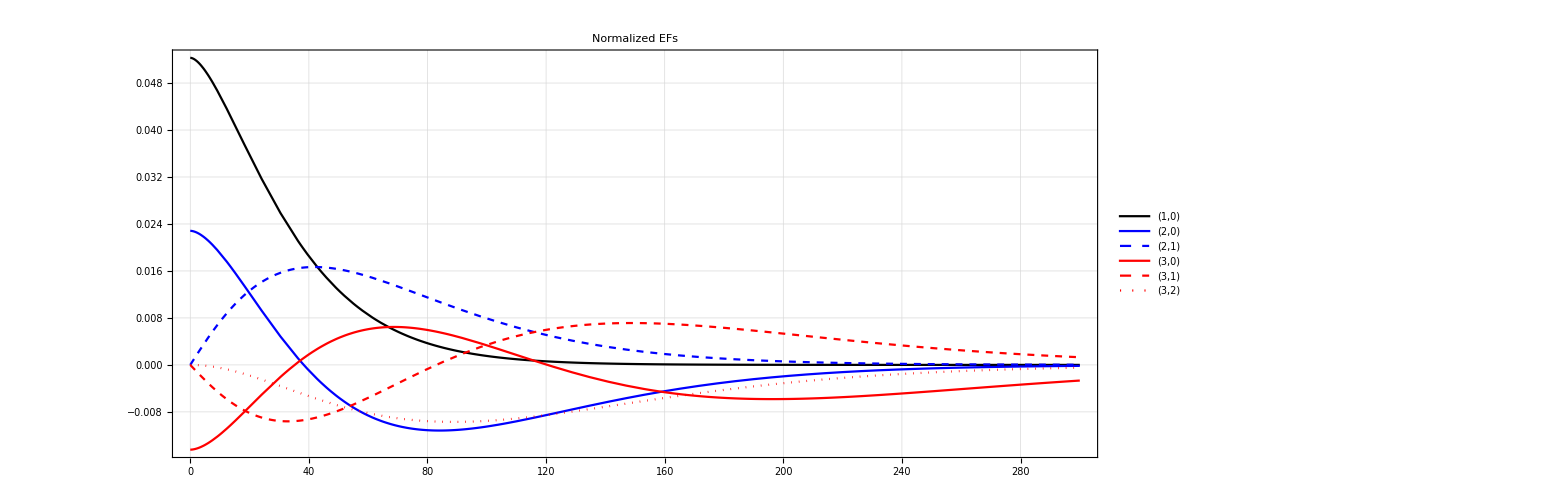

```mathematica
Plot[
Evaluate[(#[r]&/@Flatten[Normal@onefile["efs"]])],
{r,0,300},PlotLabel->Style["Normalized EFs",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
```

#### So it says we’re normalized but... are we?

```mathematica
LightGreen~bg~Dataset@<|Table[
tssf["`1`",rmx/(10^3)]->Module[
{
rmax=rmx,
efs=Normal@onefile["efs"],
evs=Normal@onefile["evs"],
mu=Normal@onefile["params","inputs","mu"],
norms,normcheck,avgr,rsq,xbhr,f0,
niop={Method->"GlobalAdaptive",MinRecursion->10,MaxRecursion->10^6}
},
normcheck=Table[
NIntegrate[
r*(Abs[efs[[n,m]][r]]^2),
{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]
],
{n,3},{m,n}
];
avgr=Table[
UnitConvert[Quantity[NIntegrate[
(r^2)*(Abs[efs[[n,m]][r]]^2),
{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]
],"BohrRadius"],"Nanometers"],
{n,3},{m,n}
];
rsq=Table[
UnitConvert[Quantity[Sqrt[NIntegrate[
(r^3)*(Abs[efs[[n,m]][r]]^2),
{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]
]],"BohrRadius"],"Nanometers"],
{n,3},{m,n}
];
xbhr=Table[
{UnitConvert[Quantity[Last[Last[Last[#]]],"BohrRadius"],"Nanometers"],First[#]}&[NMaximize[{Abs[r*((efs[[n,m]][r])^2)],0≤r≤1000},r,Method->"SimulatedAnnealing"]],
{n,3},{m,n}];
f0=Table[
2*mu*QuantityMagnitude[(evs[[n,2]]-evs[[1,1]]),"Hartrees"]*((1/2)*NIntegrate[
(r^2)*efs[[1,1]][r]*efs[[n,2]][r],{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]])^2,
{n,{2,3}}];
<|
"rmax"->rmax,
"norm"->normcheck,
"avgr"->avgr,
"avgrsq"->rsq,
"abx"->xbhr,
"f0"->f0
|>
],
{rmx,Union@Flatten@Table[i*10^n,{n,3,5},{i,10}]}
]|>
```

Dataset[<>]

```mathematica
Union@Flatten@Table[i*10^n,{n,3,5},{i,10}]
```

{1000,2000,3000,4000,5000,6000,7000,8000,9000,10000,20000,30000,40000,50000,60000,70000,80000,90000,100000,200000,300000,400000,500000,600000,700000,800000,900000,1000000}

### Starting to formulate a plan.

The important quantities, i.e. a_B^x (for polaritons/BEC) and f_0 (for α and 𝒜), can just be straightforwardly calculated as-is (use r_max=10^5).
Calculate ⟨r⟩ w/ r_max 10^5 even though we don’t use it for anything.
Don’t bother with √⟨r^2⟩ at all though.

The rest should be straightforward... (famous last words)

So, let’s put together a Module that will calculate everything and then save a re-processed Dataset.

```mathematica
Normal@onefile["params","inputs"]
```

<|mu→0.15,chi→18.8973,l→8.50377,kappa→1.5,D→0,cscale→10,shift→1|>

```mathematica
UnitConvert[Quantity[Normal@onefile["params","inputs",{"l","chi"}],"BohrRadius"],"Nanometers"]
```

<|l→0.45,chi→1.|> nm

### Refine the “first attempt” and get it ready to deploy

```mathematica
?"*Timing"
```

Figure out (for reals) how to handle various function arguments
	- Different top-level keys for different “default” scenarios, then another top-level key where everything is a function argument.
How to iterate over the file list?
Parallel processing??

```mathematica
AbsoluteTiming[Table[
DynamicModule[{onefile=KeyTake[Quiet[Import[fnamepath]],{"evs","efs","miscres","params"}]},
DynamicModule[
{
(* NIntegrate parameters *)
rmax=10^5,niop={Method->"GlobalAdaptive",MinRecursion->10,MaxRecursion->10^6},
fname=StringSplit[fnamepath,"/"][[2]],
(* Unpack the old dataset *)
efs=Normal@onefile["efs"],
evs=Normal@onefile["evs"],
miscres=Normal@onefile["miscres"],params=Normal@onefile["params"],
eb=Abs[Normal@onefile["evs"][[1,1]]],gsef=Normal@onefile["efs"][[1,1]],
mu=Normal@onefile["params","inputs","mu"],chi=Quantity[Normal@onefile["params","inputs","chi"],"BohrRadius"],l=Quantity[Normal@onefile["params","inputs","l"],"BohrRadius"],kappa=Normal@onefile["params","inputs","kappa"],
(* Reserve variable names for calculations *)
norms,normcheck,avgr,
(* For optical properties *)
f0,f0tilde,alcon,alpha,afcon,afac,
(* For polaritons *)
fexresk,fecpctk,fvf,fegap,flcav,fldbr,fleff,freff,fmcav,fgamcav,fmex,
fvsav,fhxsq,fhcsq,fgampol,freimelpup,
(* For BEC *)
fmlp,fgsxbhr,fueff,fcs,ftc0,ftcbkt,ftcsol,
fnc0,fncfromt,
ids,fds
},
normcheck=Table[NIntegrate[r*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],{n,3},{m,n}];
avgr=Table[UnitConvert[Quantity[NIntegrate[(r^2)*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],"BohrRadius"],"Nanometers"],{n,3},{m,n}];
(* Optical Properties *)
f0=Table[2*mu*QuantityMagnitude[(evs[[n,2]]-evs[[1,1]]),"Hartrees"]*((1/2)*NIntegrate[(r^2)*efs[[1,1]][r]*efs[[n,2]][r],{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]])^2,{n,{2,3}}];
f0tilde=Quantity[f0/mu,"ElectronMass"^-1];
alcon=UnitSimplify[(Pi*(cee^2))/(2*ce0*ccc*Sqrt[kappa]*Quantity[mu,"ElectronMass"]*l)];
alpha[nf_Integer,nx_,gamma_]:=2*UnitConvert[alcon*Quantity[nx,"Meters"^-2]*f0[[nf]]*(2/Quantity[gamma,"Seconds"^-1]),"Meters"^-1];
afcon=alcon*l;
afac[nf_Integer,nx_,gamma_]:=1-Exp[-alpha[nf,nx,gamma]*l];
(* Polariton stuff - NOTE: leaving Egap as a free parameter is the least bad approach at this point... And same for (me*mh)... argh. I guess it now makes more sense why no one has done this before... *)
fmex[memh_]:=Quantity[memh/mu,"ElectronMass"];
fexresk[egap_,memh_][k_]:=UnitConvert[(egap-eb)+(((chb*Quantity[k,"Micrometers"^-1])^2)/(2*fmex[memh])),"Millielectronvolts"];
(* We need vf to calculate V! Turns out choosing egap wil be preeeettty important... *)
fvf[egapp_]:=UnitConvert[Sqrt[egapp/Quantity[mu,"ElectronMass"]],"Meters"/"Seconds"];
fegap[vff_]:=UnitConvert[Quantity[mu,"ElectronMass"]*(Quantity[vff,"Meters"/"Seconds"]^2),"Millielectronvolts"];
(* Cavity photon properties *) 
fmcav[epscav_,egap_][de_]:=UnitConvert[epscav*((egap-eb)*(1+de))/(ccc^2),"ElectronMass"];
fecpctk[epscav_,egap_][de_,k_]:=UnitConvert[((egap-eb)*(1+de))+(((chb*ccc*Quantity[k,"Micrometers"^-1])^2)/(2*epscav*((egap-eb)*(1+de)))),"Millielectronvolts"];
(* Cavity lengths *)
flcav[epscav_,egap_,n1_,n2_,Nharm_,ndbr_][de_,k_]:=UnitConvert[(Nharm*Pi*chb*ccc)/(fecpctk[epscav,egap][de,k]*Sqrt[epscav]),"Micrometers"];
fldbr[epscav_,egap_,n1_,n2_,Nharm_,ndbr_][de_,k_]:=UnitConvert[(chh*ccc/fecpctk[epscav,egap][de,k])*n1*n2/(2*Sqrt[epscav]*Abs[n2-n1]),"Micrometers"];
fleff[epscav_,egap_,n1_,n2_,Nharm_,ndbr_][de_,k_]:=flcav[epscav,egap,n1,n2,Nharm,ndbr][de,k]+ndbr*fldbr[epscav,egap,n1,n2,Nharm,ndbr][de,k];
freff[r1_,r2_]:=(4*r1*r2)/((Sqrt[r1]+Sqrt[r2])^2);
(* Cavity damping *)
fgamcav[epscav_,egap_,n1_,n2_,Nharm_,ndbr_,r1_,r2_][de_,k_]:=UnitConvert[((1/2)*(((1-Sqrt[r1])/Sqrt[r1])+((1-Sqrt[r2])/Sqrt[r2]))*(ccc/(Sqrt[epscav]*fleff[epscav,egap,n1,n2,Nharm,ndbr][de,k]))),"Seconds"^-1];
(* V, i.e. exciton-photon coupling constant *)
fvsav[epscav_,egap_,memh_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=Sqrt[UnitConvert[nml*((1+Sqrt[freff[r1,r2]])/Sqrt[freff[r1,r2]])*(((cee^2)*(fvf[egap]^2))/(ce0*fexresk[egap,memh][k]*fleff[epscav,egap,n1,n2,Nharm,ndbr][de,k]*Sqrt[epscav*kappa]))*(Quantity[(1/(2*Pi))*gsef[0],"BohrRadius"^-1]^2),"Seconds"^-2]];
(* Polaritons -- Hopfield coeffs *)
fhxsq[epscav_,egap_,memh_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=(1/2)*(1-((fecpctk[epscav,egap][de,k]-fexresk[egap,memh][k])/(Sqrt[((fecpctk[epscav,egap][de,k]-fexresk[egap,memh][k])^2)+((2*chb*fvsav[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k])^2)])));
fhcsq[epscav_,egap_,memh_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=(1/2)*(1+((fecpctk[epscav,egap][de,k]-fexresk[egap,memh][k])/(Sqrt[((fecpctk[epscav,egap][de,k]-fexresk[egap,memh][k])^2)+((2*chb*fvsav[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k])^2)])));
(* Polaritons -- complex eigenenergies *)
freimelpup[epscav_,egap_,memh_,gamex_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[
{term1=((fexresk[egap,memh][k]+fecpctk[epscav,egap][de,k]-I*chb*(fgamcav[epscav,egap,n1,n2,Nharm,ndbr,r1,r2][de,k]+gamex))/2),term2=Sqrt[(chb*fvsav[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k])^2+((1/4)*(((fecpctk[epscav,egap][de,k]-fexresk[egap,memh][k])+I*chb*(gamex-fgamcav[epscav,egap,n1,n2,Nharm,ndbr,r1,r2][de,k]))^2))]},{{UnitConvert[Re[term1+term2],"Millielectronvolts"],UnitConvert[Im[term1+term2],"Millielectronvolts"]},{UnitConvert[Re[term1-term2],"Millielectronvolts"],UnitConvert[Im[term1-term2],"Millielectronvolts"]}}];
(* BEC - ground state exciton bohr radius *)
fgsxbhr=UnitConvert[Quantity[Last[Last[Last[NMaximize[{Abs[r*((gsef[r])^2)],0≤r≤1000},r,Method->"SimulatedAnnealing"]]]],"BohrRadius"],"Nanometers"];
(* BEC -- polariton-polariton interaction parameters *)
fueff[epscav_,egap_,memh_,xbhr_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitSimplify[(6*Abs[eb]*(xbhr^2)*(fhxsq[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]^2))];
fmlp[epscav_,egap_,memh_,xbhr_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=(((fhxsq[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]/fmex[memh])+(fhcsq[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]/fmcav[epscav,egap][de]))^(-1));
fcs[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitConvert[Sqrt[fueff[epscav,egap,memh,xbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]*nlp/fmlp[epscav,egap,memh,xbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],"Meters"/"Seconds"];
(* BEC -- critical temps *)
ftc0[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitConvert[(((2*Pi*(chb^2)*(fueff[epscav,egap,memh,xbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]^2))/(3*Zeta[3]*fmlp[epscav,egap,memh,xbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]))^(1/3))*(nlp/ckb),"Kelvins"];
ftcsol[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[{a=(3*Zeta[3])/(4*(nlp^2)*fueff[epscav,egap,memh,xbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]^2),c=(Pi*(chb^2)*nlp)/(2*fmlp[epscav,egap,memh,xbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k])},With[{A=(Sqrt[(3*(a^3))*(4+(27*a*(c^2)))]-(9*(a^2)*c))},(*UnitConvert*)UnitSimplify[(1/ckb)*(((2/3)^(1/3)*(A^(-1/3)))-(((1/(18*(a^3)))^(1/3))*(A^(1/3))))(*,"Kelvins"*)]]];
(* BEC -- critical densities *)
fnc0[epscav_,egap_,memh_,xbhr_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_,tc_][de_,k_]:=UnitConvert[(ckb*tc)*((3*Zeta[3]*fmlp[epscav,egap,memh,xbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k])/(2*Pi*(chb^2)*(fueff[epscav,egap,memh,xbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]^2)))^(1/3),"Meters"^(-2)];
fncfromt[epscav_,egap_,memh_,xbhr_,n1_,n2_,Nharm_,ndbr_,r1_,r2_,nml_,tc_,tcfunc_][de_,k_]:=Quantity[FindRoot[QuantityMagnitude@Re[tcfunc[epscav,egap,memh,xbhr,Quantity[nlp,"Meters"^(-2)],n1,n2,Nharm,ndbr,r1,r2,nml][0,0]]==tc,{nlp,10^11}][[1]]//Last,"Meters"^-2];
ids=Dataset[<|
"evs"->evs,
"efs"->efs,
"miscres"->Join[miscres,<|"norm"->normcheck,"avgr"->avgr|>],
"params"->Join[params,<|"nintrmax"->rmax,"reprocnintopts"->niop,"filename"->p1drp<>"reproc_"<>fname|>],
"f0"->f0,
"alcon"->alcon,
"alpha"->(Function[{nx,gamma},alpha[#,nx,gamma]]&/@{1,2}),
"afcon"->afcon,
"afac"->(Function[{nx,gamma},afac[#,nx,gamma]]&/@{1,2}),
"gsxbhr"->fgsxbhr,
"genMC"->(Module[
{
epscav=#epscav,n1=#n1,n2=#n2,r1=#r1,r2=#r2,ndbr=#ndbr,Nharm=#Nharm,
memh=#memh,egap=#egap,vf=#vf
},
<|
"xprops"-><|
"memh"->memh,"mex"->fmex[memh],"vf"->vf[egap]
|>,
"cavprops"-><|
"lcde"->{
Function[{de,k},flcav[epscav,egap,n1,n2,Nharm,ndbr][de,k]],
Function[{de,k},fldbr[epscav,egap,n1,n2,Nharm,ndbr][de,k]],
Function[{de,k},fleff[epscav,egap,n1,n2,Nharm,ndbr][de,k]]
},
"reff"->freff[r1,r2],
"gamcav"->Function[{de,k},fgamcav[epscav,egap,n1,n2,Nharm,ndbr,r1,r2][de,k]]
|>,
"polprops"-><|
"v"->Function[{nml,de,k},fvsav[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],
"2hbv"->Function[{nml,de,k},UnitConvert[2*chb*fvsav[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],"Millielectronvolts"],
"hxc"->(Function[{nml,de,k},#[epscav,egap,memh,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]]&/@{fhxsq,fhcsq}),
"reimelpup"->Function[{gamex,nml,de,k},freimelpup[epscav,egap,memh,gamex,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],
"hbor"->Function[{gamex,nml,de,k},(UnitConvert[(#[[1,1]]-#[[2,1]]),"Millielectronvolts"]&[freimelpup[epscav,egap,memh,gamex,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]])]
|>,
"becprops"-><|
"ueff"->Function[{nml,de,k},fueff[epscav,egap,memh,fgsxbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],
"uenlp"->Function[{nlp,nml,de,k},nlp*fueff[epscav,egap,memh,fgsxbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],
"mlp"->Function[{nml,de,k},fmlp[epscav,egap,memh,fgsxbhr,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],
"cs"->Function[{nlp,nml,de,k},fcs[epscav,egap,memh,fgsxbhr,nlp,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],
"tc0"->Function[{nlp,nml,de,k},ftc0[epscav,egap,memh,fgsxbhr,nlp,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],
"tcsol"->Function[{nlp,nml,de,k},ftcsol[epscav,egap,memh,fgsxbhr,nlp,n1,n2,Nharm,ndbr,r1,r2,nml][de,k]],
"nc0"->Function[{tc,nml,de,k},fnc0[epscav,egap,memh,fgsxbhr,n1,n2,Nharm,ndbr,r1,r2,nml,Quantity[tc,"Kelvins"]][de,k]],
"ncftcsol"->Function[{tc,nml,de,k},fncfromt[epscav,egap,memh,fgsxbhr,n1,n2,Nharm,ndbr,r1,r2,nml,tc,ftcsol][de,k]]
|>
|>]&),
"open1dbr"-><|"epscav"->1,"n1"->1.45,"n2"->2.05,"r1"->0.985,"r2"->0.95,"ndbr"->1,"Nharm"->1|>,
"symeh"-><|"memh"->4*(mu^2)|>,
"tmdceh"-><|"memh"->(16/3)*(mu^2)|>,
"freeeh"-><|"memh"->amemh|>,
"speceg"->Function[{eg},
<|
"egap"->Quantity[eg,"Millielectronvolts"],"vf"->UnitConvert[Sqrt[Quantity[eg,"Millielectronvolts"]/Quantity[mu,"ElectronMass"]],"Meters"/"Seconds"]
|>],
"specvf"->Function[{vff},
<|
"egap"->UnitConvert[Quantity[mu,"ElectronMass"]*(Quantity[vff,"Meters"/"Seconds"]^2),"Millielectronvolts"],"vf"->Quantity[vff,"Meters"/"Seconds"]
|>],
"freeeg"-><|"egap"->aegap,"vf"->fvf|>
|>];
Export[p1drp<>"reproc_"<>fname,Evaluate[ids]]
]],
{fnamepath,fn1d[[;;6]]}
];]
```

{15.0669,Null}

```mathematica
timp=KeyDrop[Import[p1drp<>"reproc_"<>(StringSplit[fn1d[[1]],"/"][[2]])],{"efs","miscres","params"}];
```

```mathematica
timp
```

Dataset[<>]

```mathematica
timp["speceg"][1500]
timp["speceg"/*[1500]]
timp["alpha"/*1/*(#[5*10^15,10^13]&)]
```

<|egap→1500 meV,vf→1.3262×10^6 m/s|>

```mathematica
Normal@timp[{"genMC","open1dbr","symeh","speceg"/*(#[1500]&)}(*/*(#[[1]][Join[#[[2]],#[[3]],#[[4]]]]&)*)]
```

{Module[{epscav$=#epscav,n1$=#n1,n2$=#n2,r1$=#r1,r2$=#r2,ndbr$=#ndbr,Nharm$=#Nharm,memh$=#memh,egap$=#egap,vf$=#vf},Association[xprops→Association[memh→memh$,mex→fmex$724502[memh$],vf→vf$[egap$]],cavprops→Association[lcde→{Function[{de$,k$},flcav$724502[epscav$,egap$,n1$,n2$,Nharm$,ndbr$][de$,k$]],Function[{de$,k$},fldbr$724502[epscav$,egap$,n1$,n2$,Nharm$,ndbr$][de$,k$]],Function[{de$,k$},fleff$724502[epscav$,egap$,n1$,n2$,Nharm$,ndbr$][de$,k$]]},reff→freff$724502[r1$,r2$],gamcav→Function[{de$,k$},fgamcav$724502[epscav$,egap$,n1$,n2$,Nharm$,ndbr$,r1$,r2$][de$,k$]]],polprops→Association[v→Function[{nml$,de$,k$},fvsav$724502[epscav$,egap$,memh$,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],2hbv→Function[{nml$,de$,k$},UnitConvert[2 chb fvsav$724502[epscav$,egap$,memh$,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],Millielectronvolts],hxc→(Function[{nml$,de$,k$},#1[epscav$,egap$,memh$,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]]&)/@{fhxsq$724502,fhcsq$724502},reimelpup→Function[{gamex$,nml$,de$,k$},freimelpup$724502[epscav$,egap$,memh$,gamex$,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],hbor→Function[{gamex$,nml$,de$,k$},(UnitConvert[#1⟦1,1⟧-#1⟦2,1⟧,Millielectronvolts]&)[freimelpup$724502[epscav$,egap$,memh$,gamex$,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]]]],becprops→Association[ueff→Function[{nml$,de$,k$},fueff$724502[epscav$,egap$,memh$,fgsxbhr$724502,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],uenlp→Function[{nlp$,nml$,de$,k$},nlp$ fueff$724502[epscav$,egap$,memh$,fgsxbhr$724502,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],mlp→Function[{nml$,de$,k$},fmlp$724502[epscav$,egap$,memh$,fgsxbhr$724502,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],cs→Function[{nlp$,nml$,de$,k$},fcs$724502[epscav$,egap$,memh$,fgsxbhr$724502,nlp$,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],tc0→Function[{nlp$,nml$,de$,k$},ftc0$724502[epscav$,egap$,memh$,fgsxbhr$724502,nlp$,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],tcsol→Function[{nlp$,nml$,de$,k$},ftcsol$724502[epscav$,egap$,memh$,fgsxbhr$724502,nlp$,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$][de$,k$]],nc0→Function[{tc$,nml$,de$,k$},fnc0$724502[epscav$,egap$,memh$,fgsxbhr$724502,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$,tc$ K][de$,k$]],ncftcsol→Function[{tc$,nml$,de$,k$},fncfromt$724502[epscav$,egap$,memh$,fgsxbhr$724502,n1$,n2$,Nharm$,ndbr$,r1$,r2$,nml$,tc$,ftcsol$724502][de$,k$]]]]]&,<|epscav→1,n1→1.45,n2→2.05,r1→0.985,r2→0.95,ndbr→1,Nharm→1|>,<|memh→0.09|>,<|egap→1500 meV,vf→1.3262×10^6 m/s|>}

```mathematica
Normal@timp[{"open1dbr","symeh","speceg"/*(#[1500]&)}/*(Join@@#&)]
```

<|epscav→1,n1→1.45,n2→2.05,r1→0.985,r2→0.95,ndbr→1,Nharm→1,memh→0.09,egap→1500 meV,vf→1.3262×10^6 m/s|>

### First attempt at an all-in-one reprocessing Module/Function (Freeze)

```mathematica
onefile[Keys]
```

Dataset[<>]

```mathematica
Normal@onefile[{"rsq","xbohr","f0","alpha","afac"}]
```

<|rsq→{{0.0529177211 √NIntegrate[r^3 (efform$1551114667⟦n,m,2⟧[r])^2,{r,0,rmax$1551114667},{Method→GlobalAdaptive,MinRecursion→10,MaxRecursion→1000000}] nm},{0.0529177211 √NIntegrate[r^3 (efform$1551114667⟦n,m,2⟧[r])^2,{r,0,rmax$1551114667},{Method→GlobalAdaptive,MinRecursion→10,MaxRecursion→1000000}] nm,0.0529177211 √NIntegrate[r^3 (efform$1551114667⟦n,m,2⟧[r])^2,{r,0,rmax$1551114667},{Method→GlobalAdaptive,MinRecursion→10,MaxRecursion→1000000}] nm},{0.0529177211 √NIntegrate[r^3 (efform$1551114667⟦n,m,2⟧[r])^2,{r,0,rmax$1551114667},{Method→GlobalAdaptive,MinRecursion→10,MaxRecursion→1000000}] nm,0.0529177211 √NIntegrate[r^3 (efform$1551114667⟦n,m,2⟧[r])^2,{r,0,rmax$1551114667},{Method→GlobalAdaptive,MinRecursion→10,MaxRecursion→1000000}] nm,0.0529177211 √NIntegrate[r^3 (efform$1551114667⟦n,m,2⟧[r])^2,{r,0,rmax$1551114667},{Method→GlobalAdaptive,MinRecursion→10,MaxRecursion→1000000}] nm}},xbohr→{{0.0529177211 NMaximize[{Abs[r (2.3406 InterpolatingFunction[…][ArcTan[r$/10]])[r]],0≤r≤3000},r,Method→SimulatedAnnealing] nm},{0.0529177211 NMaximize[{Abs[r (0.979058 InterpolatingFunction[…][ArcTan[r$/10]])[r]],0≤r≤3000},r,Method→SimulatedAnnealing] nm,0.0529177211 NMaximize[{Abs[r (0.499228 InterpolatingFunction[…][ArcTan[r$/10]])[r]],0≤r≤3000},r,Method→SimulatedAnnealing] nm},{0.0529177211 NMaximize[{Abs[r (0.611536 InterpolatingFunction[…][ArcTan[r$/10]])[r]],0≤r≤3000},r,Method→SimulatedAnnealing] nm,0.0529177211 NMaximize[{Abs[r (0.301323 InterpolatingFunction[…][ArcTan[r$/10]])[r]],0≤r≤3000},r,Method→SimulatedAnnealing] nm,0.0529177211 NMaximize[{Abs[r (0.172251 InterpolatingFunction[…][ArcTan[r$/10]])[r]],0≤r≤3000},r,Method→SimulatedAnnealing] nm}},f0→{{2.81224×10^13},{5.45299×10^21}},alpha→{Function[{nx$,gamma$},{(1.09379×10^-21 nx$)/gamma$ kg},1/Meters],Function[{nx$,gamma$},{(2.12089×10^-13 nx$)/gamma$ kg},1/Meters]},afac→{Function[{nx$,gamma$},{1-ⅇ^(-(9.61823×10^14 nx$)/gamma$ s e^2/(m^2 ε_0 c))}],Function[{nx$,gamma$},{1-ⅇ^(-(1.865×10^23 nx$)/gamma$ s e^2/(m^2 ε_0 c))}]}|>

```mathematica
reproctest=Module[
{
(* NIntegrate parameters *)
rmax=10^5,niop={Method->"GlobalAdaptive",MinRecursion->10,MaxRecursion->10^6},
(* Unpack the old dataset *)
efs=Normal@onefile["efs"],
evs=Normal@onefile["evs"],
eb=Abs[Normal@onefile["evs"][[1,1]]],
mu=Normal@onefile["params","inputs","mu"],chi=Quantity[Normal@onefile["params","inputs","chi"],"BohrRadius"],l=Quantity[Normal@onefile["params","inputs","l"],"BohrRadius"],kappa=Normal@onefile["params","inputs","kappa"],dd=Normal@onefile["params","inputs","D"],cscale=Normal@onefile["params","inputs","cscale"],shift=Normal@onefile["params","inputs","shift"],
(* Reserve variable names for calculations *)
norms,normcheck,avgr,
(* For optical properties *)
f0,f0tilde,alcon,alpha,afcon,afac,
(* For polaritons *)
exresk,ecpctk,vf,lcav,ldbr,leff,reff,mcav,gamcav,mex,
vsav,hxsq,hcsq,gampol,reimelpup,
(* For BEC *)
mlp,gsxbhr,ueff,cs,tc0,tcbkt,tcsol,
nc0,ncfromt
},
normcheck=Table[NIntegrate[r*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],{n,3},{m,n}];
avgr=Table[UnitConvert[Quantity[NIntegrate[(r^2)*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],"BohrRadius"],"Nanometers"],{n,3},{m,n}];
(* Optical Properties *)
f0=Table[2*mu*QuantityMagnitude[(evs[[n,2]]-evs[[1,1]]),"Hartrees"]*((1/2)*NIntegrate[(r^2)*efs[[1,1]][r]*efs[[n,2]][r],{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]])^2,{n,{2,3}}];
f0tilde=Quantity[f0/mu,"ElectronMass"^-1];
alcon=UnitSimplify[(Pi*(cee^2))/(2*ce0*ccc*Sqrt[kappa]*Quantity[mu,"ElectronMass"]*l)];
alpha[nf_Integer,nx_,gamma_]:=2*UnitConvert[alcon*Quantity[nx,"Meters"^-2]*f0[[nf]]*(2/Quantity[gamma,"Seconds"^-1]),"Meters"^-1];
afcon=alcon*l;
afac[nf_Integer,nx_,gamma_]:=1-Exp[-alpha[nf,nx,gamma]*l];
(* Polariton stuff - NOTE: leaving Egap as a free parameter is the least bad approach at this point... And same for (me*mh)... argh. I guess it now makes more sense why no one has done this before... *)
mex[memh_]:=Quantity[memh/mu,"ElectronMass"];
exresk[egap_,memh_][k_]:=UnitConvert[(egap-eb)+(((chb*Quantity[k,"Micrometers"^-1])^2)/(2*mex[memh])),"Millielectronvolts"];
(* We need vf to calculate V! Turns out choosing egap wil be preeeettty important... *)
vf[egap_]:=UnitConvert[Sqrt[egap/Quantity[mu,"ElectronMass"]],"Meters"/"Seconds"];
(* Cavity photon properties *) 
mcav[epscav_,egap_][de_]:=UnitConvert[epscav*((egap-eb)*(1+de))/(ccc^2),"ElectronMass"];
ecpctk[epscav_,egap_][de_,k_]:=UnitConvert[((egap-eb)*(1+de))+(((chb*ccc*Quantity[k,"Micrometers"^-1])^2)/(2*epscav*((egap-eb)*(1+de)))),"Millielectronvolts"];
(* Cavity lengths *)
lcav[epscav_,egap_,n1_,n2_,NN_,ndbr_][de_,k_]:=UnitConvert[(NN*Pi*chb*ccc)/(ecpctk[epscav,egap][de,k]*Sqrt[epscav]),"Micrometers"];
ldbr[epscav_,egap_,n1_,n2_,NN_,ndbr_][de_,k_]:=UnitConvert[(chh*ccc/ecpctk[epscav,egap][de,k])*n1*n2/(2*Sqrt[epscav]*Abs[n2-n1]),"Micrometers"];
leff[epscav_,egap_,n1_,n2_,NN_,ndbr_][de_,k_]:=lcav[epscav,egap,n1,n2,NN,ndbr][de,k]+ndbr*ldbr[epscav,egap,n1,n2,NN,ndbr][de,k];
reff[r1_,r2_]:=(4*r1*r2)/((Sqrt[r1]+Sqrt[r2])^2);
(* Cavity damping *)
gamcav[epscav_,egap_,n1_,n2_,NN_,ndbr_,r1_,r2_][de_,k_]:=UnitConvert[((1/2)*(((1-Sqrt[r1])/Sqrt[r1])+((1-Sqrt[r2])/Sqrt[r2]))*(ccc/(Sqrt[epscav]*leff[epscav,egap,n1,n2,NN,ndbr][de,k]))),"Seconds"^-1];
(* V, i.e. exciton-photon coupling constant *)
vsav[epscav_,egap_,memh_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=Sqrt[UnitConvert[nml*((1+Sqrt[reff[r1,r2]])/Sqrt[reff[r1,r2]])*(((cee^2)*(vf[egap]^2))/(ce0*exresk[egap,memh][k]*leff[epscav,egap,n1,n2,NN,ndbr][de,k]*Sqrt[epscav*kappa]))*(Quantity[(1/(2*Pi))*efs[[1,1]][0],"BohrRadius"^-1]^2),"Seconds"^-2]];
(* Polaritons -- Hopfield coeffs *)
hxsq[epscav_,egap_,memh_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(1/2)*(1-((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])/(Sqrt[((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])^2)+((2*chb*vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2)])));
hcsq[epscav_,egap_,memh_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(1/2)*(1+((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])/(Sqrt[((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])^2)+((2*chb*vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2)])));
(* Polaritons -- complex eigenenergies *)
reimelpup[epscav_,egap_,memh_,gamex_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[
{term1=((exresk[egap,memh][k]+ecpctk[epscav,egap][de,k]-I*chb*(gamcav[epscav,egap,n1,n2,NN,ndbr,r1,r2][de,k]+gamex))/2),term2=Sqrt[(chb*vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2+((1/4)*(((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])+I*chb*(gamex-gamcav[epscav,egap,n1,n2,NN,ndbr,r1,r2][de,k]))^2))]},{{UnitConvert[Re[term1+term2],"Millielectronvolts"],UnitConvert[Im[term1+term2],"Millielectronvolts"]},{UnitConvert[Re[term1-term2],"Millielectronvolts"],UnitConvert[Im[term1-term2],"Millielectronvolts"]}}];
(* BEC - ground state exciton bohr radius *)
gsxbhr=UnitConvert[Quantity[Last[Last[Last[NMaximize[{Abs[r*((efs[[1,1]][r])^2)],0≤r≤1000},r,Method->"SimulatedAnnealing"]]]],"BohrRadius"],"Nanometers"];
(* BEC -- polariton-polariton interaction parameters *)
ueff[epscav_,egap_,memh_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitSimplify[(6*Abs[eb]*(xbhr^2)*(hxsq[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2))];
mlp[epscav_,egap_,memh_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(((hxsq[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k]/mex[memh])+(hcsq[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k]/mcav[epscav,egap][de]))^(-1));
cs[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitConvert[Sqrt[ueff[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]*nlp/mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]],"Meters"/"Seconds"];
(* BEC -- critical temps *)
tc0[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitConvert[(((2*Pi*(chb^2)*(ueff[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2))/(3*Zeta[3]*mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]))^(1/3))*(nlp/ckb),"Kelvins"];
tcsol[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[{a=(3*Zeta[3])/(4*(nlp^2)*ueff[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2),c=(Pi*(chb^2)*nlp)/(2*mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k])},With[{A=(Sqrt[(3*(a^3))*(4+(27*a*(c^2)))]-(9*(a^2)*c))},(*UnitConvert*)UnitSimplify[(1/ckb)*(((2/3)^(1/3)*(A^(-1/3)))-(((1/(18*(a^3)))^(1/3))*(A^(1/3))))(*,"Kelvins"*)]]];
(* BEC -- critical densities *)
nc0[epscav_,egap_,memh_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_][de_,k_]:=UnitConvert[(ckb*tc)*((3*Zeta[3]*mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k])/(2*Pi*(chb^2)*(ueff[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2)))^(1/3),"Meters"^(-2)];
ncfromt[epscav_,egap_,memh_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_,tcfunc_][de_,k_]:=Quantity[FindRoot[QuantityMagnitude@Re[tcfunc[epscav,egap,memh,xbhr,Quantity[nlp,"Meters"^(-2)],n1,n2,NN,ndbr,r1,r2,nml][0,0]]==tc,{nlp,10^11}][[1]]//Last,"Meters"^-2];
Dataset@<|
"evs"->evs,
"efs"->efs,
"norm"->normcheck,
"avgr"->avgr,
"f0"->f0,
"alcon"->alcon,
"alpha"->(alpha[#,10^15,10^13]&/@{1,2}),
"afcon"->afcon,
"afac"->(afac[#,10^15,10^13]&/@{1,2}),
"rmax"->rmax,
"niopts"->niop,
"gsxbhr"->gsxbhr,
"open1dbr"->With[{memh=4*(mu^2),egap=Quantity[2000,"Millielectronvolts"],gamex=Quantity[10^13,"Seconds"^-1],epscav=1,n1=1.45,n2=2.05,r1=0.985,r2=0.95,ndbr=1,NN=1,nml=1,nlp=Quantity[5*10^15,"Meters"^-2]},
<|
"xprops"-><|
"mu"->mu,"memh"->memh,"mex"->mex[memh],"vf"->vf[egap]
|>,
"cavprops"-><|
"lcde"->{lcav[epscav,egap,n1,n2,NN,ndbr][0,0],ldbr[epscav,egap,n1,n2,NN,ndbr][0,0],leff[epscav,egap,n1,n2,NN,ndbr][0,0]},
"reff"->reff[r1,r2],
"gamcav"->gamcav[epscav,egap,n1,n2,NN,ndbr,r1,r2][0,0]
|>,
"polprops"-><|
"v"->vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"2hbv"->UnitConvert[2*chb*vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][0,0],"Millielectronvolts"],
"hxc"->(#[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][0,0]&/@{hxsq,hcsq}),
"reimelpup"->reimelpup[epscav,egap,memh,gamex,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"hbor"->(UnitConvert[(#[[1,1]]-#[[2,1]]),"Millielectronvolts"]&[reimelpup[epscav,egap,memh,gamex,n1,n2,NN,ndbr,r1,r2,nml][0,0]])
|>,
"becprops"-><|
"ueff"->ueff[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"uenlp"->nlp*ueff[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"mlp"->mlp[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"cs"->cs[epscav,egap,memh,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"tc0"->tc0[epscav,egap,memh,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"tcsol"->tcsol[epscav,egap,memh,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"nc0"->nc0[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml,Quantity[300,"Kelvins"]][0,0],
"ncftcsol"->ncfromt[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml,300,tcsol][0,0]
|>
|>]
|>
];
```

{1.54,Null}

```mathematica
reproctest["open1dbr"]
```

Dataset[<>]

### Faster if functions are globally defined? (Interesting - no difference in timing compared to defining functions w/in module (meaning that *re-defining* the functions with every Module call has a negligible effect on timing)

#### Allllllll the functions

```mathematica
Clear[fmex,fexresk,fvf,fmcav,fecpctk,flcav,fldbr,fleff,freff,fgamcav,fvsav,fhxsq,fhcsq,freimelpup,fgsxbhr,fueff,fmlp,fcs,ftc0,ftcbkt,ftcsol,fnc0,fncfromt]
```

```mathematica
(* Polariton stuff - NOTE: leaving Egap as a free parameter is the least bad approach at this point... And same for (me*mh)... argh. I guess it now makes more sense why no one has done this before... *)
fmex[memh_,mu_]:=Quantity[memh/mu,"ElectronMass"]
fexresk[egap_,evs_,memh_,mu_][k_]:=UnitConvert[(egap-evs[[1,1]])+(((chb*Quantity[k,"Micrometers"^-1])^2)/(2*fmex[memh,mu])),"Millielectronvolts"]
(* We need vf to calculate V! Turns out choosing egap wil be preeeettty important... *)
fvf[egap_,mu_]:=UnitConvert[Sqrt[egap/Quantity[mu,"ElectronMass"]],"Meters"/"Seconds"]
(* Cavity photon properties *) 
fmcav[epscav_,egap_,evs_][de_]:=UnitConvert[epscav*((egap-evs[[1,1]])*(1+de))/(ccc^2),"ElectronMass"]
fecpctk[epscav_,egap_,evs_][de_,k_]:=UnitConvert[((egap-evs[[1,1]])*(1+de))+(((chb*ccc*Quantity[k,"Micrometers"^-1])^2)/(2*epscav*((egap-evs[[1,1]])*(1+de)))),"Millielectronvolts"]
(* Cavity lengths *)
flcav[epscav_,egap_,evs_,n1_,n2_,NN_,ndbr_][de_,k_]:=UnitConvert[(NN*Pi*chb*ccc)/(fecpctk[epscav,egap,evs][de,k]*Sqrt[epscav]),"Micrometers"]
fldbr[epscav_,egap_,evs_,n1_,n2_,NN_,ndbr_][de_,k_]:=UnitConvert[(chh*ccc/fecpctk[epscav,egap,evs][de,k])*n1*n2/(2*Sqrt[epscav]*Abs[n2-n1]),"Micrometers"]
fleff[epscav_,egap_,evs_,n1_,n2_,NN_,ndbr_][de_,k_]:=flcav[epscav,egap,evs,n1,n2,NN,ndbr][de,k]+ndbr*fldbr[epscav,egap,evs,n1,n2,NN,ndbr][de,k]
freff[r1_,r2_]:=(4*r1*r2)/((Sqrt[r1]+Sqrt[r2])^2);
(* Cavity damping *)
fgamcav[epscav_,egap_,evs_,n1_,n2_,NN_,ndbr_,r1_,r2_][de_,k_]:=UnitConvert[((1/2)*(((1-Sqrt[r1])/Sqrt[r1])+((1-Sqrt[r2])/Sqrt[r2]))*(ccc/(Sqrt[epscav]*fleff[epscav,egap,evs,n1,n2,NN,ndbr][de,k]))),"Seconds"^-1]
(* V, i.e. exciton-photon coupling constant *)
fvsav[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=Sqrt[UnitConvert[nml*((1+Sqrt[freff[r1,r2]])/Sqrt[freff[r1,r2]])*(((cee^2)*(fvf[egap,mu]^2))/(ce0*fexresk[egap,evs,memh,mu][k]*fleff[epscav,egap,evs,n1,n2,NN,ndbr][de,k]*Sqrt[epscav*kappa]))*(Quantity[(1/(2*Pi))*efs[[1,1]][0],"BohrRadius"^-1]^2),"Seconds"^-2]]
(* Polaritons -- Hopfield coeffs *)
fhxsq[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(1/2)*(1-((fecpctk[epscav,egap,evs][de,k]-fexresk[egap,evs,memh,mu][k])/(Sqrt[((fecpctk[epscav,egap,evs][de,k]-fexresk[egap,evs,memh,mu][k])^2)+((2*chb*fvsav[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2)])))
fhcsq[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(1/2)*(1+((fecpctk[epscav,egap,evs][de,k]-fexresk[egap,evs,memh,mu][k])/(Sqrt[((fecpctk[epscav,egap,evs][de,k]-fexresk[egap,evs,memh,mu][k])^2)+((2*chb*fvsav[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2)])))
(* Polaritons -- complex eigenenergies *)
freimelpup[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,gamex_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[
{term1=((fexresk[egap,evs,memh,mu][k]+fecpctk[epscav,egap,evs][de,k]-I*chb*(fgamcav[epscav,egap,evs,n1,n2,NN,ndbr,r1,r2][de,k]+gamex))/2),term2=Sqrt[(chb*fvsav[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2+((1/4)*(((fecpctk[epscav,egap,evs][de,k]-fexresk[egap,evs,memh,mu][k])+I*chb*(gamex-fgamcav[epscav,egap,evs,n1,n2,NN,ndbr,r1,r2][de,k]))^2))]},{{UnitConvert[Re[term1+term2],"Millielectronvolts"],UnitConvert[Im[term1+term2],"Millielectronvolts"]},{UnitConvert[Re[term1-term2],"Millielectronvolts"],UnitConvert[Im[term1-term2],"Millielectronvolts"]}}]
(* BEC - ground state exciton bohr radius *)
fgsxbhr[efs_]:=UnitConvert[Quantity[Last[Last[Last[NMaximize[{Abs[r*((efs[[1,1]][r])^2)],0≤r≤1000},r,Method->"SimulatedAnnealing"]]]],"BohrRadius"],"Nanometers"]
(* BEC -- polariton-polariton interaction parameters *)
fueff[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitSimplify[(6*Abs[evs[[1,1]]]*(xbhr^2)*(fhxsq[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2))]
fmlp[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(((fhxsq[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][de,k]/fmex[memh,mu])+(fhcsq[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][de,k]/fmcav[epscav,egap,evs][de]))^(-1))
fcs[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitConvert[Sqrt[fueff[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]*nlp/fmlp[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]],"Meters"/"Seconds"]
(* BEC -- critical temps *)
ftc0[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitConvert[(((2*Pi*(chb^2)*(fueff[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2))/(3*Zeta[3]*fmlp[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]))^(1/3))*(nlp/ckb),"Kelvins"]
ftcbkt[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[
{Tc0=ftc0[epscav,kappa,egap,evs,efs,memh,mu,xbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][de,k]},(*UnitConvert*)
UnitSimplify[
(
(
1+Sqrt[
((32/27)*(((fmlp[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]*ckb*Tc0)/(Pi*(chb^2)*nlp))^3))+1
]
)^(1/3)
-
(
Sqrt[
((32/27)*(((fmlp[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]*ckb*Tc0)/(Pi*(chb^2)*nlp))^3))+1
]-1
)^(1/3)
)*(Tc0/(2^(1/3)))(*,"Kelvins"*)]]
ftcsol[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[{a=(3*Zeta[3])/(4*(nlp^2)*fueff[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2),c=(Pi*(chb^2)*nlp)/(2*fmlp[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k])},With[{A=(Sqrt[(3*(a^3))*(4+(27*a*(c^2)))]-(9*(a^2)*c))},(*UnitConvert*)UnitSimplify[(1/ckb)*(((2/3)^(1/3)*(A^(-1/3)))-(((1/(18*(a^3)))^(1/3))*(A^(1/3))))(*,"Kelvins"*)]]]
(* BEC -- critical densities *)
fnc0[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_][de_,k_]:=UnitConvert[(ckb*tc)*((3*Zeta[3]*fmlp[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k])/(2*Pi*(chb^2)*(fueff[epscav,kappa,egap,evs,efs,memh,mu,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2)))^(1/3),"Meters"^(-2)]
fncfromt[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_,tcfunc_][de_,k_]:=Quantity[FindRoot[QuantityMagnitude@Re[tcfunc[epscav,kappa,egap,evs,efs,memh,mu,xbhr,Quantity[nlp,"Meters"^(-2)],n1,n2,NN,ndbr,r1,r2,nml][0,0]]==tc,{nlp,10^11}][[1]]//Last,"Meters"^-2]
```

```mathematica
DownValues[#]&/@{fmex,fexresk,fvf,fncfromt}
```

{{HoldPattern[fmex[memh_,mu_]]:>memh/mu m_e},{},{HoldPattern[fvf[egap_,mu_]]:>UnitConvert[√(egap/(mu m_e)),Meters/Seconds]},{HoldPattern[fncfromt[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_,tcfunc_,de_,k_]]:>Last[FindRoot[QuantityMagnitude[Re[tcfunc[epscav,kappa,egap,evs,efs,memh,mu,xbhr,nlp per meter^2,n1,n2,NN,ndbr,r1,r2,nml][0,0]]]==tc,{nlp,10^11}]⟦1⟧] per meter^2}}

```mathematica
TableForm[Definition/@{fmex,fexresk,fvf,fncfromt}]
```

fmex[memh_,mu_]:=memh/mu m_e
fexresk[egap_,evs_,memh_,mu_][k_]:=UnitConvert[(egap-evs⟦1,1⟧)+(chb (k /µm))^2/(2 fmex[memh,mu]),Millielectronvolts]
fvf[egap_,mu_]:=UnitConvert[√(egap/(mu m_e)),Meters/Seconds]
fncfromt[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_,tcfunc_][de_,k_]:=Last[FindRoot[QuantityMagnitude[Re[tcfunc[epscav,kappa,egap,evs,efs,memh,mu,xbhr,nlp per meter^2,n1,n2,NN,ndbr,r1,r2,nml][0,0]]]==tc,{nlp,10^11}]⟦1⟧] per meter^2
 
fncfromt[epscav_,kappa_,egap_,evs_,efs_,memh_,mu_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_,tcfunc_,de_,k_]:=Last[FindRoot[QuantityMagnitude[Re[tcfunc[epscav,kappa,egap,evs,efs,memh,mu,xbhr,nlp per meter^2,n1,n2,NN,ndbr,r1,r2,nml][0,0]]]==tc,{nlp,10^11}]⟦1⟧] per meter^2

#### Calllllllll the functions in the Module

```mathematica
RepeatedTiming[reproctest2=Module[
{
(* NIntegrate parameters *)
rmax=10^5,niop={Method->"GlobalAdaptive",MinRecursion->10,MaxRecursion->10^6},
(* Unpack the old dataset *)
efs=Normal@onefile["efs"],
evs=Normal@onefile["evs"],
mu=Normal@onefile["params","inputs","mu"],chi=Quantity[Normal@onefile["params","inputs","chi"],"BohrRadius"],l=Quantity[Normal@onefile["params","inputs","l"],"BohrRadius"],kappa=Normal@onefile["params","inputs","kappa"],dd=Normal@onefile["params","inputs","D"],cscale=Normal@onefile["params","inputs","cscale"],shift=Normal@onefile["params","inputs","shift"],
(* Reserve variable names for calculations *)
norms,normcheck,avgr,
(* For optical properties *)
f0,f0tilde,alcon,alpha,afcon,afac,
(* All Pol/BEC functions have been taken out of the module. xbhr is a constant tho so it stays *)
gsxbhr
},
normcheck=Table[NIntegrate[r*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],{n,3},{m,n}];
avgr=Table[UnitConvert[Quantity[NIntegrate[(r^2)*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],"BohrRadius"],"Nanometers"],{n,3},{m,n}];
(* Optical Properties *)
f0=Table[2*mu*QuantityMagnitude[(evs[[n,2]]-evs[[1,1]]),"Hartrees"]*((1/2)*NIntegrate[(r^2)*efs[[1,1]][r]*efs[[n,2]][r],{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]])^2,{n,{2,3}}];
f0tilde=Quantity[f0/mu,"ElectronMass"^-1];
alcon=UnitSimplify[(Pi*(cee^2))/(2*ce0*ccc*Sqrt[kappa]*Quantity[mu,"ElectronMass"]*l)];
alpha[nf_Integer,nx_,gamma_]:=2*UnitConvert[alcon*Quantity[nx,"Meters"^-2]*f0[[nf]]*(2/Quantity[gamma,"Seconds"^-1]),"Meters"^-1];
afcon=alcon*l;
afac[nf_Integer,nx_,gamma_]:=1-Exp[-alpha[nf,nx,gamma]*l];
gsxbhr=UnitConvert[Quantity[Last[Last[Last[NMaximize[{Abs[r*((efs[[1,1]][r])^2)],0≤r≤1000},r,Method->"SimulatedAnnealing"]]]],"BohrRadius"],"Nanometers"];
Dataset@<|
"evs"->evs,
"efs"->efs,
"norm"->normcheck,
"avgr"->avgr,
"f0"->f0,
"alcon"->alcon,
"alpha"->(alpha[#,10^15,10^13]&/@{1,2}),
"afcon"->afcon,
"afac"->(afac[#,10^15,10^13]&/@{1,2}),
"rmax"->rmax,
"niopts"->niop,
"gsxbhr"->gsxbhr,
"open1dbr"->With[{memh=4*(mu^2),egap=Quantity[2000,"Millielectronvolts"],gamex=Quantity[10^13,"Seconds"^-1],epscav=1,n1=1.45,n2=2.05,r1=0.985,r2=0.95,ndbr=1,NN=1,nml=1,nlp=Quantity[5*10^15,"Meters"^-2]},
<|
"xprops"-><|
"mu"->mu,"memh"->memh,"mex"->fmex[memh,mu],"vf"->fvf[egap,mu]
|>,
"cavprops"-><|
"lcde"->{flcav[epscav,egap,evs,n1,n2,NN,ndbr][0,0],fldbr[epscav,egap,evs,n1,n2,NN,ndbr][0,0],fleff[epscav,egap,evs,n1,n2,NN,ndbr][0,0]},
"mcav"->fmcav[epscav,egap,evs][0],
"reff"->freff[r1,r2],
"gamcav"->fgamcav[epscav,egap,evs,n1,n2,NN,ndbr,r1,r2][0,0]
|>,
"polprops"-><|
"v"->fvsav[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"2hbv"->UnitConvert[2*chb*fvsav[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][0,0],"Millielectronvolts"],
"hxc"->(#[epscav,kappa,egap,evs,efs,memh,mu,n1,n2,NN,ndbr,r1,r2,nml][0,0]&/@{fhxsq,fhcsq}),
"reimelpup"->freimelpup[epscav,kappa,egap,evs,efs,memh,mu,gamex,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"hbor"->(UnitConvert[(#[[1,1]]-#[[2,1]]),"Millielectronvolts"]&[freimelpup[epscav,kappa,egap,evs,efs,memh,mu,gamex,n1,n2,NN,ndbr,r1,r2,nml][0,0]])
|>,
"becprops"-><|
"ueff"->fueff[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"uenlp"->nlp*fueff[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"mlp"->fmlp[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"cs"->fcs[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"tc0"->ftc0[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"tcbkt"->AbsoluteTiming@ftcbkt[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"tcsol"->AbsoluteTiming@ftcsol[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"nc0"->fnc0[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml,Quantity[300,"Kelvins"]][0,0],
"ncftcbkt"->AbsoluteTiming@fncfromt[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml,300,ftcbkt][0,0],
"ncftcsol"->AbsoluteTiming@fncfromt[epscav,kappa,egap,evs,efs,memh,mu,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml,300,ftcsol][0,0]
|>
|>]
|>
];]
```

{2.035,Null}

### Last optimization test (will also improve my sanity): Instead of having every function take a million arguments, simplify the arguments to reduce the number of times a quantity is re-calculated (e.g. reduce total number of function calls)

```mathematica
Normal@onefile["evs"][[1,1]]
Head@%
```

-282.318 meV

Quantity

```mathematica
Normal@onefile["efs"][[1,1]]
Head@%
```

Function[{r$},2.3406 1[ArcTan[r$/10]]]
 |  |  |  |

Function

```mathematica
RepeatedTiming[reproctest3=Module[
{
(* NIntegrate parameters *)
rmax=10^5,niop={Method->"GlobalAdaptive",MinRecursion->10,MaxRecursion->10^6},
(* Unpack the old dataset *)
efs=Normal@onefile["efs"],
evs=Normal@onefile["evs"],
eb=Normal@onefile["evs"][[1,1]],
mu=Normal@onefile["params","inputs","mu"],chi=Quantity[Normal@onefile["params","inputs","chi"],"BohrRadius"],l=Quantity[Normal@onefile["params","inputs","l"],"BohrRadius"],kappa=Normal@onefile["params","inputs","kappa"],dd=Normal@onefile["params","inputs","D"],cscale=Normal@onefile["params","inputs","cscale"],shift=Normal@onefile["params","inputs","shift"],
(* Reserve variable names for calculations *)
norms,normcheck,avgr,
(* For optical properties *)
f0,f0tilde,alcon,alpha,afcon,afac,
(* For polaritons *)
(*exresk,ecpctk,vf,lcav,ldbr,leff,reff,mcav,gamcav,mex,
vsav,hxsq,hcsq,gampol,reimelpup,
(* For BEC *)
mlp,gsxbhr,ueff,cs,tc0,tcbkt,tcsol,
nc0,ncfromt*)
},
normcheck=Table[NIntegrate[r*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],{n,3},{m,n}];
avgr=Table[UnitConvert[Quantity[NIntegrate[(r^2)*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],"BohrRadius"],"Nanometers"],{n,3},{m,n}];
(* Optical Properties *)
f0=Table[2*mu*QuantityMagnitude[(evs[[n,2]]-evs[[1,1]]),"Hartrees"]*((1/2)*NIntegrate[(r^2)*efs[[1,1]][r]*efs[[n,2]][r],{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]])^2,{n,{2,3}}];
f0tilde=Quantity[f0/mu,"ElectronMass"^-1];
alcon=UnitSimplify[(Pi*(cee^2))/(2*ce0*ccc*Sqrt[kappa]*Quantity[mu,"ElectronMass"]*l)];
alpha[nf_Integer,nx_,gamma_]:=2*UnitConvert[alcon*Quantity[nx,"Meters"^-2]*f0[[nf]]*(2/Quantity[gamma,"Seconds"^-1]),"Meters"^-1];
afcon=alcon*l;
afac[nf_Integer,nx_,gamma_]:=1-Exp[-alpha[nf,nx,gamma]*l];
(* Polariton stuff - NOTE: leaving Egap as a free parameter is the least bad approach at this point... And same for (me*mh)... argh. I guess it now makes more sense why no one has done this before... *)
mex[memh_]:=Quantity[memh/mu,"ElectronMass"];
exresk[egap_,amex_][k_]:=UnitConvert[(egap-eb)+(((chb*Quantity[k,"Micrometers"^-1])^2)/(2*amex)),"Millielectronvolts"];
(* We need vf to calculate V! Turns out choosing egap wil be preeeettty important... *)
vf[egap_]:=UnitConvert[Sqrt[egap/Quantity[mu,"ElectronMass"]],"Meters"/"Seconds"];
(* Cavity photon properties *) 
mcav[epscav_,aexresk_][de_]:=UnitConvert[epscav*(aexresk*(1+de))/(ccc^2),"ElectronMass"];
ecpctk[epscav_,aexresk_][de_,k_]:=UnitConvert[(aexresk*(1+de))+(((chb*ccc*Quantity[k,"Micrometers"^-1])^2)/(2*epscav*(aexresk*(1+de)))),"Millielectronvolts"];
(* Cavity lengths *)
lcav[epscav_,NN_][aecpctk_]:=UnitConvert[(NN*Pi*chb*ccc)/(aecpctk*Sqrt[epscav]),"Micrometers"];
ldbr[epscav_,NN_,n1_,n2_][aecpctk_]:=UnitConvert[(chh*ccc/aecpctk)*n1*n2/(2*Sqrt[epscav]*Abs[n2-n1]),"Micrometers"];
leff[epscav_,NN_,n1_,n2_,ndbr_][aecpctk_]:=lcav[epscav,NN][aecpctk]+ndbr*ldbr[epscav,NN,n1,n2][aecpctk];
reff[r1_,r2_]:=(4*r1*r2)/((Sqrt[r1]+Sqrt[r2])^2);
(* Cavity damping *)
gamcav[epscav_,r1_,r2_,aleff_]:=UnitConvert[((1/2)*(((1-Sqrt[r1])/Sqrt[r1])+((1-Sqrt[r2])/Sqrt[r2]))*(ccc/(Sqrt[epscav]*aleff))),"Seconds"^-1];
(* V, i.e. exciton-photon coupling constant *)
vsav[epscav_,reff_,nml_,vf_,exresk_]:=Sqrt[UnitConvert[nml*((1+Sqrt[reff])/Sqrt[reff])*(((cee^2)*(vf^2))/(ce0*exresk*leff*Sqrt[epscav*kappa]))*(Quantity[(1/Sqrt[2*Pi])*efs[[1,1]][0],"BohrRadius"^-1]^2),"Seconds"^-2]];
(* Polaritons -- Hopfield coeffs *)
hxsq[epscav_,egap_,memh_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(1/2)*(1-((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])/(Sqrt[((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])^2)+((2*chb*vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2)])));
hcsq[epscav_,egap_,memh_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(1/2)*(1+((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])/(Sqrt[((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])^2)+((2*chb*vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2)])));
(* Polaritons -- complex eigenenergies *)
reimelpup[epscav_,egap_,memh_,gamex_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[
{term1=((exresk[egap,memh][k]+ecpctk[epscav,egap][de,k]-I*chb*(gamcav[epscav,egap,n1,n2,NN,ndbr,r1,r2][de,k]+gamex))/2),term2=Sqrt[(chb*vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k])^2+((1/4)*(((ecpctk[epscav,egap][de,k]-exresk[egap,memh][k])+I*chb*(gamex-gamcav[epscav,egap,n1,n2,NN,ndbr,r1,r2][de,k]))^2))]},{{UnitConvert[Re[term1+term2],"Millielectronvolts"],UnitConvert[Im[term1+term2],"Millielectronvolts"]},{UnitConvert[Re[term1-term2],"Millielectronvolts"],UnitConvert[Im[term1-term2],"Millielectronvolts"]}}];
(* BEC - ground state exciton bohr radius *)
gsxbhr=UnitConvert[Quantity[Last[Last[Last[NMaximize[{Abs[r*((efs[[1,1]][r])^2)],0≤r≤1000},r,Method->"SimulatedAnnealing"]]]],"BohrRadius"],"Nanometers"];
(* BEC -- polariton-polariton interaction parameters *)
ueff[epscav_,egap_,memh_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitSimplify[(6*Abs[evs[[1,1]]]*(xbhr^2)*(hxsq[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2))];
mlp[epscav_,egap_,memh_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=(((hxsq[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k]/mex[memh])+(hcsq[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][de,k]/mcav[epscav,egap][de]))^(-1));
cs[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitConvert[Sqrt[ueff[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]*nlp/mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]],"Meters"/"Seconds"];
(* BEC -- critical temps *)
tc0[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=UnitConvert[(((2*Pi*(chb^2)*(ueff[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2))/(3*Zeta[3]*mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]))^(1/3))*(nlp/ckb),"Kelvins"];
tcbkt[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[
{Tc0=tc0[epscav,egap,memh,xbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][de,k]},(*UnitConvert*)
UnitSimplify[
(
(
1+Sqrt[
((32/27)*(((mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]*ckb*Tc0)/(Pi*(chb^2)*nlp))^3))+1
]
)^(1/3)
-
(
Sqrt[
((32/27)*(((mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]*ckb*Tc0)/(Pi*(chb^2)*nlp))^3))+1
]-1
)^(1/3)
)*(Tc0/(2^(1/3)))(*,"Kelvins"*)]];
tcsol[epscav_,egap_,memh_,xbhr_,nlp_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_][de_,k_]:=With[{a=(3*Zeta[3])/(4*(nlp^2)*ueff[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2),c=(Pi*(chb^2)*nlp)/(2*mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k])},With[{A=(Sqrt[(3*(a^3))*(4+(27*a*(c^2)))]-(9*(a^2)*c))},(*UnitConvert*)UnitSimplify[(1/ckb)*(((2/3)^(1/3)*(A^(-1/3)))-(((1/(18*(a^3)))^(1/3))*(A^(1/3))))(*,"Kelvins"*)]]];
(* BEC -- critical densities *)
nc0[epscav_,egap_,memh_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_][de_,k_]:=UnitConvert[(ckb*tc)*((3*Zeta[3]*mlp[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k])/(2*Pi*(chb^2)*(ueff[epscav,egap,memh,xbhr,n1,n2,NN,ndbr,r1,r2,nml][de,k]^2)))^(1/3),"Meters"^(-2)];
ncfromt[epscav_,egap_,memh_,xbhr_,n1_,n2_,NN_,ndbr_,r1_,r2_,nml_,tc_,tcfunc_][de_,k_]:=Quantity[FindRoot[QuantityMagnitude@Re[tcfunc[epscav,egap,memh,xbhr,Quantity[nlp,"Meters"^(-2)],n1,n2,NN,ndbr,r1,r2,nml][0,0]]==tc,{nlp,10^11}][[1]]//Last,"Meters"^-2];
Dataset@<|
"evs"->evs,
"efs"->efs,
"norm"->normcheck,
"avgr"->avgr,
"f0"->f0,
"alcon"->alcon,
"alpha"->(alpha[#,10^15,10^13]&/@{1,2}),
"afcon"->afcon,
"afac"->(afac[#,10^15,10^13]&/@{1,2}),
"rmax"->rmax,
"niopts"->niop,
"gsxbhr"->gsxbhr,
"open1dbr"->With[{memh=4*(mu^2),egap=Quantity[2000,"Millielectronvolts"],gamex=Quantity[10^13,"Seconds"^-1],epscav=1,n1=1.45,n2=2.05,r1=0.985,r2=0.95,ndbr=1,NN=1,nml=1,nlp=Quantity[5*10^15,"Meters"^-2]},
<|
"xprops"-><|
"mu"->mu,"memh"->memh,"mex"->mex[memh],"vf"->vf[egap]
|>,
"cavprops"-><|
"lcde"->{lcav[epscav,egap,n1,n2,NN,ndbr][0,0],ldbr[epscav,egap,n1,n2,NN,ndbr][0,0],leff[epscav,egap,n1,n2,NN,ndbr][0,0]},
"reff"->reff[r1,r2],
"gamcav"->gamcav[epscav,egap,n1,n2,NN,ndbr,r1,r2][0,0]
|>,
"polprops"-><|
"v"->vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"2hbv"->UnitConvert[2*chb*vsav[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][0,0],"Millielectronvolts"],
"hxc"->(#[epscav,egap,memh,n1,n2,NN,ndbr,r1,r2,nml][0,0]&/@{hxsq,hcsq}),
"reimelpup"->reimelpup[epscav,egap,memh,gamex,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"hbor"->(UnitConvert[(#[[1,1]]-#[[2,1]]),"Millielectronvolts"]&[reimelpup[epscav,egap,memh,gamex,n1,n2,NN,ndbr,r1,r2,nml][0,0]])
|>,
"becprops"-><|
"ueff"->ueff[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"uenlp"->nlp*ueff[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"mlp"->mlp[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"cs"->cs[epscav,egap,memh,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"tc0"->tc0[epscav,egap,memh,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"tcbkt"->AbsoluteTiming@tcbkt[epscav,egap,memh,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"tcsol"->AbsoluteTiming@tcsol[epscav,egap,memh,gsxbhr,nlp,n1,n2,NN,ndbr,r1,r2,nml][0,0],
"nc0"->nc0[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml,Quantity[300,"Kelvins"]][0,0],
"ncftcbkt"->AbsoluteTiming@ncfromt[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml,300,tcbkt][0,0],
"ncftcsol"->AbsoluteTiming@ncfromt[epscav,egap,memh,gsxbhr,n1,n2,NN,ndbr,r1,r2,nml,300,tcsol][0,0]
|>
|>]
|>
];]
```

### Finding “dependencies”

```mathematica
RepeatedTiming[reproctest=Module[
{
(* NIntegrate parameters *)
rmax=10^5,niop={Method->"GlobalAdaptive",MinRecursion->10,MaxRecursion->10^6},
(* Unpack the old dataset *)
efs=Normal@onefile["efs"],
evs=Normal@onefile["evs"],
eb=Abs[Normal@onefile["evs"][[1,1]]],
mu=Normal@onefile["params","inputs","mu"],chi=Quantity[Normal@onefile["params","inputs","chi"],"BohrRadius"],l=Quantity[Normal@onefile["params","inputs","l"],"BohrRadius"],kappa=Normal@onefile["params","inputs","kappa"],dd=Normal@onefile["params","inputs","D"],cscale=Normal@onefile["params","inputs","cscale"],shift=Normal@onefile["params","inputs","shift"],
(* Reserve variable names for calculations *)
norms,normcheck,avgr,
(* For optical properties *)
f0,f0tilde,alcon,alpha,afcon,afac,
(* For polaritons *)
exresk,ecpctk,vf,lcav,ldbr,leff,reff,mcav,gamcav,mex,
vsav,hxsq,hcsq,gampol,reimelpup,
(* For BEC *)
mlp,gsxbhr,ueff,cs,tc0,tcbkt,tcsol,
nc0,ncfromt
},
normcheck=Table[NIntegrate[r*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],{n,3},{m,n}];
avgr=Table[UnitConvert[Quantity[NIntegrate[(r^2)*(Abs[efs[[n,m]][r]]^2),{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]],"BohrRadius"],"Nanometers"],{n,3},{m,n}];
(* Optical Properties *)
f0=Table[2*mu*QuantityMagnitude[(evs[[n,2]]-evs[[1,1]]),"Hartrees"]*((1/2)*NIntegrate[(r^2)*efs[[1,1]][r]*efs[[n,2]][r],{r,0,rmax},Evaluate@FilterRules[{niop},Options[NIntegrate]]])^2,{n,{2,3}}];
f0tilde=Quantity[f0/mu,"ElectronMass"^-1];
alcon=UnitSimplify[(Pi*(cee^2))/(2*ce0*ccc*Sqrt[kappa]*Quantity[mu,"ElectronMass"]*l)];
alpha[nf_Integer,nx_,gamma_]:=2*UnitConvert[alcon*Quantity[nx,"Meters"^-2]*f0[[nf]]*(2/Quantity[gamma,"Seconds"^-1]),"Meters"^-1];
afcon=alcon*l;
afac[nf_Integer,nx_,gamma_]:=1-Exp[-alpha[nf,nx,gamma]*l];
Dataset@<|
"evs"->evs,
"efs"->efs,
"norm"->normcheck,
"avgr"->avgr,
"f0"->f0,
"alcon"->alcon,
"alpha"->(Function[{nx,gam},alpha[#,nx,gam]]&/@{1,2}),
"afcon"->afcon,
"afac"->(Function[{nx,gam},afac[#,nx,gam]]&/@{1,2}),
"rmax"->rmax,
"niopts"->niop,
"gsxbhr"->gsxbhr,
"open1dbr"-><|
"memh"=4*(mu^2),
"egap"=Quantity[2000,"Millielectronvolts"],
"gamex"=Quantity[10^13,"Seconds"^-1],
"epscav"=1,
"n1"=1.45,"n2"=2.05,"r1"=0.985,"r2"=0.95,"ndbr"=1,"Nharm"=1,"nml"=1,
"nlp"=Quantity[5*10^15,"Meters"^-2]
|>
|>
];]
```

## Early looks at data

### Import one file

#### All my NInt and NMax are broken. Cool cool cool cool.

```mathematica
onefile=Quiet@Import[FileNames["1dp_l*.m",cl1d][[1]]];
onefile[Keys]
ofdrop=KeyDrop[onefile,{"rsq","xbohr","alpha","afac"}]
```

Dataset[<>]

Dataset[<>]

```mathematica
(*ofdrop[{"params",{"stats"/*{"nde"/*{"Timing","AbsoluteTiming"},"norm"/*{"Timing","AbsoluteTiming"},"normcheck"/*{"Timing","AbsoluteTiming"},"meminit"}}}]*)
```

```mathematica
LightBlue~bg~ofdrop["evs"]
LightGreen~bg~ofdrop[{"miscres","params","stats"}]
```

Dataset[<>]

Dataset[<>]

```mathematica
LightCyan~bg~{ofdrop["miscres"/*"efs"/*1/*1]/.s->0,ofdrop["miscres"/*"tefs"/*1/*1][0],ofdrop["efs"/*1/*1][0]*Sqrt[ofdrop["miscres"/*"norms"/*1/*1]]}
Map[Length]@Normal@ofdrop["efs"]
ofdrop["efs"/*1/*1][0]
```

{-0.0240789,-0.0240789,-0.0240789}

{1,2,3}

-0.0743859

So the coordinate transform EFs -> tEFs and normalization tEFs -> ntEFs, went fine it seems.
Same with the norm check.
But then everything after that broke for some reason.
Syntax error? Why would NIntegrate’ing the ntEFs for the NormCheck be ok, but then everything after that was broken?

```mathematica
ofndeopts=Normal@ofdrop["params","calcs","ndeopts"];
ofnintopts=Normal@ofdrop["params","calcs","nintopts"];
```

#### Plot ntEFs

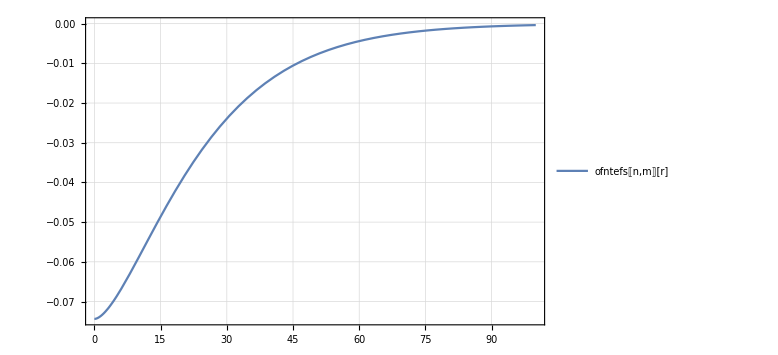
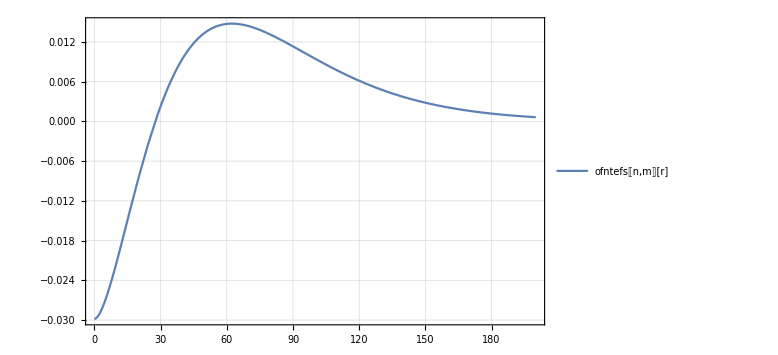
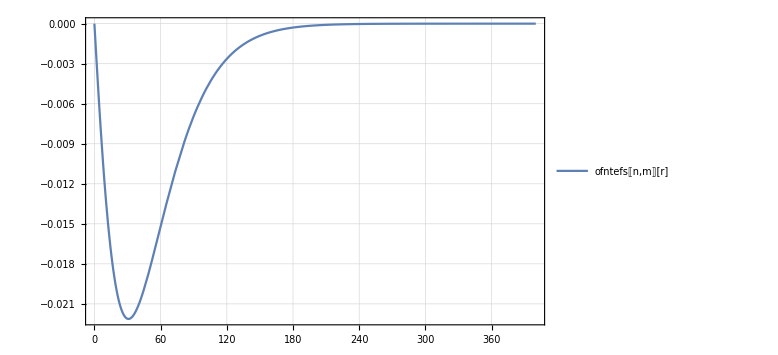
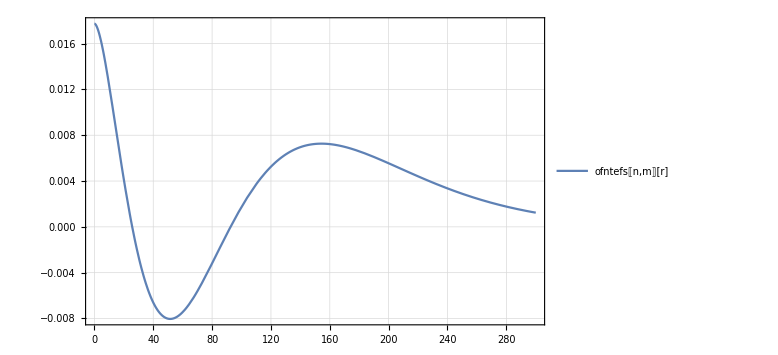
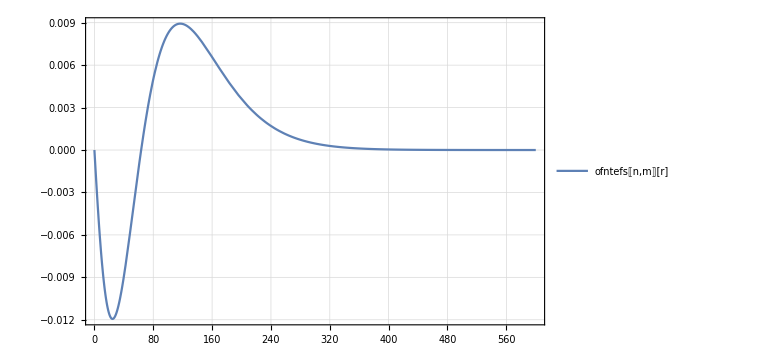
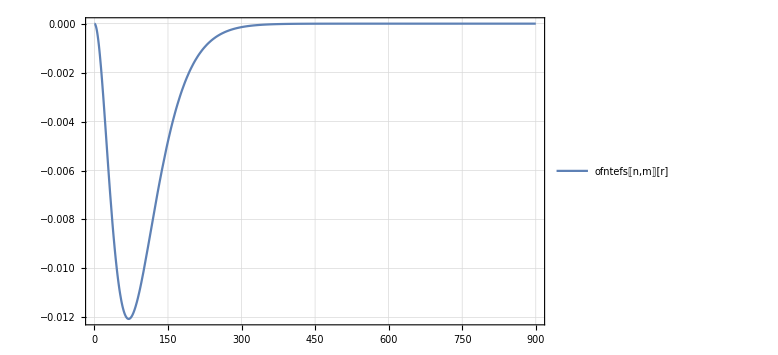
-Graphics- |  | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm@Table[Plot[ofntefs[[n,m]][r],{r,0,100*n*m},ImageSize->Large,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0}],{n,3},{m,n}]
```

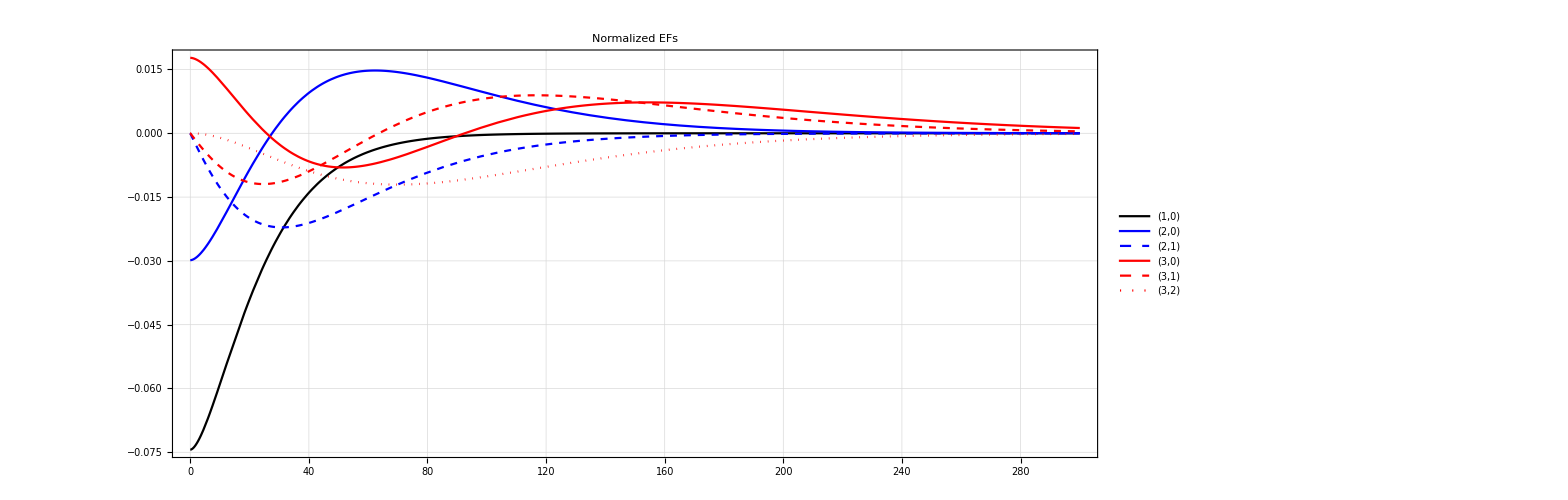

```mathematica
Plot[
Evaluate[(#[r]&/@Flatten[ofntefs])],
{r,0,300},PlotLabel->Style["Normalized EFs",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
```

#### Dig into the interpolating function

```mathematica
ofntefs[[1]]
ofntefs[[1,1]]
```

{Function[{r$},3.08926 InterpolatingFunction[{{0.,1.5708}},3,{Automatic}][ArcTan[r$/10]]]}
 |  |  |  |

Function[{r$},3.08926 InterpolatingFunction[{{0.,1.5708}},{5,4225,0,{3143},{3},0,0,0,0,Indeterminate&,{},{},False},{23[1]},{-0.0240789,-0.0240788,-0.0240788,-0.0240786,-0.0240785,-0.0240783,-0.0240781,-0.0240778,-0.0240775,-0.0240772,-0.0240768,-0.0240764,-0.024076,-0.0240756,-0.0240751,-0.0240746,-0.024074,-0.0240735,-0.0240729,-0.0240723,3103,-4.07366×10^-15,4.3993×10^-16,-2.90718×10^-15,1.31881×10^-15,1.41716×10^-15,-2.71201×10^-15,1.70574×10^-15,-9.33172×10^-17,-2.98837×10^-15,7.44079×10^-16,1.73141×10^-15,-2.46163×10^-15,-4.61743×10^-15,-4.03999×10^-15,4.16042×10^-15,1.77177×10^-15,1.20839×10^-15,2.76751×10^-15,7.43306×10^-16,5.48554×10^-15},{Automatic}][1]]
 |  |  |  |

```mathematica
ofntefs[[1,1,0]]
ofntefs[[1,1,1]]
ofntefs[[1,1,2]]
```

Function

{r$}

3.08926 InterpolatingFunction[…][ArcTan[r$/10]]

```mathematica
ofntefs[[1,1,2,0]]
ofntefs[[1,1,2,1]]
ofntefs[[1,1,2,2]]
```

Times

3.08926

InterpolatingFunction[…][ArcTan[r$/10]]

```mathematica
ofntefs[[1,1,2,2,0]]
ofntefs[[1,1,2,2,1]]
ofntefs[[1,1,2,2,2]]
```

InterpolatingFunction[…]

ArcTan[r$/10]

Part::partw: Part 2 of «1» does not exist.

{{Function[{r$},3.08926 InterpolatingFunction[{{0.,1.5708}},{5,4225,0,{3143},{3},0,0,0,0,Indeterminate&,{},{},False},{23[1]},{-0.0240789,-0.0240788,-0.0240788,-0.0240786,-0.0240785,-0.0240783,-0.0240781,3129,-4.03999×10^-15,4.16042×10^-15,1.77177×10^-15,1.20839×10^-15,2.76751×10^-15,7.43306×10^-16,5.48554×10^-15},{Automatic}][1]]},{1},{1}}⟦1,3,2⟧
 |  |  |  |

```mathematica
ofntefs[[1,1,2,2,0,0]]
ofntefs[[1,1,2,2,0,1]]
ofntefs[[1,1,2,2,0,2]]
ofntefs[[1,1,2,2,0,3]]
ofntefs[[1,1,2,2,0,4]][[;;25]]
ofntefs[[1,1,2,2,0,4]]//Length
ofntefs[[1,1,2,2,0,5]]
```

InterpolatingFunction

{{0.,1.5708}}

{5,4225,0,{3143},{3},0,0,0,0,Indeterminate&,{},{},False}

{NDSolve`FEM`ElementMesh[{{0.,1.5708}},{NDSolve`FEM`LineElement[<1571>]}]}

{-0.0240789,-0.0240788,-0.0240788,-0.0240786,-0.0240785,-0.0240783,-0.0240781,-0.0240778,-0.0240775,-0.0240772,-0.0240768,-0.0240764,-0.024076,-0.0240756,-0.0240751,-0.0240746,-0.024074,-0.0240735,-0.0240729,-0.0240723,-0.0240716,-0.0240709,-0.0240703,-0.0240695,-0.0240688,-0.024068,-0.0240672,-0.0240664,-0.0240655,-0.0240647,-0.0240638,-0.0240629,-0.0240619,-0.024061,-0.02406,-0.024059,-0.0240579,-0.0240569,-0.0240558,-0.0240547,-0.0240536,-0.0240525,-0.0240513,-0.0240501,-0.0240489,-0.0240477,-0.0240464,-0.0240452,-0.0240439,-0.0240426}

3143

{Automatic}

```mathematica
ofntefs[[1,1,2,2,0,3,1,1]]//Length
ofntefs[[1,1,2,2,0,3,1,1]][[;;25]]
ofntefs[[1,1,2,2,0,3,1,2,1,1]]//Length
ofntefs[[1,1,2,2,0,3,1,2,1,1]][[;;25]]
```

3143

{{0.},{0.00099987},{0.00199974},{0.00299961},{0.00399948},{0.00499935},{0.00599922},{0.00699909},{0.00799896},{0.00899883},{0.0099987},{0.0109986},{0.0119984},{0.0129983},{0.0139982},{0.0149981},{0.0159979},{0.0169978},{0.0179977},{0.0189975},{0.0199974},{0.0209973},{0.0219971},{0.022997},{0.0239969}}

1571

{{1,2,1573},{2,3,1574},{3,4,1575},{4,5,1576},{5,6,1577},{6,7,1578},{7,8,1579},{8,9,1580},{9,10,1581},{10,11,1582},{11,12,1583},{12,13,1584},{13,14,1585},{14,15,1586},{15,16,1587},{16,17,1588},{17,18,1589},{18,19,1590},{19,20,1591},{20,21,1592},{21,22,1593},{22,23,1594},{23,24,1595},{24,25,1596},{25,26,1597}}

#### OK - large-r behavior is a possible issue.

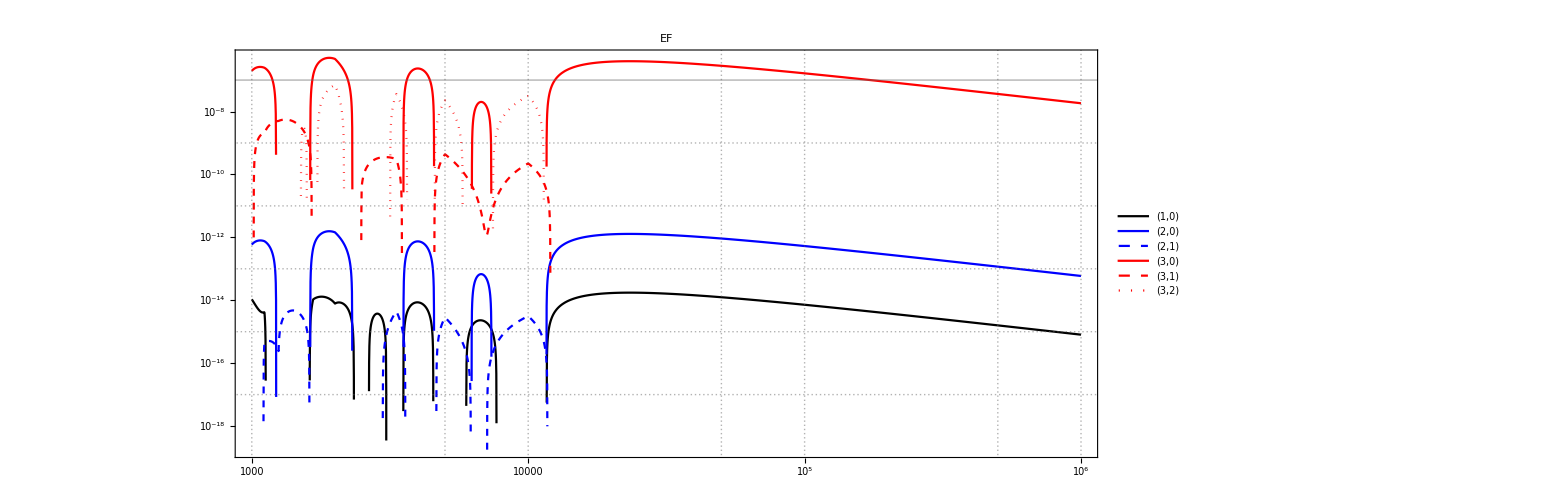

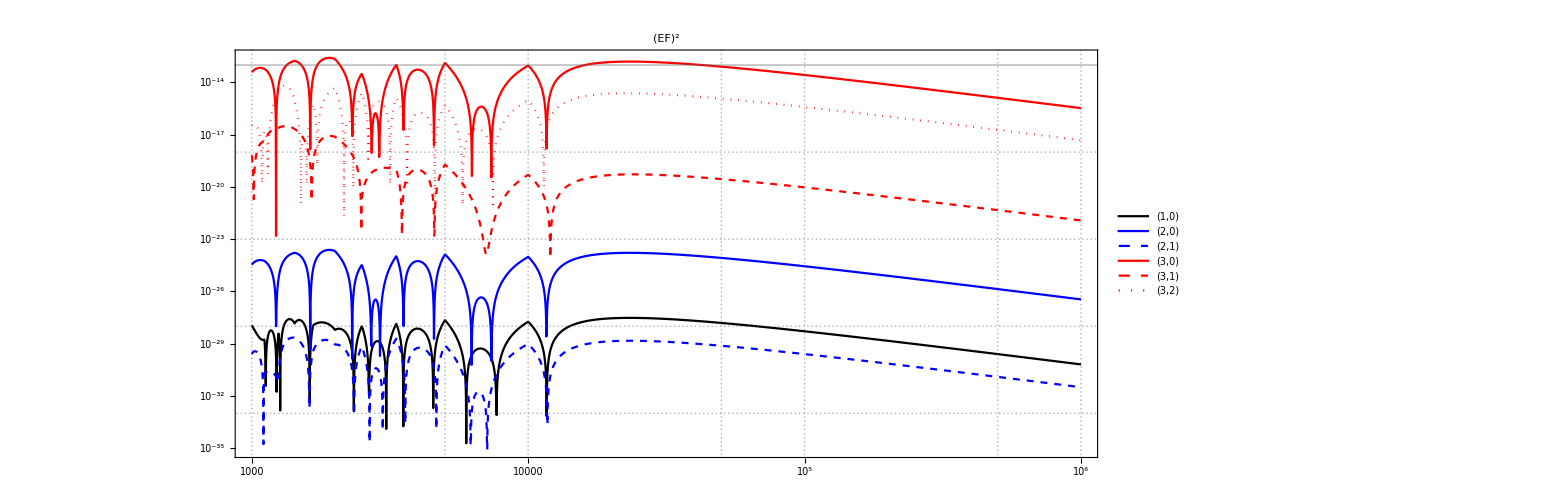

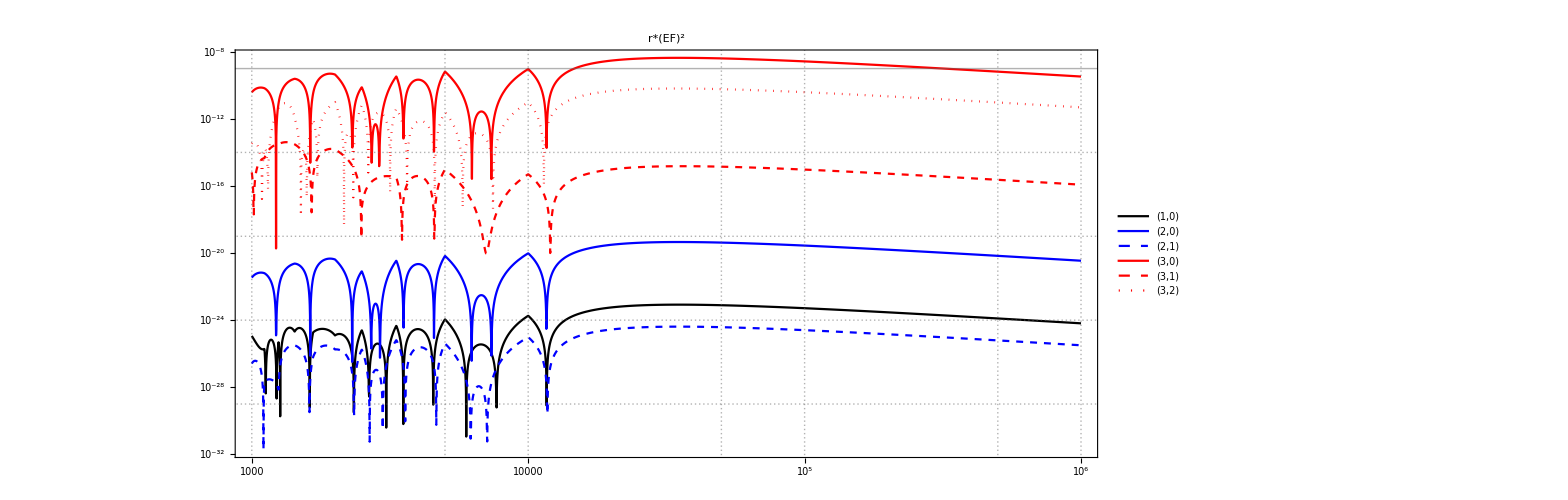

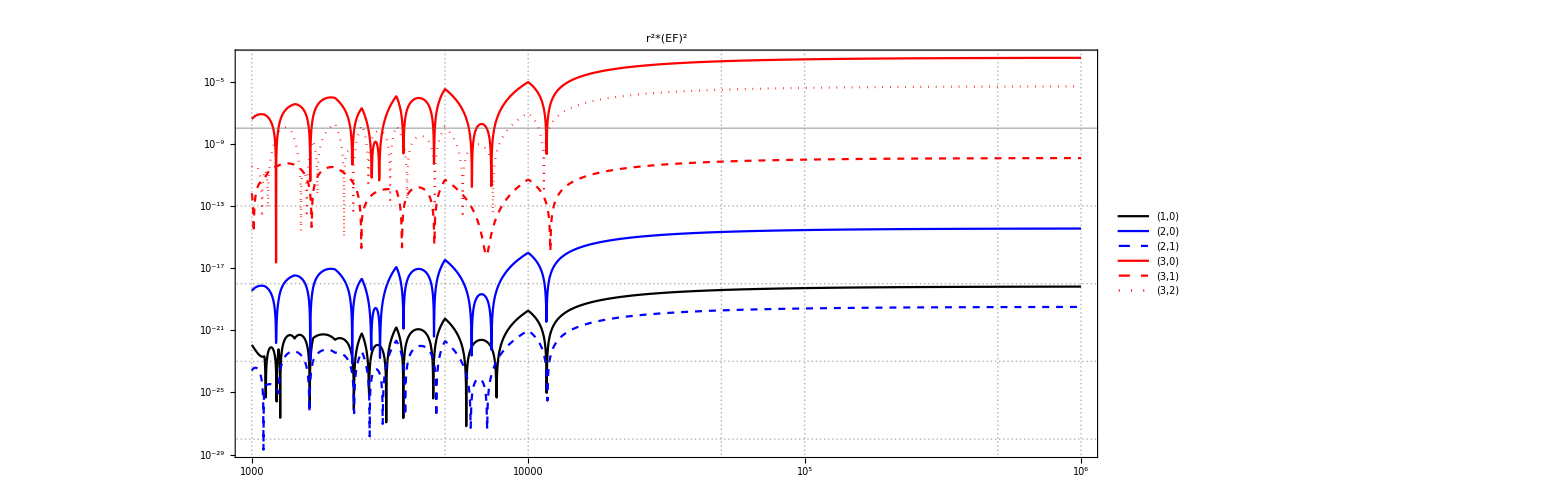

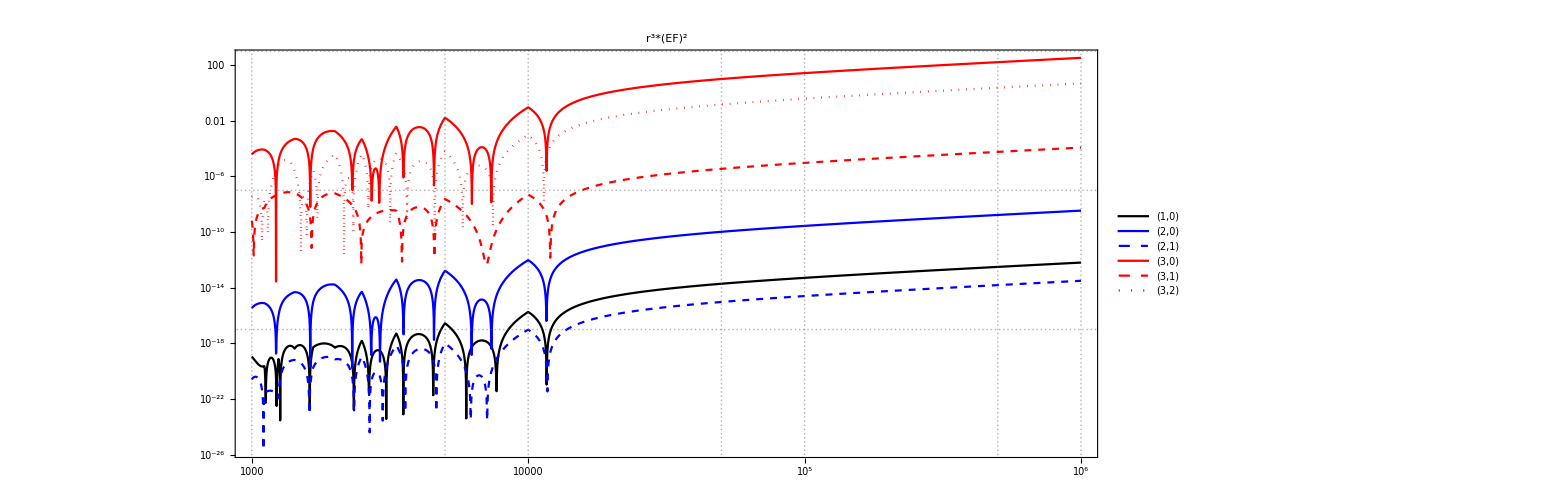

```mathematica
Plot[
Evaluate[((#[r])&/@Flatten[ofntefs])],
{r,1000,10^6},ScalingFunctions->{"Log","Log"},PlotLabel->Style["EF",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
Plot[
Evaluate[((#[r]^2)&/@Flatten[ofntefs])],
{r,1000,10^6},ScalingFunctions->{"Log","Log"},PlotLabel->Style["(EF)^2",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
Plot[
Evaluate[((r)*(#[r]^2)&/@Flatten[ofntefs])],
{r,1000,10^6},ScalingFunctions->{"Log","Log"},PlotLabel->Style["r*(EF)^2",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
Plot[
Evaluate[((r^2)*(#[r]^2)&/@Flatten[ofntefs])],
{r,1000,10^6},ScalingFunctions->{"Log","Log"},PlotLabel->Style["r^2*(EF)^2",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
Plot[
Evaluate[((r^3)*(#[r]^2)&/@Flatten[ofntefs])],
{r,1000,10^6},ScalingFunctions->{"Log","Log"},PlotLabel->Style["r^3*(EF)^2",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
```

#### √(<r^2>)

```mathematica
ofntefs=Normal@ofdrop["efs"];
```

```mathematica
Table[UnitConvert[Quantity[
Sqrt[
NIntegrate[(r^3)*(ofntefs[[n,m]][r])^2,{r,0,10^6},Evaluate@FilterRules[{ofnintopts},Options[NIntegrate]]]],
"BohrRadius"],"Nanometers"],{n,3},{m,n}]
```

{{1.28486 nm},{4.51497 nm,3.08762 nm},{677.435 nm,7.4235 nm,81.7561 nm}}

Yeaaaahhhhh that value of √(<r^2>) for (3,0) looks suuuuuper wrong. Also the EFs should be MORE spread out as m increases for a given n

```mathematica
Table[UnitConvert[Quantity[
Sqrt[
NIntegrate[(r^3)*(ofntefs[[n,m]][r])^2,{r,0,10^xp},Evaluate@FilterRules[{ofnintopts},Options[NIntegrate]]]],
"BohrRadius"],"Nanometers"],{xp,3,6},{n,3},{m,n}]
```

{{{1.28486 nm},{4.51497 nm,3.08762 nm},{9.31071 nm,7.41248 nm,5.5971 nm}},{{1.28486 nm},{4.51497 nm,3.08762 nm},{9.32139 nm,7.41248 nm,5.59727 nm}},{{1.28486 nm},{4.51497 nm,3.08762 nm},{55.9323 nm,7.41256 nm,8.70884 nm}},{{1.28486 nm},{4.51497 nm,3.08762 nm},{677.435 nm,7.4235 nm,81.7561 nm}}}

```mathematica
Table[
Sqrt[
NIntegrate[(r^3)*(ofntefs[[n,m]][r])^2,{r,0,10^6},Evaluate@FilterRules[{ofnintopts},Options[NIntegrate]]]],
{n,3},{m,n}]
```

{{24.2803},{85.3206,58.3476},{12801.7,140.284,1544.97}}

```mathematica
Table[
Sqrt[
NIntegrate[(r^3)*(ofntefs[[n,m]][r])^2,{r,0,10^6},
Evaluate@FilterRules[{ofnintopts},Options[NIntegrate]]]
],
{n,3},{m,n}]
```

{{24.2803},{85.3206,58.3476},{12801.7,140.284,1544.97}}

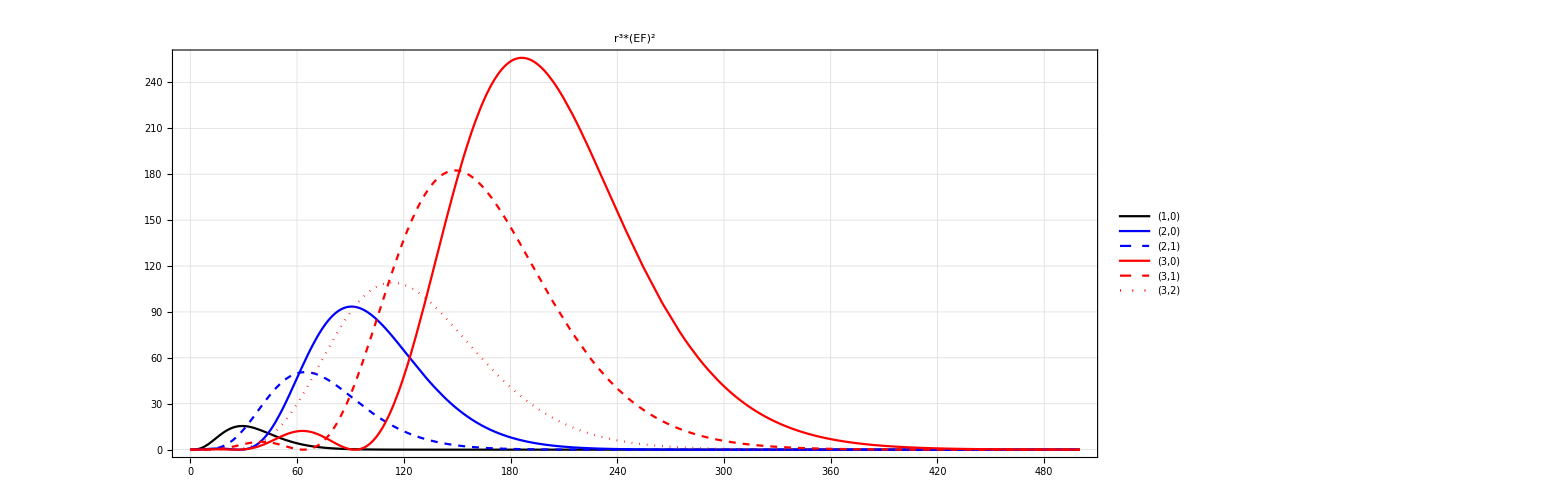

-Graphics-

```mathematica
Plot[
Evaluate[((r^3)*(#[r]^2)&/@Flatten[ofntefs])],
{r,0,500},PlotLabel->Style["r^3*(EF)^2",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
Plot[
Evaluate[((r^3)*(#[r]^2)&/@Flatten[ofntefs])],
{r,1000,10^6},ScalingFunctions->{"Log","Log"},PlotLabel->Style["r^3*(EF)^2",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above]
]
```

#### a_b

```mathematica
Table[UnitConvert[Quantity[
NMaximize[{Abs[r*ofntefs[[n,m]][r]], 0≤r≤3000},r,Method->"SimulatedAnnealing"],
"BohrRadius"],"Nanometers"],{n,3},{m,n}]
xabpts=Flatten[Table[
{Last[#[[2,1]]],#[[1]]}&@NMaximize[{r*(ofntefs[[n,m]][r]^2), 0≤r≤1000},r,Method->"SimulatedAnnealing"],
{n,3},{m,n}],1]
```

{{{0.0414307 nm,{0.0529177211 (r→21.3448) nm}}},{{0.0553495 nm,{0.0529177211 (r→80.4474) nm}},{0.0490273 nm,{0.0529177211 (r→53.6138) nm}}},{{0.0630441 nm,{0.0529177211 (r→174.664) nm}},{0.0597758 nm,{0.0529177211 (r→137.223) nm}},{0.0536601 nm,{0.0529177211 (r→99.024) nm}}}}

{{12.7929,0.0361132},{70.9066,0.0144787},{42.4497,0.0179024},{163.953,0.0083889},{126.407,0.0096891},{84.5063,0.0112161}}

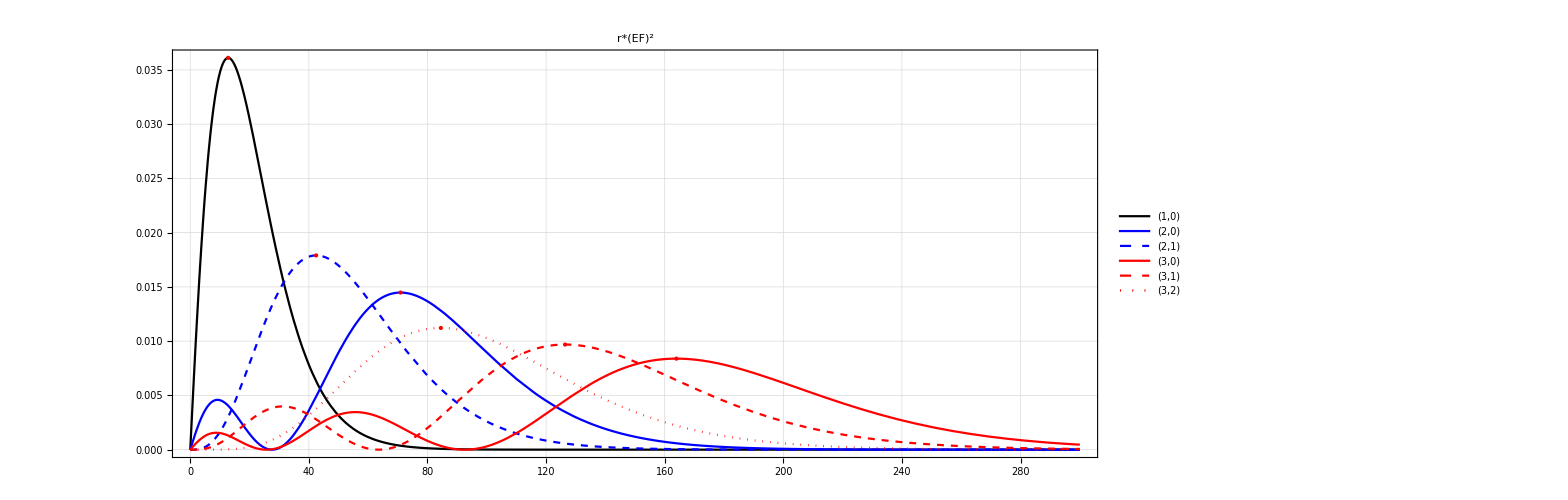

```mathematica
Plot[
Evaluate[(r*(#[r]^2)&/@Flatten[ofntefs])],
{r,0,300},PlotLabel->Style["r*(EF)^2",24,Black],
ImageSize->{1200,500},AspectRatio->5/12,PlotTheme->"Detailed",PlotRange->Full,Axes->True,AxesOrigin->{0,0},
PlotStyle->{Directive[Black,Thick],Directive[Blue,Thick],Directive[Blue,Thick,Dashed],Directive[Red,Thick],Directive[Red,Thick,Dashed],Directive[Red,Thick,Dotted]},
PlotLegends->Placed[{"(1,0)","(2,0)","(2,1)","(3,0)","(3,1)","(3,2)"},Above],
Epilog->{
{Red,PointSize[Large],Point[xabpts]}
}
]
```

### Get list of files to import using FileNames[]

```mathematica
FileNames["1dp_l*.m",cl1d]//Length
```

3626

```mathematica
FileNames["1dp_l*.m",cl1d];
{%//Length,sset1d=%[[;;30]]}
```

{3010,{cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.15.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.1.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.25.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.2.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.35.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.3.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.45.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.4.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.55.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.5.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.65.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.6.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.75.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.7.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.85.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.8.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.95.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-0.9.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.05.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.15.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.1.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.25.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.2.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.35.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.3.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.45.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.4.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1.5.m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1.5_mu-1..m,cl-1dp-v1/1dp_l-4._chi-4.5_kappa-1._mu-0.15.m}}

### How to categorize data before/during/after import?

```mathematica
Map[
Module[
{
fullpath=#,
fname=StringTake[StringSplit[#,"/"][[2]],{1,-3}],
pkeys,pvals},
({pkeys=#[[;;,1]],pvals=#[[;;,2]]}&)@StringSplit[StringExtract[fname,"_"->2;;],"-"];
(*AssociationThread[pkeys,pvals]*)
StringExtract[fname,"_"->2;;]
]&
]@sset1d
```

{{l-4.,chi-4.5,kappa-1.5,mu-0.15},{l-4.,chi-4.5,kappa-1.5,mu-0.1},{l-4.,chi-4.5,kappa-1.5,mu-0.25},{l-4.,chi-4.5,kappa-1.5,mu-0.2},{l-4.,chi-4.5,kappa-1.5,mu-0.35},{l-4.,chi-4.5,kappa-1.5,mu-0.3},{l-4.,chi-4.5,kappa-1.5,mu-0.45},{l-4.,chi-4.5,kappa-1.5,mu-0.4},{l-4.,chi-4.5,kappa-1.5,mu-0.55},{l-4.,chi-4.5,kappa-1.5,mu-0.5},{l-4.,chi-4.5,kappa-1.5,mu-0.65},{l-4.,chi-4.5,kappa-1.5,mu-0.6},{l-4.,chi-4.5,kappa-1.5,mu-0.75},{l-4.,chi-4.5,kappa-1.5,mu-0.7},{l-4.,chi-4.5,kappa-1.5,mu-0.85},{l-4.,chi-4.5,kappa-1.5,mu-0.8},{l-4.,chi-4.5,kappa-1.5,mu-0.95},{l-4.,chi-4.5,kappa-1.5,mu-0.9},{l-4.,chi-4.5,kappa-1.5,mu-1.05},{l-4.,chi-4.5,kappa-1.5,mu-1.15},{l-4.,chi-4.5,kappa-1.5,mu-1.1},{l-4.,chi-4.5,kappa-1.5,mu-1.25},{l-4.,chi-4.5,kappa-1.5,mu-1.2},{l-4.,chi-4.5,kappa-1.5,mu-1.35},{l-4.,chi-4.5,kappa-1.5,mu-1.3},{l-4.,chi-4.5,kappa-1.5,mu-1.45},{l-4.,chi-4.5,kappa-1.5,mu-1.4},{l-4.,chi-4.5,kappa-1.5,mu-1.5},{l-4.,chi-4.5,kappa-1.5,mu-1.},{l-4.,chi-4.5,kappa-1.,mu-0.15}}

# 2DC v2.1 (working with)

## Done (as of 08/05):

## All EVs

### 08/07: Try re-sizing Figs. 7.1 & 7.2 so they are more readable and take up less space.

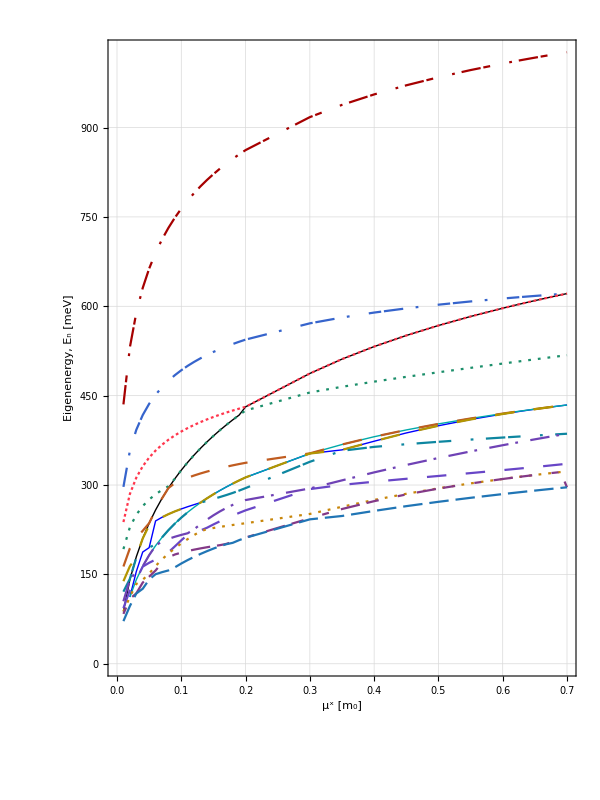
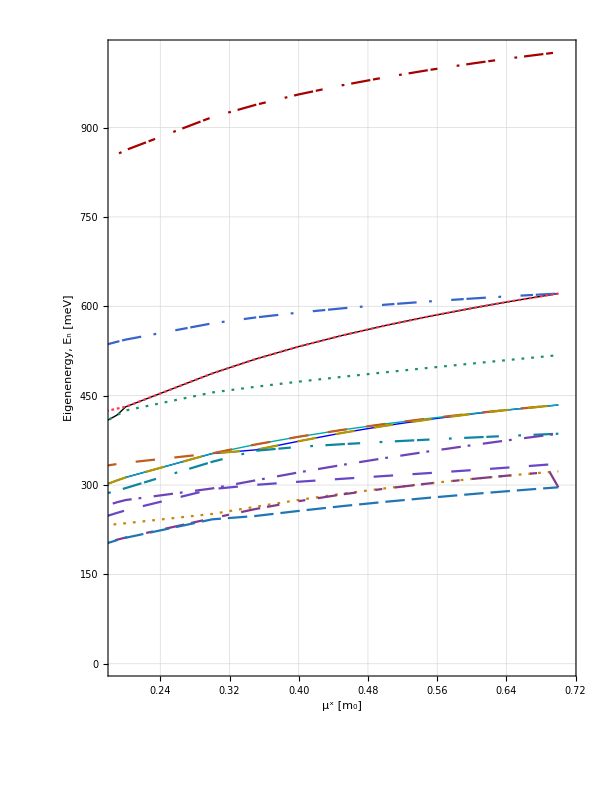
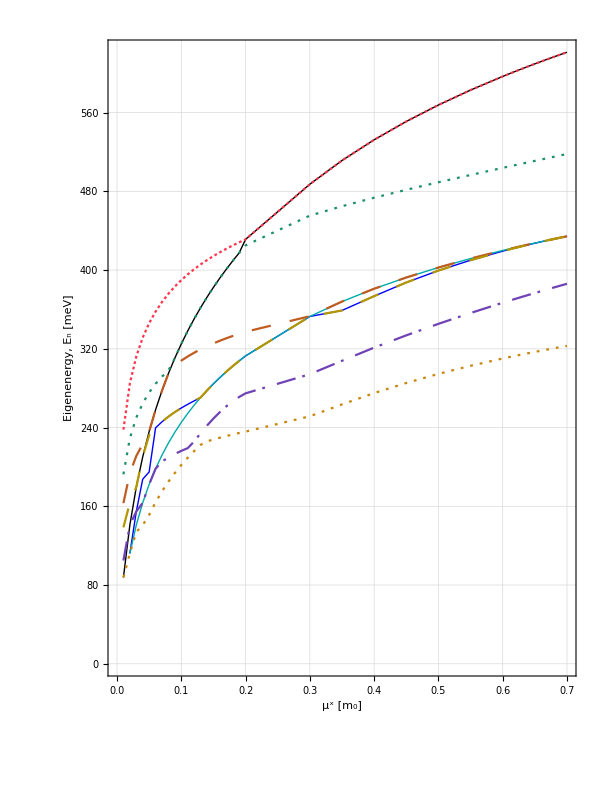
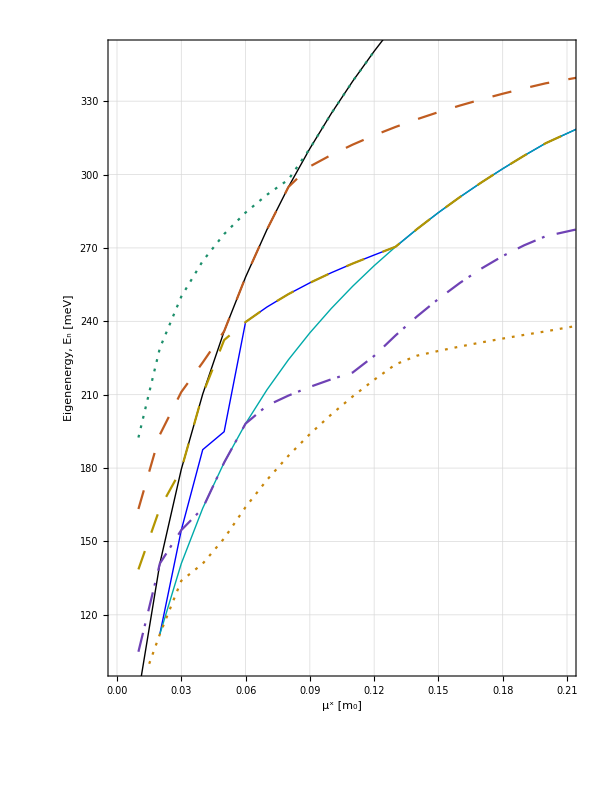

```mathematica
Normal@fl2d[
1,
Values
/*
(Module[
{flatdata=Flatten[#,{{3},{1},{2}}]},
Map[
ListLinePlot[
#data,
PlotTheme->"Detailed",
ImageSize->{600,800},AspectRatio->Full,
PlotRange->#plra,
FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},
LabelStyle->labsty/.{24->22},
PlotStyle->#plst,
(*PlotMarkers->marksize[Flatten[{emmarks4,"△","▽"}],24],*)
PlotLegends->None,
Prolog->{
{Black,Thick,Line[Flatten[{{flatdata[[10,1]]},{flatdata[[8,2]]},flatdata[[6,3;;4]],flatdata[[5,5;;8]],flatdata[[4,9;;19]],flatdata[[3,20;;]]},1]]},
{Blue,Line[Flatten[{{flatdata[[10,2]]},{flatdata[[8,3]]},flatdata[[7,4;;5]],flatdata[[6,6;;12]],flatdata[[6,13;;20]],flatdata[[6,21;;]]},1]]},
{Darker@Cyan,Line[Flatten[{{flatdata[[10,2]]},{flatdata[[9,3]]},flatdata[[8,4;;6]],flatdata[[7,7;;12]],flatdata[[6,13;;21]],flatdata[[5,22;;]]},1]]}
}
]&,
{
<|"data"->flatdata,"plra"->Full,"plst"->randash|>,
<|"data"->flatdata,"plra"->{{0.19,0.71},Automatic},"plst"->randash|>,
<|"data"->flatdata[[{3,4,5,6,8,10}]],"plra"->Full,"plst"->randash[[{3,4,5,6,8,10}]]|>,
<|"data"->flatdata[[{4,5,6,8,10}]],"plra"->{{0,0.21},{100,350}},"plst"->randash[[{4,5,6,8,10}]]|>
}
]
]&),
{
"mx"/*(Table[#,{12}]&),
"evs"/*Values/*Abs/*QuantityMagnitude
}
]
```

#### Tracing the n_x states

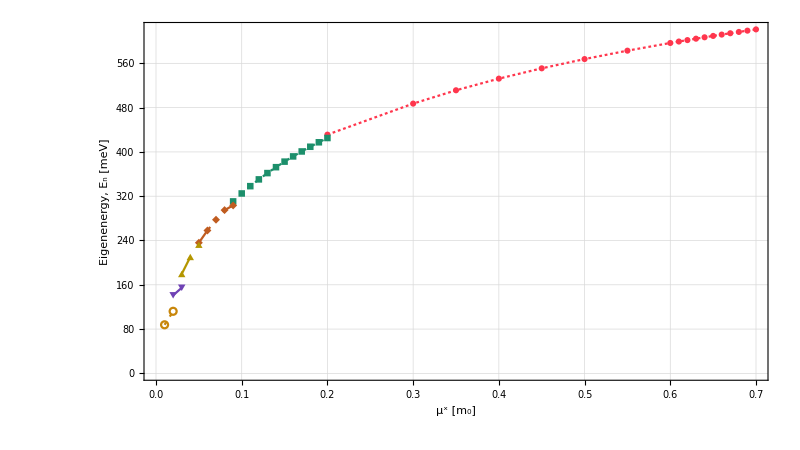

```mathematica
Normal@fl2d[
1,
Values
/*
(Module[
{allflatdata=Flatten[#,{{3},{1},{2}}]},
ListLinePlot[
{
allflatdata[[3,20;;]],
allflatdata[[4,9;;20]],
allflatdata[[5,5;;9]],
allflatdata[[6,3;;5]],
allflatdata[[8,2;;3]],
allflatdata[[10,1;;2]]
},
PlotTheme->"Detailed",ImageSize->0.5*{1600,900},AspectRatio->Full,
FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},LabelStyle->labsty,
PlotStyle->randash[[{3,4,5,6,8,10}]],
PlotRange->Full,
PlotMarkers->Automatic,
PlotLegends->Placed[PointLegend[
Automatic,
Table[TraditionalForm@StringForm["E_(`1`)",ToString@i],{i,12}],
LegendLayout->(TableForm[
Map[
Row,
Transpose@ArrayReshape[#,{6,2,2}],
{2}
]
]&)
],Above]
]
]&),
{
"mx"/*(Table[#,{12}]&),
"evs"/*Values/*Abs/*QuantityMagnitude
}
]
```

### Figs. 8.1 & 8.2 in Diss (as of 08/05): EVs vs. μ^x

#### Fig. 8.1 (All EVs)

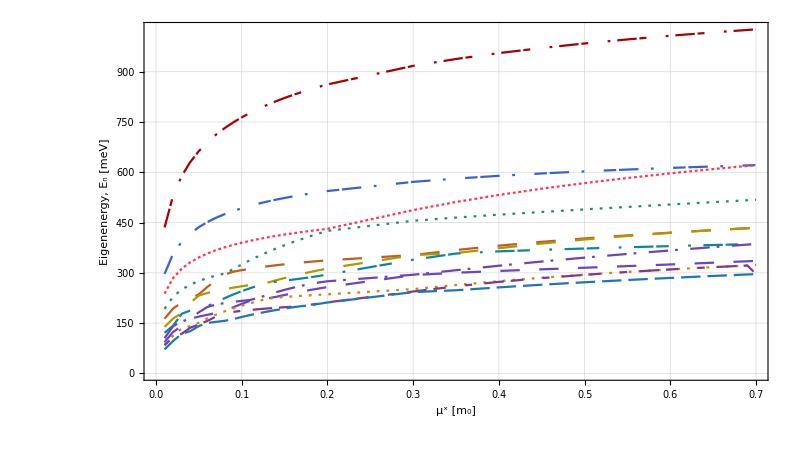

../../../dis/figs/d_leg_all-en-vs-mx_my-07.pdf

```mathematica
Normal@fl2d[
1,
Values
/*
(ListLinePlot[
Flatten[#,{{3},{1},{2}}],
PlotTheme->"Detailed",ImageSize->0.5*{1600,900},AspectRatio->Full,(*PlotLabel->"All eigenenergies vs. μ^x; μ^y = 0.7 m_0",*)FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},LabelStyle->labsty,
PlotStyle->randash,
(*PlotMarkers->marksize[Flatten[{emmarks4,"△","▽"}],24],*)
PlotLegends->Placed[LineLegend[
Automatic,
Table[TraditionalForm@StringForm["E_(`1`)",ToString@i],{i,12}],
LegendLayout->(TableForm[
Map[
Row,
Transpose@ArrayReshape[#,{6,2,2}],
{2}
]
]&)
],Above]
]&),
{
"mx"/*(Table[#,{12}]&),
"evs"/*Values/*Abs/*QuantityMagnitude
}
]
Export[dfd<>"d_leg_all-en-vs-mx_my-07.pdf",%[[2,1]]]
```

#### Fig. 8.2 (Zoomed on lower EVs)

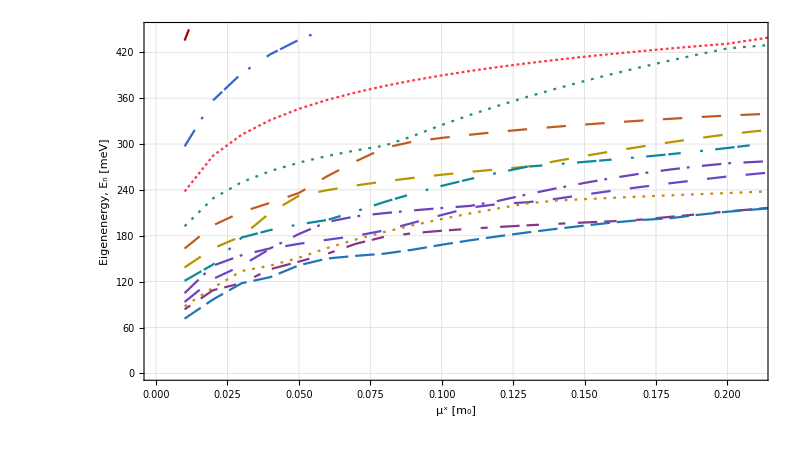

```mathematica
Normal@fl2d[
1,
Values
/*
(ListLinePlot[
Flatten[#,{{3},{1},{2}}],
PlotTheme->"Detailed",ImageSize->0.5*{1600,900},AspectRatio->Full,
FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},LabelStyle->labsty,
PlotStyle->randash,
PlotRange->{{0,0.21},{0,450}},
PlotLegends->Placed[PointLegend[
Automatic,
Table[TraditionalForm@StringForm["E_(`1`)",ToString@i],{i,12}],
LegendLayout->(TableForm[
Map[
Row,
Transpose@ArrayReshape[#,{6,2,2}],
{2}
]
]&)
],Above]
]&),
{
"mx"/*(Table[#,{12}]&),
"evs"/*Values/*Abs/*QuantityMagnitude
}
]
```

### E_b vs. μ^(x/y) and μ^0 (ContourPlot)

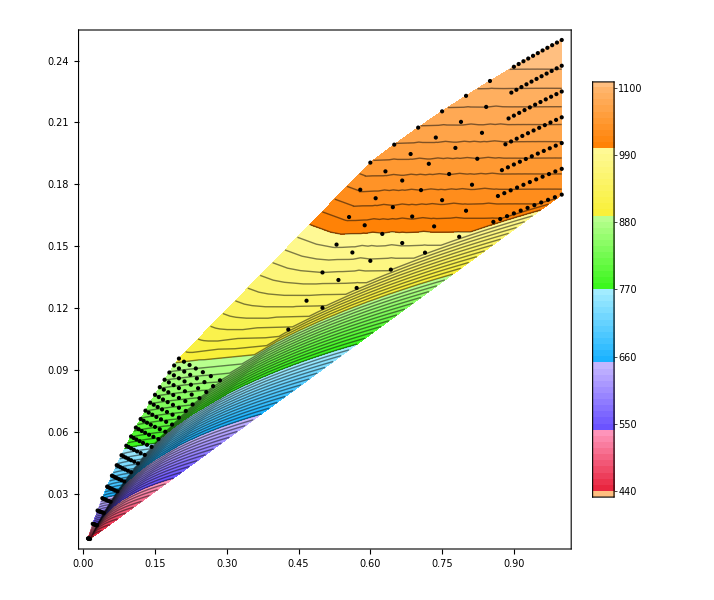

```mathematica
fl2d[
Values
/*
(ListContourPlot[
Flatten[#,1],
ImageSize->0.5*{1200,1200},
PlotTheme->"Detailed",
ColorFunction->"BrightBands",
Contours->Table[400+10*i,{i,0,70}],
Epilog->{
{Black,Point[Flatten[#,1][[;;,;;2]]]}
}
]&),
Values,
{
"mxy",
"m0",
"evs"/*"i1"/*Abs/*QuantityMagnitude
}
]
```

## Array Plots (for optical selection rules)

### Fun with manipulate!

```mathematica
Normal@fl2d[
1,
Values,
{
"fox"/*Values/*Map[Values],
"foy"/*Values/*Map[Values],
{"mx","my"},
"evs"/*Values
}
/*
(Module[{data=#[[;;2]],evs=#[[4]],params=#[[3]]},
ArrayPlot[
Chop[PadLeft[Subtract@@data,{11,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Gray,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
],
ImageSize->{800,800},
PlotLabel->TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],
PlotRange->{{1,12},{1,12}},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->MapAt[
Partition[Riffle[#,evs],2]&,
Transpose@Table[{i,i,i,i},{i,12}],
{3}
],
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"f\"]",None},{"Initial Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"i\"]",None}}
]]&)
];
Manipulate[
%[[i]],
{i,1,37,1}
]
```

### Saving (a) figure(s) is tricky because just one of these plots doesn’t tell the whole story.

#### Make a grid of these plots at different values of μ^x corresponding to the “anti-crossing” points (Diss fig. 08/01)

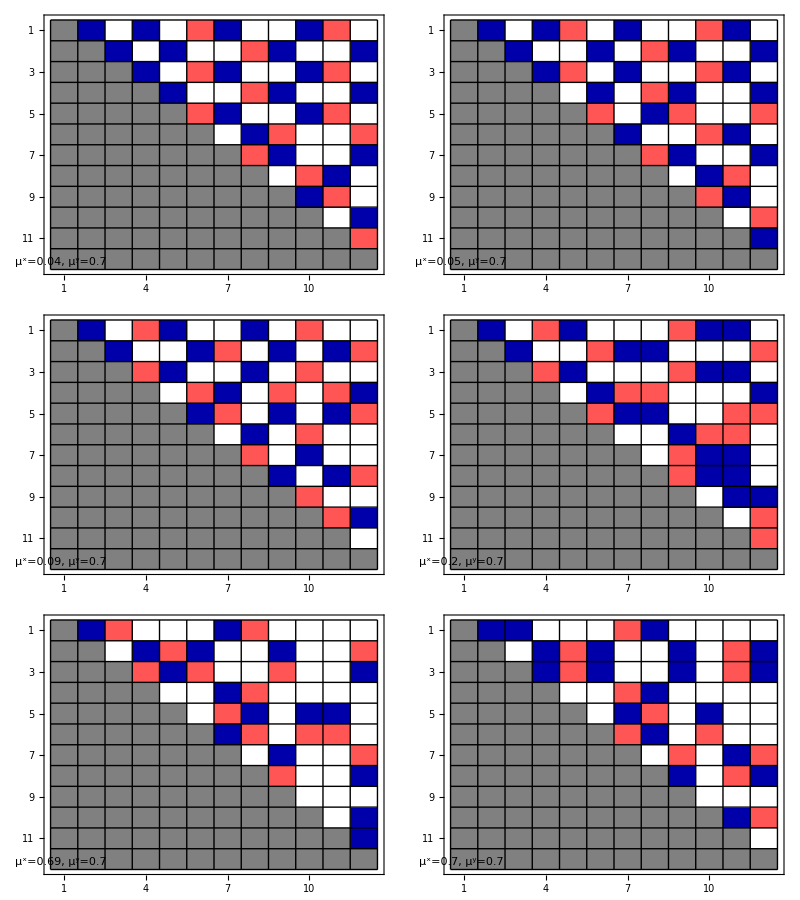
-Graphics-Initial Eigenstate, n_iFinal Eigenstate, n_fEigenenergy, E_n [meV]

../../../dis/figs/d_plt-grid_arrplt-mx-prog_my-07.pdf

```mathematica
Labeled[Grid[ArrayReshape[
Normal@fl2d[
1,
{4,5,9,20,-2,-1}/*Values,
{
"fox"/*Values/*Map[Values]/*Append[{}],
"foy"/*Values/*Map[Values]/*Append[{}],
{"mx","my"},
"evs"/*Values/*Abs/*QuantityMagnitude
}
/*
(Module[{data=#[[;;2]],evs=Map[NumberForm[#,{5,1}]&,#[[4]]],params=#[[3]]},
ArrayPlot[
Chop[PadLeft[Subtract@@data,{12,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Gray,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->None(*Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
]*),
ImageSize->{800,800},
(*PlotLabel->TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],*)
PlotRange->{{1,12},{1,12}},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->MapAt[
Partition[Riffle[#,evs],2]&,
Transpose@Table[{i,i,i,i},{i,12}],
{3}
],
LabelStyle->labsty/.{24->32},
Epilog->{
Inset[Framed[
Style[TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],labsty/.{24->32}],
Background->White,RoundingRadius->5],Scaled@{0.05,0.05},Scaled@{0.05,0.05}]
}(*,
FrameLabel->{{"Final Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"f\"]",None},{"Initial Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"i\"]","Eigenenergy, E_n_i [meV]"}}*)
]]&)
],
{3,2}
],
Spacings->5
],
{Rotate["Initial Eigenstate, n_i",90Degree],"Final Eigenstate, n_f",Rotate["Eigenenergy, E_n [meV]",-90Degree]},{Left,Bottom,Right},LabelStyle->Directive[50,Black,FontFamily->"Arial"]]
Export[dfd<>"d_plt-grid_arrplt-mx-prog_my-07.pdf",%]
```

## Try to do a manipulate/animation but with EFs instead (danger zone??)

### Figure out a better way to show/browse the plots as opposed to dumping them all into a massive grid (also: import ef table here)

```mathematica
eftab=Import[dfd<>"d_37x12-raw-eftab.m"];
```

#### Scrub through 37 values of μ^x, each showing 1-12 in a 2x6 grid

```mathematica
Manipulate[
TableForm@ArrayReshape[
Show[#,ImageSize->{350,350}]&/@eftab[[i,;;]],
{2,6}
],
{i,1,37,1}
]
```

#### Scrub through 1-12, show all μ^x in a 6x6+1 grid.

```mathematica
Manipulate[
TableForm@Map[
Show[#,ImageSize->{350,200}]&,
eftab[[mxi-2;;mxi+2,n-2;;n+2]],
{2}
],
{n,3,10,1},
{mxi,3,35,1}
]
```

### Problems solved, lets do that research.

#### [Re-]/Import/Clear EF data

```mathematica
Remove@allmx
```

```mathematica
LightYellow~bg~bgb@MemoryInUse[]
AbsoluteTiming[allmx=Normal@fl2d[
Values/*1,
Values,
"nefs"/*Import
];]
allmx//Dimensions
allmx[[1,1]]
bgb@ByteCount[allmx]
LightRed~bg~bgb@MemoryInUse[]
allmxevs=Normal@fl2d[Values/*1,Values,"evs"/*Values/*Abs];
Dimensions@allmxevs
allmxmx=Normal@fl2d[Values/*1,Values,"mx"];
%//Dimensions
```

0.2662 GB

{61.3885,Null}

{37,12}

Function[{x$,y$},2.13457 InterpolatingFunction[{{-1.5708,1.5708},{-1.5708,1.5708}},{5,4225,0,{30401,0},{3,0},0,0,0,0,Indeterminate&,{},{},False},{1},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,30312,0.,2.96942×10^-6,0.,2.88679×10^-6,0.,2.79458×10^-6,0.,2.69151×10^-6,0.,2.57613×10^-6,0.,2.44683×10^-6,0.,2.30183×10^-6,0.,2.1393×10^-6,0.,1.95739×10^-6,0.,1.75455×10^-6,0.,1.52991×10^-6,0.,1.28402×10^-6,0.,1.02003×10^-6,0.,7.45468×10^-7,0.,4.74498×10^-7,0.,2.30457×10^-7,0.,4.69564×10^-8,0.,-3.84252×10^-8,0.,-2.35381×10^-8,0.,1.28204×10^-9,0.,-6.45326×10^-10,0.,0.},{Automatic}][1]]
 |  |  |  |

2.75472 GB

2.98024 GB

{37,12}

{37}

When only keeping first 8 EFs, 70.7 sec to load and takes up 1.36 GB.

{70.7147,Null}

1.36887 GB

{37,6}

Function[{x$,y$},2.13457 1]
 |  |  |  |

{37,6}

{37}

#### Make the plots (~10 min.) :: raw output of 37x12 matrix of ListLinePlot[]’s exported

```mathematica
eftab=Table[
Block[
{oneef=allmx[[mxi,ii]],oneev=allmxevs[[mxi,ii]],mxval=allmxmx[[mxi]],tb=(pio2-0.002),ds},
ds=2*tb/50;
Block[
{data=Flatten[ParallelTable[{{10*Tan[s],oneef[10*Tan[s],0]},{10*Tan[s],oneef[0,10*Tan[s]]},{10*Tan[s],oneef[10*Tan[s],10]},{10*Tan[s],oneef[10,10*Tan[s]]},{10*Tan[s],oneef[10*Tan[s],-10]},{10*Tan[s],oneef[-10,10*Tan[s]]}},{s,-tb,tb,ds}],{{2},{1},{3}}]},
ListLinePlot[
Evaluate[data],
PlotTheme->"Detailed",
Axes->True,AxesOrigin->{0,0},AxesStyle->Directive[Black,Thick],FrameTicks->None,
ImageSize->{500,500},AspectRatio->Full,
PlotLabel->Style[tssf["mx = `1` ; `2` ; E_(`2`) = `3`",mxval,ii,oneev//QuantityMagnitude],20,Black],
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dotted},{Thick,Blue,Dotted},{Thick,Red,DotDashed},{Thick,Blue,DotDashed}},
PlotMarkers->marksize[feriff,18]
]
]],
{mxi,37},
{ii,12}
];
```

```mathematica
Export[dfd<>"d_37x12-raw-eftab.m",eftab];
```

### OK - solved memory issues by using Block[] instead of Module[]. And the grid of plots itself uses like 80 MB so that’s not an issue.

Waitwaitwaitwaitwait... I think I should be using Block instead of Module...

Blockpaclet:ref/Block allows you to set up an environment in which the values of variables can temporarily be changed.

When you execute a block, values assigned to x, y, … are cleared. When the execution of the block is finished, the original values of these symbols are restored.

Blockpaclet:ref/Block affects only the values of symbols, not their names.

Initial values specified for x, y, … are evaluated before x, y, … are cleared.

```mathematica
Tan[pio2-0.002]
```

499.999

```mathematica
$HistoryLength
```

∞

```mathematica
(*gridWheaders[*)
LightPink~bg~bgb@MemoryInUse[]
Column[
AbsoluteTiming@GraphicsGrid[
Table[
Block[
{oneef=allmx[[mxi,ii]],oneev=allmxevs[[mxi,ii]],mxval=allmxmx[[mxi]],tb=(pio2-0.002),ds},
ds=2*tb/150;
Block[
{data=Flatten[ParallelTable[{{10*Tan[s],oneef[10*Tan[s],0]},{10*Tan[s],oneef[0,10*Tan[s]]},{10*Tan[s],oneef[10*Tan[s],10]},{10*Tan[s],oneef[10,10*Tan[s]]},{10*Tan[s],oneef[10*Tan[s],-10]},{10*Tan[s],oneef[-10,10*Tan[s]]}},{s,-tb,tb,ds}],{{2},{1},{3}}]},
ListLinePlot[
Evaluate[data],
PlotTheme->"Detailed",
AxesOrigin->{0,0},
AxesStyle->Directive[Black,Thick],
FrameTicks->None,
PlotLabel->Style[tssf["mx = `1` ; `2` ; E_(`2`) = `3`",mxval,ii,oneev//QuantityMagnitude],20,Black],
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dotted},{Thick,Blue,Dotted},{Thick,Red,DotDashed},{Thick,Blue,DotDashed}}
]
]],
{mxi,37},
{ii,6}
],
ImageSize->{2400,37*700}
],
Center]
LightGreen~bg~AbsoluteTiming@bgb@ByteCount[%]
LightCyan~bg~bgb@MemoryInUse[]
LightRed~bg~bgb@MaxMemoryUsed[]
```

1.65739 GB

992.742
-Graphics-

{0.002657,0.0089733 GB}

1.66657 GB

1.68649 GB

### Still can’t really wrap my head around how the EFs move around w.r.t. μ^x

#### TIL: Don’t pass lists of data into paralleltable - isolate each list element, then call the parallel functions

```mathematica
ParallelTable[
{
{10*Tan[s],allmx[[1,1]][10*Tan[s],x0]},
{10*Tan[s],allmx[[1,1]][x0,10*Tan[s]]}
},
{x0,{-10,10,0}},
{s,-(pio2-0.1),(pio2-0.1),2*(pio2-0.1)/50}
]//Dimensions//AbsoluteTiming
```

{13.6104,{3,51,2,2}}

^^^^ CAUTION - THIS PARALLELTABLE JUST ATE UP LIKE 8 GB of RAM

{3,51,2,2}

IDEA: define the [[1,1]] element as a separate variable, then use the variable inside parallel table

```mathematica
oneefpartest=allmx[[1,1]];
ParallelTable[
{
{10*Tan[s],oneefpartest[10*Tan[s],x0]},
{10*Tan[s],oneefpartest[x0,10*Tan[s]]}
},
{x0,{-10,10,0}},
{s,-(pio2-0.1),(pio2-0.1),2*(pio2-0.1)/50}
]//Dimensions//AbsoluteTiming
```

{1.85222,{3,51,2,2}}

^^^^ THIS WAS MUCH FASTER AND DIDNT REQUIRE PULLING MORE RAM

```mathematica
oneefpartest=allmx[[1,1]];
ParallelTable[
{
{10*Tan[s],oneefpartest[10*Tan[s],0]},
{10*Tan[s],oneefpartest[0,10*Tan[s]]},
{10*Tan[s],oneefpartest[10*Tan[s],10]},
{10*Tan[s],oneefpartest[10,10*Tan[s]]},
{10*Tan[s],oneefpartest[10*Tan[s],-10]},
{10*Tan[s],oneefpartest[-10,10*Tan[s]]}
},
{s,-(pio2-0.1),(pio2-0.1),2*(pio2-0.1)/50}
]//Dimensions//AbsoluteTiming
```

{1.31161,{51,6,2}}

#### 37x6 grid of EFs w/ EVs in epilog

#### What if I saved each parallel table in its own module, then used that to build the plot??

```mathematica
1.631/32
```

0.0509688

```mathematica
(*gridWheaders[*)
LightPink~bg~bgb@MemoryInUse[]
AbsoluteTiming@TableForm@Table[
Module[
{oneef=allmx[[mxi,ii]],oneev=allmxevs[[mxi,ii]],mxval=allmxmx[[mxi]],tb=(pio2-0.01),ds},
ds=2*tb/50;
Module[
{data=Flatten[ParallelTable[{{10*Tan[s],oneef[10*Tan[s],0]},{10*Tan[s],oneef[0,10*Tan[s]]},{10*Tan[s],oneef[10*Tan[s],10]},{10*Tan[s],oneef[10,10*Tan[s]]},{10*Tan[s],oneef[10*Tan[s],-10]},{10*Tan[s],oneef[-10,10*Tan[s]]}},{s,-tb,tb,ds}],{{2},{1},{3}}]},
ListLinePlot[
Evaluate[data],
ImageSize->Large,
PlotTheme->"Detailed",
PlotLabel->Style[tssf["mx = `1` ; `2` ; E_(`2`) = `3`",mxval,ii,oneev//QuantityMagnitude],24,Black],
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dotted},{Thick,Blue,Dotted},{Thick,Red,DotDashed},{Thick,Blue,DotDashed}}
]
]],
{mxi,37},
{ii,6}
]
LightCyan~bg~bgb@MemoryInUse[]
LightRed~bg~bgb@MaxMemoryUsed[]
```

#### To clear parallel kernel memory I can always go to the PKStatus palette and “close all”/”launch all” kernels. But any way to automate it a bit? NEVERMIND: Apparently, if you close and re-launch your PKs without also quitting/restarting the master kernel, the “new” PKs will just “pick up where the left off” and take up just as much ram as before... Also weird: According to glances, each of my parallel kernels occupies 8.5% RAM, while the master is sitting at 5.2% (and the front-end is at 2.3%). - Sure enough, 1.631 GB is about 5% of 32 GB, so glances seems to be getting an accurate count of the master RAM use. - So how to at least monitor parallel kernel RAM use?

```mathematica
Unprotect[Out];Out[30]=.;Protect@Out;
```

```mathematica
Unprotect[Out];Out[31]=.;Protect@Out;
```

```mathematica
$ConfiguredKernels
$KernelCount
$KernelID
Kernels[]
```

{«6 local kernels»}

6

0

{KernelObject[7,local],KernelObject[8,local],KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local]}

```mathematica
CloseKernels[];LaunchKernels[]
```

{KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local],KernelObject[17,local],KernelObject[18,local]}

```mathematica
Kernels[]
```

{KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local],KernelObject[17,local],KernelObject[18,local]}

Uhhhhhh coooooooooooooool
So even though the docs say that Close;Launch will open new kernels, and even though the docs explicitly describe how to restart previously closed kernels, there is apparently no difference in terms of how they handle memory.

### Properties & Relations (1)

Distributed definitions and shared variables apply to running kernels and new ones:

```mathematica
n=17; DistributeDefinitions[n];
xs=0;SetSharedVariable[xs];
```

```mathematica
ParallelEvaluate[{n,xs++}]
```

{{17,0},{17,2},{17,3},{17,1}}

Packages read with ParallelNeedspaclet:ref/ParallelNeeds also apply to running and new kernels:

```mathematica
ParallelNeeds["ComputerArithmetic`"]
```

Close all running kernels and launch new ones:

```mathematica
CloseKernels[];LaunchKernels[]
```

{KernelObject[5,local],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local]}

The new kernels inherit previously distributed definitions and shared variables:

```mathematica
ParallelEvaluate[{n,xs++}]
```

{{17,4},{17,5},{17,6},{17,7}}

The new kernels also inherit packages read previously:

```mathematica
ParallelEvaluate[$ContextPath,First[Kernels[]]]
```

{ComputerArithmetic`,PacletManager`,WebServices`,System`,Global`}

#### OK - so re-running the same calculation on the same kernel just stacks up the memory use in the parallel kernels, even though the master kernel hasn’t budged from 1.631 GB.

1.63186 GB

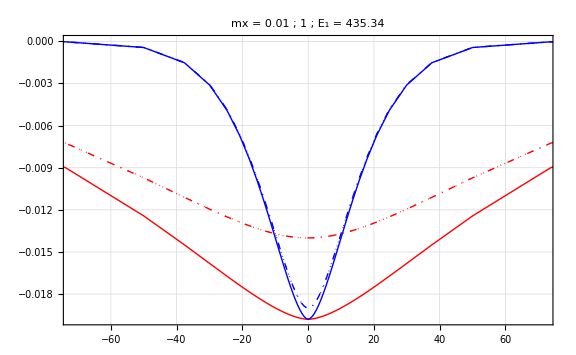
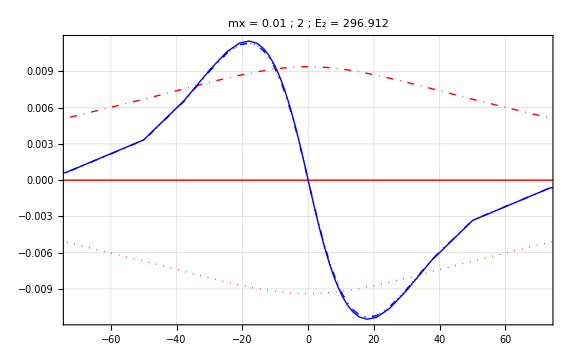
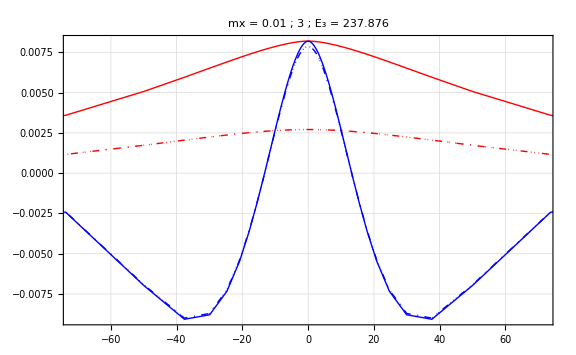
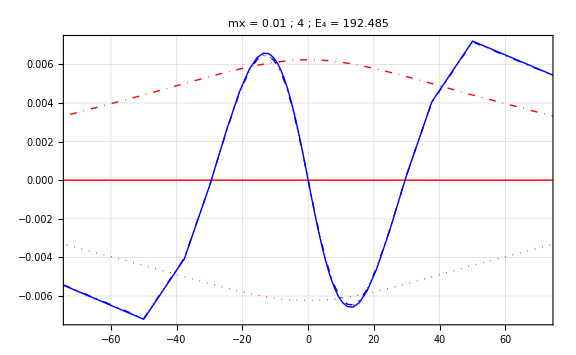
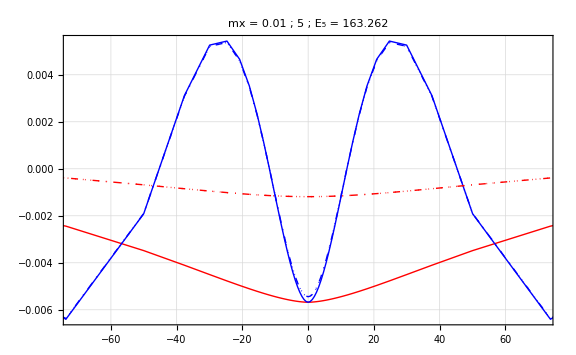
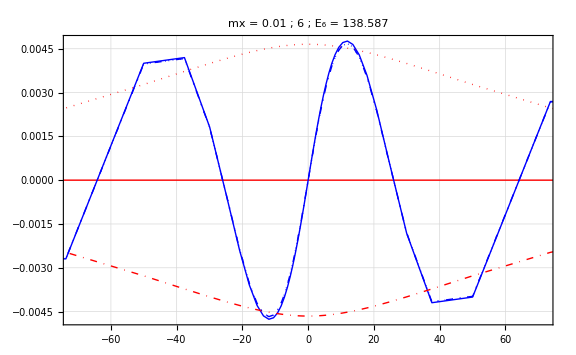
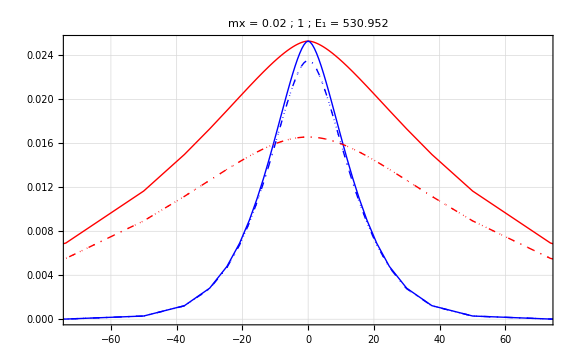
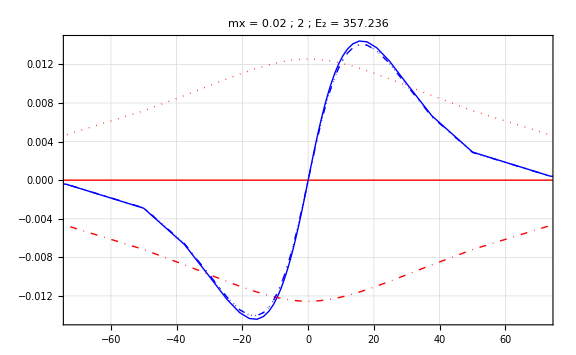
{331.198,-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-}

1.63739 GB

1.68376 GB

```mathematica
(*gridWheaders[*)
LightPink~bg~bgb@MemoryInUse[]
AbsoluteTiming@TableForm@Table[
Module[
{
oneef=allmx[[mxi,ii]],oneev=allmxevs[[mxi,ii]],mxval=allmxmx[[mxi]],
tb=(pio2-0.01),
ds
},
ds=2*tb/50;
ListLinePlot[
Evaluate[Flatten[ParallelTable[
{
{10*Tan[s],oneef[10*Tan[s],0]},
{10*Tan[s],oneef[0,10*Tan[s]]},
{10*Tan[s],oneef[10*Tan[s],10]},
{10*Tan[s],oneef[10,10*Tan[s]]},
{10*Tan[s],oneef[10*Tan[s],-10]},
{10*Tan[s],oneef[-10,10*Tan[s]]}
},
{s,-tb,tb,ds}
],{{2},{1},{3}}]],
ImageSize->Large,
PlotTheme->"Detailed",
PlotLabel->Style[tssf["mx = `1` ; `2` ; E_(`2`) = `3`",mxval,ii,oneev//QuantityMagnitude],24,Black],
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dotted},{Thick,Blue,Dotted},{Thick,Red,DotDashed},{Thick,Blue,DotDashed}}
]
],
{mxi,37},
{ii,6}
]
LightCyan~bg~bgb@MemoryInUse[]
LightRed~bg~bgb@MaxMemoryUsed[]
```

#### First run of this code on a fresh kernel

1.61 GB RAM after importing all the EFs

1.638 GB RAM after making all plots (does not account for RAM in parallel kernels)

Time to make all plots: 326 sec.

```mathematica
LightOrange~bg~bgb@MemoryInUse[]
AbsoluteTiming@TableForm@Table[
Module[
{
oneef=allmx[[mxi,ii]],oneev=allmxevs[[mxi,ii]],mxval=allmxmx[[mxi]],
tb=(pio2-0.01),
ds
},
ds=2*tb/50;
ListLinePlot[
Evaluate[Flatten[ParallelTable[
{
{10*Tan[s],oneef[10*Tan[s],0]},
{10*Tan[s],oneef[0,10*Tan[s]]},
{10*Tan[s],oneef[10*Tan[s],10]},
{10*Tan[s],oneef[10,10*Tan[s]]},
{10*Tan[s],oneef[10*Tan[s],-10]},
{10*Tan[s],oneef[-10,10*Tan[s]]}
},
{s,-tb,tb,ds}
],{{2},{1},{3}}]],
ImageSize->Large,
PlotTheme->"Detailed",
PlotLabel->Style[tssf["mx = `1` ; `2` ; E_(`2`) = `3`",mxval,ii,oneev//QuantityMagnitude],24,Black],
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dotted},{Thick,Blue,Dotted},{Thick,Red,DotDashed},{Thick,Blue,DotDashed}}
]
],
{mxi,37},
{ii,6}
]
LightMagenta~bg~bgb@MemoryInUse[]
LightRed~bg~bgb@MaxMemoryUsed[]
```

1.61338 GB

Run 08/08 @ 4:40

{326.384,1.81125
-Graphics- | 1.403
-Graphics- | 1.43437
-Graphics- | 1.42373
-Graphics- | 1.47138
-Graphics- | 1.42255
-Graphics-
1.4982
-Graphics- | 1.42631
-Graphics- | 1.43561
-Graphics- | 1.38493
-Graphics- | 1.4302
-Graphics- | 1.43414
-Graphics-
1.44901
-Graphics- | 1.40949
-Graphics- | 1.39828
-Graphics- | 1.41651
-Graphics- | 1.3902
-Graphics- | 1.35264
-Graphics-
1.38673
-Graphics- | 1.39191
-Graphics- | 1.4001
-Graphics- | 1.42632
-Graphics- | 1.38672
-Graphics- | 1.36216
-Graphics-
1.38764
-Graphics- | 1.39397
-Graphics- | 1.41366
-Graphics- | 1.47404
-Graphics- | 1.39942
-Graphics- | 1.42218
-Graphics-
1.46795
-Graphics- | 1.44395
-Graphics- | 1.43725
-Graphics- | 1.46027
-Graphics- | 1.47511
-Graphics- | 1.59419
-Graphics-
1.53484
-Graphics- | 1.5765
-Graphics- | 1.46218
-Graphics- | 1.43079
-Graphics- | 1.43866
-Graphics- | 1.43085
-Graphics-
1.4431
-Graphics- | 1.44281
-Graphics- | 1.44751
-Graphics- | 1.4972
-Graphics- | 1.4834
-Graphics- | 1.41925
-Graphics-
1.45863
-Graphics- | 1.39414
-Graphics- | 1.48777
-Graphics- | 1.49904
-Graphics- | 1.42597
-Graphics- | 1.39572
-Graphics-
1.48795
-Graphics- | 1.4178
-Graphics- | 1.46402
-Graphics- | 1.47276
-Graphics- | 1.44416
-Graphics- | 1.438
-Graphics-
1.44916
-Graphics- | 1.44567
-Graphics- | 1.43492
-Graphics- | 1.43139
-Graphics- | 1.43293
-Graphics- | 1.43699
-Graphics-
1.46873
-Graphics- | 1.44998
-Graphics- | 1.43845
-Graphics- | 1.52433
-Graphics- | 1.43601
-Graphics- | 1.48368
-Graphics-
1.48396
-Graphics- | 1.50463
-Graphics- | 1.44579
-Graphics- | 1.42468
-Graphics- | 1.44502
-Graphics- | 1.45256
-Graphics-
1.37612
-Graphics- | 1.56435
-Graphics- | 1.54247
-Graphics- | 1.48356
-Graphics- | 1.48332
-Graphics- | 1.45066
-Graphics-
1.40131
-Graphics- | 1.58111
-Graphics- | 1.51178
-Graphics- | 1.42285
-Graphics- | 1.48045
-Graphics- | 1.50282
-Graphics-
1.4129
-Graphics- | 1.44416
-Graphics- | 1.46811
-Graphics- | 1.47378
-Graphics- | 1.42763
-Graphics- | 1.6271
-Graphics-
1.51491
-Graphics- | 1.53644
-Graphics- | 1.59869
-Graphics- | 1.51538
-Graphics- | 1.50329
-Graphics- | 1.48102
-Graphics-
1.45443
-Graphics- | 1.57709
-Graphics- | 1.49318
-Graphics- | 1.43894
-Graphics- | 1.4774
-Graphics- | 1.46876
-Graphics-
1.44957
-Graphics- | 1.38989
-Graphics- | 1.48211
-Graphics- | 1.53336
-Graphics- | 1.46705
-Graphics- | 1.52325
-Graphics-
1.50226
-Graphics- | 1.49328
-Graphics- | 1.49263
-Graphics- | 1.52026
-Graphics- | 1.48727
-Graphics- | 1.50446
-Graphics-
1.44194
-Graphics- | 1.45282
-Graphics- | 1.46478
-Graphics- | 1.46046
-Graphics- | 1.53245
-Graphics- | 1.56112
-Graphics-
1.51549
-Graphics- | 1.48467
-Graphics- | 1.45363
-Graphics- | 1.50598
-Graphics- | 1.48364
-Graphics- | 1.48561
-Graphics-
1.38988
-Graphics- | 1.43362
-Graphics- | 1.47309
-Graphics- | 1.49235
-Graphics- | 1.43963
-Graphics- | 1.46785
-Graphics-
1.53723
-Graphics- | 1.515
-Graphics- | 1.45625
-Graphics- | 1.45488
-Graphics- | 1.51558
-Graphics- | 1.47261
-Graphics-
1.40041
-Graphics- | 1.48058
-Graphics- | 1.55932
-Graphics- | 1.43839
-Graphics- | 1.49714
-Graphics- | 1.48164
-Graphics-
1.45503
-Graphics- | 1.45267
-Graphics- | 1.49169
-Graphics- | 1.45582
-Graphics- | 1.39112
-Graphics- | 1.4332
-Graphics-
1.47666
-Graphics- | 1.45651
-Graphics- | 1.45318
-Graphics- | 1.45028
-Graphics- | 1.4758
-Graphics- | 1.4293
-Graphics-
1.47231
-Graphics- | 1.44881
-Graphics- | 1.46211
-Graphics- | 1.49029
-Graphics- | 1.47699
-Graphics- | 1.45692
-Graphics-
1.46725
-Graphics- | 1.42878
-Graphics- | 1.46057
-Graphics- | 1.48582
-Graphics- | 1.46389
-Graphics- | 1.41263
-Graphics-
1.47615
-Graphics- | 1.47853
-Graphics- | 1.50363
-Graphics- | 1.40747
-Graphics- | 1.44778
-Graphics- | 1.45656
-Graphics-
1.58442
-Graphics- | 1.45268
-Graphics- | 1.51588
-Graphics- | 1.48484
-Graphics- | 1.51124
-Graphics- | 1.47159
-Graphics-
1.47134
-Graphics- | 1.49523
-Graphics- | 1.41101
-Graphics- | 1.47223
-Graphics- | 1.47929
-Graphics- | 1.49202
-Graphics-
1.49571
-Graphics- | 1.48623
-Graphics- | 1.48557
-Graphics- | 1.47382
-Graphics- | 1.50528
-Graphics- | 1.40861
-Graphics-
1.46551
-Graphics- | 1.43761
-Graphics- | 1.44231
-Graphics- | 1.42684
-Graphics- | 1.48114
-Graphics- | 1.45746
-Graphics-
1.47851
-Graphics- | 1.42064
-Graphics- | 1.43973
-Graphics- | 1.48717
-Graphics- | 1.43396
-Graphics- | 1.50276
-Graphics-
1.40607
-Graphics- | 1.48507
-Graphics- | 1.48514
-Graphics- | 1.50512
-Graphics- | 1.43765
-Graphics- | 1.43851
-Graphics-
1.48367
-Graphics- | 1.46191
-Graphics- | 1.5883
-Graphics- | 1.47928
-Graphics- | 1.45172
-Graphics- | 1.45548
-Graphics-}

1.633 GB

1.68376 GB

### Early experimenting

```mathematica
testef=Normal@fl2d[
1,
1,
"nefs"/*Import
];
```

```mathematica
ArrayReshape[
Map[
Plot[
{#[x,0],#[0,x]},
{x,0,300},
ImageSize->{500,500},AspectRatio->Full,
PlotRange->Full,
PlotStyle->{{Thick,Red},{Thick,Blue}}
]&,
testef
],
{3,4}
]//TableForm//AbsoluteTiming
```

{148.321,-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-}

Laptop timing : 255 sec vs 148 sec on desktop

{255.321,-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-}

```mathematica
GraphicsGrid[
ArrayReshape[
Map[
Plot[
{
#[x,0],#[0,x],
#[x,10],#[10,x],
#[x,-10],#[-10,x]
},
{x,0,300},
(*ImageSize->{500,500},AspectRatio->Full,*)
PlotRange->Full,
PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dotted},{Thick,Blue,Dotted},{Thick,Red,DotDashed},{Thick,Blue,DotDashed}}
]&,
testef
],
{3,4}
],
ImageSize->{1800,1200}]//AbsoluteTiming
```

{482.222,-Graphics-}

Laptop timing: 817 sec vs 482 sec on desktop

{817.81,-Graphics-}

```mathematica
Table[
{
s,
t,
s+t
},
{s,-3Pi/8,3Pi/8,Pi/50},{t,-3Pi/8,3Pi/8,Pi/50}
]
```

{76,76,3}

```mathematica
{4,3,1}+{5,2,5}
```

{9,5,6}

```mathematica
cols={LightBlue,LightRed,LightGreen};
res={2+2,5+9,8-2};
```

```mathematica
bg@@#&/@Transpose[{cols,res}]
```

{4,14,6}

```mathematica
{LightBlue,LightRed,LightGreen}~bg~{2+2,5+9,8-2}
```

bg[{RGBColor[0.87, 0.94, 1],RGBColor[1, 0.85, 0.85],RGBColor[0.88, 1, 0.88]},{4,14,6}]

```mathematica
oneef=testef[[1]];
```

```mathematica
GraphicsGrid[
Table[
Column@AbsoluteTiming@ListPointPlot3D[
Flatten[ParallelTable[
{
st[[1]],
st[[2]],
testef[[i]][c*Tan[st[[1]]],c*Tan[st[[2]]]]
},
{st,{{x,x0},{x0,x}}},
{x0,{0,10,-10}},
{x,-(pio2-0.1),(pio2-0.1),2(pio2-0.1)/100}
],1],
ImageSize->{600,600}(*,
PlotStyle->Table[{PointSize[Medium],col},{col,randash[[;;9,1]]}]*)
],
{i,4},
{c,{1,5,10}}
],
ImageSize->{2400,1800},
ItemAspectRatio->Full
]
```

-Graphics-

```mathematica
bg@@#&/@Transpose[
{
cols,
Table[
GraphicsGrid[
ArrayReshape[Table[
Column@AbsoluteTiming@ListPointPlot3D[
Flatten[ParallelTable[
{
c*Tan[st[[1]]],
c*Tan[st[[2]]],
testef[[i]][c*Tan[st[[1]]],c*Tan[st[[2]]]]
},
{st,{{x,x0},{x0,x}}},
{x0,{0,10,-10}},
{x,-(pio2-0.1),(pio2-0.1),2(pio2-0.1)/100}
],1],
ImageSize->{700,700},
PlotStyle->PointSize[Medium]
],
{i,4}
],
{2,2}
],
ImageSize->{1600,1600}
],
{c,{1,5,10}}
]
}]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{
LightMagenta~bg~Column@AbsoluteTiming@ListPointPlot3D[
Flatten[ParallelTable[
{
10*Tan[s],
10*Tan[t],
testef[[1]][10*Tan[s],10*Tan[t]]
},
{s,-(pio2-0.1),(pio2-0.1),2(pio2-0.1)/50},{t,-(pio2-0.1),(pio2-0.1),2(pio2-0.1)/50}
],1],
ImageSize->{700,700},
PlotStyle->PointSize[Medium]
],
LightOrange~bg~Column@AbsoluteTiming@ListPointPlot3D[
Flatten[ParallelTable[
{
5*Tan[s],
5*Tan[t],
testef[[1]][5*Tan[s],5*Tan[t]]
},
{s,-(pio2-0.1),(pio2-0.1),2(pio2-0.1)/50},{t,-(pio2-0.1),(pio2-0.1),2(pio2-0.1)/50}
],1],
ImageSize->{700,700},
PlotStyle->PointSize[Medium]
],
LightCyan~bg~Column@AbsoluteTiming@ListPointPlot3D[
Flatten[ParallelTable[
{
Tan[s],
Tan[t],
oneef[Tan[s],Tan[t]]
},
{s,-(pio2-0.1),(pio2-0.1),2(pio2-0.1)/100},{t,-(pio2-0.1),(pio2-0.1),2(pio2-0.1)/100}
],1],
ImageSize->{700,700},
PlotStyle->PointSize[Medium]
]
}
```

{10.9532
-Graphics3D-,11.1022
-Graphics3D-,38.5747
-Graphics3D-}

Still about a 2 second difference

{24.1239,-Graphics3D-}

{22.9079,-Graphics3D-}

#### Parallel table is definitely fast.

```mathematica
{
LightOrange~bg~AbsoluteTiming@ListPointPlot3D[
Flatten[Table[
{
Tan[s],
Tan[t],
testef[[1]][Tan[s],Tan[t]]
},
{s,-3Pi/8,3Pi/8,Pi/100},{t,-3Pi/8,3Pi/8,Pi/100}
],1],
ImageSize->{900,900}
],
oneef=testef[[1]];,
LightGreen~bg~AbsoluteTiming@ListPointPlot3D[
Flatten[Table[
{
Tan[s],
Tan[t],
oneef[Tan[s],Tan[t]]
},
{s,-3Pi/8,3Pi/8,Pi/100},{t,-3Pi/8,3Pi/8,Pi/100}
],1],
ImageSize->{900,900}
],
LightBlue~bg~AbsoluteTiming@ListPointPlot3D[
Flatten[ParallelTable[
{
Tan[s],
Tan[t],
oneef[Tan[s],Tan[t]]
},
{s,-3Pi/8,3Pi/8,Pi/100},{t,-3Pi/8,3Pi/8,Pi/100}
],1],
ImageSize->{900,900}
]
}
```

Pre-saving the list element separately maybe helps a bit?

{{78.3394,-Graphics3D-},Null,{76.0094,-Graphics3D-},{24.2275,-Graphics3D-}}

Old

{519.258,-Graphics3D-}

## 3D Plots of {E_tr,f_0,μ^x}

### Set of 6 ListPointPlot3D[]’s in Dissertation (as of 08/05)

```mathematica
etrfoxymx3d=fl2d[
Values
/*
(Flatten[#,{{3},{1},{2,4},{5}}]&)
/*
(Module[
{xdata=#[[1]],ydata=#[[2]]},
Column[
{
PointLegend[
{Blue,Magenta,Green,Red,Cyan,Orange,Purple},
Table[StringForm["μ^y=`1`",TraditionalForm@my],{my,{0.7,0.75,0.8,0.85,0.9,0.95,1.}}],
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
PointLegend[
{Lighter@Gray,Darker@Gray,Gray},
{"μ^x ≠ μ^y ; f_0^x","μ^x ≠ μ^y ; f_0^y","μ^x = μ^y ; f_0^(x + y)"},
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
TableForm[
Transpose@ArrayReshape[
Map[
ListPointPlot3D[
Flatten[
Table[
{
xdata[[i,;;-2]],
ydata[[i,;;-2]],
{{
xdata[[i,-1,1]],
xdata[[i,-1,2]]+ydata[[i,-1,2]],
xdata[[i,-1,3]]
}}
},
{i,Length[xdata]}
],
1],
FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},
ImageSize->0.5*{900,900},AspectRatio->Full,
Filling->Axis,FillingStyle->Thick,
Boxed->False,
LabelStyle->labsty,
PlotStyle->Flatten[
Table[
{AbsolutePointSize[i[[2]]],lida[col,i[[1]]]},
{col,{Blue,Magenta,Green,Red,Cyan,Orange,Purple}},
{i,{{0.3,6},{0.7,6},{0.5,10}}}
],
1],
AxesStyle->{Red,Blue,Purple},
AxesLabel->#axla,
AxesEdge->{{-1,-1},{-1,-1},{-1,1}},
Ticks->#axti,
ViewPoint->#vp,
Epilog->{
Inset[
Framed[
Style[#subfig,labsty/.{24->16}],
Background->White,RoundingRadius->5
],
Scaled@{0.99,0.99},Scaled@{0.99,0.99}
]
}
]&,
{
<|"vp"->{-2,0,2},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(f)"|>,
<|"vp"->{-Infinity,-Infinity,Infinity},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(a)"|>,
<|"vp"->{0,-2,2},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(d)"|>,
<|"vp"->{-Infinity,0,0},"axla"->{None," f_0^j "," μ^x "},"axti"->{None,Automatic,Automatic},"subfig"->"(e)"|>,
<|"vp"->{0,0,Infinity},"axla"->{" E_tr^j "," f_0^j ",None},"axti"->{Automatic,Automatic,None},"subfig"->"(b)"|>,
<|"vp"->{0,-Infinity,0},"axla"->{" E_tr^j ",None," μ^x "},"axti"->{Automatic,None,Automatic},"subfig"->"(c)"|>
},
{1}
],
{3,2}]]
},
Center]
]&),
Values,
{
"mx",
"etr"/*(2;;)/*Values,
"fox"/*1/*Values,
"foy"/*1/*Values
}
/*
(Module[
{mx=#[[1]],etr=#[[2]],fox=#[[3]],foy=#[[4]]},
{
Transpose[{etr,fox,Table[mx,{11}]}],
Transpose[{etr,foy,Table[mx,{11}]}]
}
]&)
/*Map[AssociationThread[Table[tssf["j`1`",i],{i,2,12}],#]&]
/*Map[Select[#,Abs[#[[2]]]>10^-4&,1]&]/*Values
]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
etrfoxymx3d[[1,;;-2]]
etrfoxymx3d[[1,-1,1,;;,;;]]
```

{,}

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

```mathematica
{
Export[dfd<>"d_comb-3d-grid_etr-foxy-mx_new-leg.pdf",#],
Export[dfd<>"d_leg-3d-grid_etr-foxy-mx_new-leg.pdf",Column[#[[1,;;-2]],Center]],
Export[dfd<>"d_plt-3d-grid_etr-foxy-mx_new-leg.pdf",#[[1,-1]]]
}&[etrfoxymx3d]
```

{../../../dis/figs/d_comb-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_leg-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_plt-3d-grid_etr-foxy-mx_new-leg.pdf}

Save each figure individually

```mathematica
{
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-f0-side.pdf",#[[1,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_f0-above.pdf",#[[1,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_f0-vs-etr-side.pdf",#[[2,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-iso-perspect.pdf",#[[2,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-etr-side.pdf",#[[3,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_etr-above.pdf",#[[3,1]]]
}&@etrfoxymx3d[[1,-1,1]]
```

{../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-f0-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-above.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-iso-perspect.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_etr-above.pdf}

```mathematica
CreatePalette[Dynamic[etrfoxymx3d],WindowMargins->Automatic]
```

### Same, for (f̃)_0^j

```mathematica
etrbarfoxymx3d=fl2d[
Values
/*
(Flatten[#,{{3},{1},{2,4},{5}}]&)
/*
(Module[
{xdata=#[[1]],ydata=#[[2]]},
Column[
{
PointLegend[
{Blue,Magenta,Green,Red,Cyan,Orange,Purple},
Table[StringForm["μ^y=`1`",TraditionalForm@my],{my,{0.7,0.75,0.8,0.85,0.9,0.95,1.}}],
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
PointLegend[
{Lighter@Gray,Darker@Gray,Gray},
{"μ^x ≠ μ^y ; f_0^x","μ^x ≠ μ^y ; f_0^y","μ^x = μ^y ; f_0^(x + y)"},
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
TableForm[
ArrayReshape[
Map[
ListPointPlot3D[
Flatten[
Table[
{
xdata[[i,;;-2]],
ydata[[i,;;-2]],
{{
xdata[[i,-1,1]],
xdata[[i,-1,2]]+ydata[[i,-1,2]],
xdata[[i,-1,3]]
}}
},
{i,Length[xdata]}
],
1],
FaceGrids->#faces,
ImageSize->0.5*{900,900},AspectRatio->Full,
Filling->Axis,FillingStyle->Thick,
Boxed->False,BoxRatios->{1,1,1},
LabelStyle->labsty,
ScalingFunctions->{None,"Log",None},
PlotStyle->Flatten[
Table[
{AbsolutePointSize[i[[2]]],lida[col,i[[1]]]},
{col,{Blue,Magenta,Green,Red,Cyan,Orange,Purple}},
{i,{{0.3,6},{0.7,6},{0.5,10}}}
],
1],
AxesStyle->{Red,Blue,Purple},
AxesLabel->#axla,
AxesEdge->#axed,
Ticks->#axti,
ViewPoint->#vp,
Epilog->{
Inset[
Framed[
Style[#subfig,labsty/.{24->16}],
Background->White,RoundingRadius->5
],
Scaled@#epiloc,Scaled@#epiloc
]
}
]&,
{
<|"vp"->{-Infinity,Infinity,Infinity},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{1,-1},{-1,-1},{1,1}},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(a)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,-1,0},{1,0,0}}|>,
<|"vp"->{0,0,Infinity},"axla"->{" E_tr^j "," (f̃)_0^j ",None},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,Automatic,None},"subfig"->"(b)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{0,-Infinity,0},"axla"->{" E_tr^j ",None," μ^x "},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,None,Automatic},"subfig"->"(c)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{0,2,2},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{1,-1},{-1,-1},{-1,-1}},"axti"->{Automatic,Automatic,{0.5,1}},"subfig"->"(d)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,-1,0},{1,0,0}}|>,
<|"vp"->{-Infinity,0,0},"axla"->{None," (f̃)_0^j "," μ^x "},"axed"->{{-1,-1},{-1,-1},{1,1}},"axti"->{None,Automatic,Automatic},"subfig"->"(e)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{-2,0,2},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(f)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>
},
{1}
],
{2,3}]]
},
Center]
]&),
Values,
{
"mx",
"etr"/*(2;;)/*Values,
"fbx"/*1/*Values,
"fby"/*1/*Values
}
/*
(Module[
{mx=#[[1]],etr=#[[2]],fox=#[[3]],foy=#[[4]]},
{
Transpose[{etr,fox,Table[mx,{11}]}],
Transpose[{etr,foy,Table[mx,{11}]}]
}
]&)
/*Map[AssociationThread[Table[tssf["j`1`",i],{i,2,12}],#]&]
/*Map[Select[#,Abs[#[[2]]]>10^-4&,1]&]/*Values
]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
etrbarfoxymx3d[[1,;;-2]]
etrbarfoxymx3d[[1,-1,1,;;,;;]]
```

{,}

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

```mathematica
{
Export[dfd<>"d_comb-3d-grid_etr-foxy-bar-mx_new-leg.pdf",#],
Export[dfd<>"d_leg-3d-grid_etr-foxy-bar-mx_new-leg.pdf",Column[#[[1,;;-2]],Center]],
Export[dfd<>"d_plt-3d-grid_etr-foxy-bar-mx_new-leg.pdf",#[[1,-1]]]
}&[etrbarfoxymx3d]
```

{../../../dis/figs/d_comb-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_leg-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_plt-3d-grid_etr-foxy-mx_new-leg.pdf}

Save each figure individually

```mathematica
{
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_mx-vs-f0-side.pdf",#[[1,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_f0-above.pdf",#[[1,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_f0-vs-etr-side.pdf",#[[2,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-iso-perspect.pdf",#[[2,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_mx-vs-etr-side.pdf",#[[3,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_etr-above.pdf",#[[3,1]]]
}&@etrbarfoxymx3d[[1,-1,1]]
```

{../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-f0-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-above.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-iso-perspect.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_etr-above.pdf}

```mathematica
CreatePalette[Dynamic[etrbarfoxymx3d],WindowMargins->Automatic]
```

m2bf9_shm28FrontEndObject[LinkObject["m2bf9_shm", 3, 1]]28Untitled-2

## What else is worth showing...?

{μ^(x/y),μ^0,f_0^j/OverTilde[f_0]} ?

# 2DC v2.1 (Making of)

## Import all data besides EFs, then save a new Dataset from that, and Import that in the future

#### What would happen if I import All μ^x?

```mathematica
{bgb@MemoryInUse[],bmb@MemoryInUse[$FrontEnd],bgb@MaxMemoryUsed[]}
fl2d[1,1,All,All/*Map[Import]];
bmb@ByteCount[%]
{bgb@MemoryInUse[],bmb@MemoryInUse[$FrontEnd],bgb@MaxMemoryUsed[]}
```

Sure enough, 37 * (150 MB) = 5.5 GB

```mathematica
Quantity[150,"Megabytes"]*37
```

5550 MB

{0.210275 GB,0.818504 MB,0.210403 GB}

5515. MB

{5.64154 GB,0.818504 MB,5.67458 GB}

Sooo yeah that definitely took up a big chunk of memory, each set of 37 μ^x takes up 5.5 GB

I think the whole Dynamic updating thing is what kills me, somehow.
Maybe having Dynamic Palettes open causes problems when data keeps going back and forth

{1.98363 GB,0.496932 MB,2.01768 GB}

5515. MB

{8.33745 GB,1.07218 MB,10.0408 GB}

#### So, all of the data from every run, e.g. for a given {μ^x,μ^y,κ,χ_(2D)}, takes up about 150 MB

```mathematica
{bgb@MemoryInUse[],bmb@MemoryInUse[$FrontEnd],bgb@MaxMemoryUsed[]}
fl2d[1,1,1,All/*Map[Import]]
bmb@ByteCount[%]
{bgb@MemoryInUse[],bmb@MemoryInUse[$FrontEnd],bgb@MaxMemoryUsed[]}
```

{5.80211 GB,0.81858 MB,5.83556 GB}

Dataset[<>]

148.147 MB

{5.94835 GB,0.81858 MB,5.98253 GB}

Yep, the additional memory matches up with the ByteCount[] of the Imported Dataset.

{1.6909 GB,0.496804 MB,1.72495 GB}

Dataset[<>]

148.147 MB

{1.83714 GB,0.496812 MB,1.87131 GB}

Still, none of this memory usage goes to the front end.

{1.39816 GB,0.496804 MB,1.57394 GB}

Dataset[<>]

{1.54419 GB,0.496804 MB,1.57858 GB}

Loading everything from a single run costs about 150 MB

1.10537 GB

Dataset[<>]

1.25139 GB

```mathematica
fl2d[1,1,1,ik["ndeparams"]]
```

Dataset[<>]

```mathematica
{
Normal@fl2d[1,1,1,
ik["ndeparams"]/*{"mx","my","chi","kappa"}
],
Normal@fl2d[1,1,1,
AssociationThread[{"m0","mxy"},ikk/@{"m0","mxy"}]
]
}
```

{<|mx→0.01,my→0.7,chi→7.74788,kappa→1|>,<|m0→0.00797874,mxy→0.0142857|>}

```mathematica
fl2d[
1,
1,
1,
{
ik["ndeparams"]/*{"mx","my","chi","kappa"},
AssociationThread[{"m0","mxy"},ikk/@{"m0","mxy"}],
<|
"evs"->ikk["evs"],
"etr"->ikk["etr"],
"fox"->ikk["fox"],
"foy"->ikk["foy"]
|>
}
/*
(Join@@#&)
]
```

Dataset[<>]

## Will hopefully fix crash problem by avoiding repeated Imports.

## OK enough poking around, for now let’s “fix” the problem by loading everything I could possibly want from κ = 1, and saving it as a separate Dataset, then using that for the time being. Will also keep a top-level key for the nEF file name in case I do need to load those.

## Exporting the re-made dataset

#### Save the DS to a variable before exporting

```mathematica
allkap1=fl2d[
1,All,All,
{
ik["ndeparams"]/*{"mx","my","chi","kappa"},
AssociationThread[{"m0","mxy"},ikk/@{"m0","mxy"}],
<|
"evs"->ikk["evs"],
"etr"->ikk["etr"],
"nefs"->"ndenefs",
"fox"->ikk["fox"]
/*
(;;11)
/*
(<|KeyValueMap[#1->KeyDrop[#2,StringReplace[#1,"i"->"j"]]&,#]|>&)
/*
(Select[#,UnsameQ[#,<||>]&]&),
"foy"->ikk["foy"]
/*
(;;11)
/*
(<|KeyValueMap[#1->KeyDrop[#2,StringReplace[#1,"i"->"j"]]&,#]|>&)
/*
(Select[#,UnsameQ[#,<||>]&]&)
|>
}
/*
(Join@@#&)
/*
(Join[
#,
<|
"fbx"->#["fox"]/#["mx"],
"fby"->#["foy"]/#["my"],
"alc"->Function[{nx,gamma},Evaluate[UnitConvert[
(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[#["kappa"]]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]],
"afc"->Function[{nx,gamma},Evaluate[
(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[#["kappa"]]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]
]]
|>
]&)
/*
(Module[{fbxassoc=#["fox"],fbyassoc=#["foy"],kappa=#["kappa"]},
Join[
#,
<|
"alx"->Map[
Function[{nx,gamma},
Evaluate[UnitConvert[
#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]
]&,
fbxassoc,
{2}
],
"aly"->Map[
Function[{nx,gamma},
Evaluate[UnitConvert[
#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]
]&,
fbyassoc,
{2}
],
"afx"->Map[
Function[{nx,gamma},
Evaluate[
1- Exp[-#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]]
]
]&,
fbxassoc,
{2}
],
"afy"->Map[
Function[{nx,gamma},
Evaluate[
1- Exp[-#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]]
]
]&,
fbyassoc,
{2}
]
|>
]
]&)
];
```

#### Double check that all is well before exporting

```mathematica
bmb@ByteCount[allkap1]
```

69.4857 MB

#### Yeah sure OK lets go

```mathematica
AbsoluteTiming@Export[c2d2<>"all-kap-1-ds.m",allkap1]
```

{2.21908,cl-2dc-v2/all-kap-1-ds.m}

## Building the re-made dataset

### Figured it out

#### All in one (looks good)

```mathematica
fl2d[
1,1,1,
{
ik["ndeparams"]/*{"mx","my","chi","kappa"},
AssociationThread[{"m0","mxy"},ikk/@{"m0","mxy"}],
<|
"evs"->ikk["evs"],
"etr"->ikk["etr"],
"nefs"->"ndenefs",
"fox"->ikk["fox"]
/*
(;;11)
/*
(<|KeyValueMap[#1->KeyDrop[#2,StringReplace[#1,"i"->"j"]]&,#]|>&)
/*
(Select[#,UnsameQ[#,<||>]&]&),
"foy"->ikk["foy"]
/*
(;;11)
/*
(<|KeyValueMap[#1->KeyDrop[#2,StringReplace[#1,"i"->"j"]]&,#]|>&)
/*
(Select[#,UnsameQ[#,<||>]&]&)
|>
}
/*
(Join@@#&)
/*
(Join[
#,
<|
"fbx"->#["fox"]/#["mx"],
"fby"->#["foy"]/#["my"],
"alc"->Function[{nx,gamma},Evaluate[UnitConvert[
(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[#["kappa"]]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]],
"afc"->Function[{nx,gamma},Evaluate[
(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[#["kappa"]]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]
]]
|>
]&)
/*
(Module[{fbxassoc=#["fox"],fbyassoc=#["foy"],kappa=#["kappa"]},
Join[
#,
<|
"alx"->Map[
Function[{nx,gamma},
Evaluate[UnitConvert[
#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]
]&,
fbxassoc,
{2}
],
"aly"->Map[
Function[{nx,gamma},
Evaluate[UnitConvert[
#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]
]&,
fbyassoc,
{2}
],
"afx"->Map[
Function[{nx,gamma},
Evaluate[
1- Exp[-#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]]
]
]&,
fbxassoc,
{2}
],
"afy"->Map[
Function[{nx,gamma},
Evaluate[
1- Exp[-#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]]
]
]&,
fbyassoc,
{2}
]
|>
]
]&)
]
```

Dataset[<>]

#### This function does what I need w.r.t α and A:

```mathematica
fl2d[
1,1,1,
<|
"mx"->ik["ndeparams"]/*"mx",
"my"->ik["ndeparams"]/*"my",
"kappa"->ik["ndeparams"]/*"kappa",
"fox"->ikk["fox"]
/*
(;;11)
/*
(<|KeyValueMap[#1->KeyDrop[#2,StringReplace[#1,"i"->"j"]]&,#]|>&)
/*
(Select[#,UnsameQ[#,<||>]&]&),
"foy"->ikk["foy"]
/*
(;;11)
/*
(<|KeyValueMap[#1->KeyDrop[#2,StringReplace[#1,"i"->"j"]]&,#]|>&)
/*
(Select[#,UnsameQ[#,<||>]&]&)
|>
/*
(Join[
#,
<|
"fbx"->#fox/#mx,
"fby"->#foy/#my,
"alc"->Function[{nx,gamma},Evaluate[UnitConvert[
(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[#kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]],
"afc"->Function[{nx,gamma},Evaluate[
(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[#kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]
]]
|>
]&)
/*
(Module[{fbxassoc=#fbx,fbyassoc=#fby,kappa=#kappa},
Join[
#,
<|
"alx"->Map[
Function[{nx,gamma},
Evaluate[UnitConvert[
#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]
]&,
fbxassoc,
{2}
],
"aly"->Map[
Function[{nx,gamma},
Evaluate[UnitConvert[
#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]
]&,
fbyassoc,
{2}
],
"afx"->Map[
Function[{nx,gamma},
Evaluate[
1- Exp[-#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]]
]
]&,
fbxassoc,
{2}
],
"afy"->Map[
Function[{nx,gamma},
Evaluate[
1- Exp[-#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]]
]
]&,
fbyassoc,
{2}
]
|>
]
]&)
]
```

#### This function includes all other params that I want

```mathematica
fl2d[
1,
1,
1,
{
ik["ndeparams"]/*{"mx","my","chi","kappa"},
AssociationThread[{"m0","mxy"},ikk/@{"m0","mxy"}],
<|
"evs"->ikk["evs"],
"etr"->ikk["etr"],
"fox"->ikk["fox"]/*(;;11)/*(<|KeyValueMap[
#1->KeyDrop[#2,{StringReplace[#1,"i"->"j"],"j12"}]&,
#
]|>&)
/*
(
Select[#,UnsameQ[#,<||>]&]
&),
"foy"->ikk["foy"],
"nefs"->"ndenefs"
|>
}
/*
(Join@@#&)
/*Dataset
]
```

Dataset[<>]

### Figuring it out

#### This is almost ready to go, but need to deal with α/𝒜 x/y

```mathematica
fl2d[
1,
1,
1,
{
ik["ndeparams"]/*{"mx","my","chi","kappa"},
AssociationThread[{"m0","mxy"},ikk/@{"m0","mxy"}],
<|
"evs"->ikk["evs"],
"etr"->ikk["etr"],
"fox"->ikk["fox"]/*(;;11)/*(<|KeyValueMap[
#1->KeyDrop[#2,{StringReplace[#1,"i"->"j"],"j12"}]&,
#
]|>&)
/*
(
Select[#,UnsameQ[#,<||>]&]
&),
"foy"->ikk["foy"],
"alx"->ik["alphax"]/*(;;10)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,11}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],11}],
#[[;;-2]]
]&,
#
]
]&),
"aly"->ik["alphay"]/*(;;10)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,11}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],12}],
#
]&,
#
]
]&),
"afx"->ik["afax"]/*(;;10)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,11}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],12}],
#
]&,
#
]
]&),
"afy"->ik["afay"]/*(;;10)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,11}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],12}],
#
]&,
#
]
]&),
"nefs"->"ndenefs"
|>
}
/*
(Join@@#&)
/*Dataset
]
bmb@ByteCount[%]
```

Failure[…]

0.03732 MB

```mathematica
{LightBlue~bg~fl2d[1,1,1,ikk["fox"]/*(;;11)/*(<|KeyValueMap[#1->KeyDrop[#2,{StringReplace[#1,"i"->"j"],"j12"}]&,#]|>&)/*(Select[#,UnsameQ[#,<||>]&]&)],
LightOrange~bg~fl2d[1,1,1,ik["alphax"]/*(;;10)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,10}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],11}],
#[[;;-2]]
]&,
#
]
]&)
]
}
```

{Dataset[<>],Dataset[<>]}

#### Fuck this alpha bullshit. Just remake the fucking functions.

```mathematica
fl2d[
1,1,1,
<|
"mx"->ik["ndeparams"]/*"mx",
"my"->ik["ndeparams"]/*"my",
"kappa"->ik["ndeparams"]/*"kappa",
"fox"->ikk["fox"]
/*
(;;11)
/*
(<|KeyValueMap[#1->KeyDrop[#2,StringReplace[#1,"i"->"j"]]&,#]|>&)
/*
(Select[#,UnsameQ[#,<||>]&]&),
"foy"->ikk["foy"]
/*
(;;11)
/*
(<|KeyValueMap[#1->KeyDrop[#2,StringReplace[#1,"i"->"j"]]&,#]|>&)
/*
(Select[#,UnsameQ[#,<||>]&]&)
|>
/*
(Join[
#,
<|
"fbx"->#fox/#mx,
"fby"->#foy/#my,
"alc"->Function[{nx,gamma},Evaluate[UnitConvert[
(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[#kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]],
"afc"->Function[{nx,gamma},Evaluate[
(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[#kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]
]]
|>
]&)
/*
(Module[{fbxassoc=#fbx,fbyassoc=#fby,kappa=#kappa},
Join[
#,
<|
"alx"->Map[
Function[{nx,gamma},
Evaluate[UnitConvert[
#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]
]&,
fbxassoc,
{2}
],
"aly"->Map[
Function[{nx,gamma},
Evaluate[UnitConvert[
#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]*Quantity[4.1,"Angstroms"]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)],
"Meters"^(-1)]]
]&,
fbyassoc,
{2}
],
"afx"->Map[
Function[{nx,gamma},
Evaluate[
1- Exp[-#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]]
]
]&,
fbxassoc,
{2}
],
"afy"->Map[
Function[{nx,gamma},
Evaluate[
1- Exp[-#*(Pi*(cee^2)/(ccc*cm0*ce0*Sqrt[kappa]))*Quantity[nx,"Meters"^(-2)]/Quantity[gamma,"Seconds"^(-1)]]
]
]&,
fbyassoc,
{2}
]
|>
]
]&)
]
```

Dataset[<>]

#### Last test - compare ByteCount with and without loading nEFs. Wow: 0.246 MB vs. 74 MB. Obviously not going to import the nEFs, then.

```mathematica
Dataset@fl2d[
1,
1,
1,
{
ik["ndeparams"]/*{"mx","my","chi","kappa"},
AssociationThread[{"m0","mxy"},ikk/@{"m0","mxy"}],
<|
"evs"->ikk["evs"],
"etr"->ikk["etr"],
"fox"->ikk["fox"],
"foy"->ikk["foy"],
"alx"->ik["alphax"]/*(;;11)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,11}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],12}],
#
]&,
#
]
]&),
"aly"->ik["alphay"]/*(;;11)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,11}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],12}],
#
]&,
#
]
]&),
"afx"->ik["afax"]/*(;;11)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,11}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],12}],
#
]&,
#
]
]&),
"afy"->ik["afay"]/*(;;11)/*(
AssociationThread[
Table[tssf["i`1`",i],{i,11}],
Map[
AssociationThread[
Table[tssf["j`1`",j-1],{j,13-Length[#],12}],
#
]&,
#
]
]&),
"nefs"->ik["ndenefs"]
|>
}
/*
(Join@@#&)
/*Dataset
];
bmb@ByteCount[%]
```

74.2392 MB

# 2DC v2

## Get a little clever RE: picking points for μ^x/μ^y

```mathematica
Table[
{mx,my},
{my,0.7,1,0.1},
{mx,Flatten@{Table[i,{i,0.01,0.1,0.01}],Table[my-dma,{dma,0.4,0.1,-0.05}],Table[i,{i,my-0.09,my,0.01}]}}
];
%//framegrid
%%//Dimensions
```

{0.01,0.7} | {0.02,0.7} | {0.03,0.7} | {0.04,0.7} | {0.05,0.7} | {0.06,0.7} | {0.07,0.7} | {0.08,0.7} | {0.09,0.7} | {0.1,0.7} | {0.3,0.7} | {0.35,0.7} | {0.4,0.7} | {0.45,0.7} | {0.5,0.7} | {0.55,0.7} | {0.6,0.7} | {0.61,0.7} | {0.62,0.7} | {0.63,0.7} | {0.64,0.7} | {0.65,0.7} | {0.66,0.7} | {0.67,0.7} | {0.68,0.7} | {0.69,0.7} | {0.7,0.7}
{0.01,0.8} | {0.02,0.8} | {0.03,0.8} | {0.04,0.8} | {0.05,0.8} | {0.06,0.8} | {0.07,0.8} | {0.08,0.8} | {0.09,0.8} | {0.1,0.8} | {0.4,0.8} | {0.45,0.8} | {0.5,0.8} | {0.55,0.8} | {0.6,0.8} | {0.65,0.8} | {0.7,0.8} | {0.71,0.8} | {0.72,0.8} | {0.73,0.8} | {0.74,0.8} | {0.75,0.8} | {0.76,0.8} | {0.77,0.8} | {0.78,0.8} | {0.79,0.8} | {0.8,0.8}
{0.01,0.9} | {0.02,0.9} | {0.03,0.9} | {0.04,0.9} | {0.05,0.9} | {0.06,0.9} | {0.07,0.9} | {0.08,0.9} | {0.09,0.9} | {0.1,0.9} | {0.5,0.9} | {0.55,0.9} | {0.6,0.9} | {0.65,0.9} | {0.7,0.9} | {0.75,0.9} | {0.8,0.9} | {0.81,0.9} | {0.82,0.9} | {0.83,0.9} | {0.84,0.9} | {0.85,0.9} | {0.86,0.9} | {0.87,0.9} | {0.88,0.9} | {0.89,0.9} | {0.9,0.9}
{0.01,1.} | {0.02,1.} | {0.03,1.} | {0.04,1.} | {0.05,1.} | {0.06,1.} | {0.07,1.} | {0.08,1.} | {0.09,1.} | {0.1,1.} | {0.6,1.} | {0.65,1.} | {0.7,1.} | {0.75,1.} | {0.8,1.} | {0.85,1.} | {0.9,1.} | {0.91,1.} | {0.92,1.} | {0.93,1.} | {0.94,1.} | {0.95,1.} | {0.96,1.} | {0.97,1.} | {0.98,1.} | {0.99,1.} | {1.,1.}

{4,27,2}

## Import some data and see what’s good

#### String Manipulation

```mathematica
testfname=c2d2flist[[1,1,1]]
```

cl-2dc-v2/ndeparams_mx-0.01_my-0.7_chi-7.74788_kappa-1.m

```mathematica
StringCases[testfname,"mx-0."~~x:DigitCharacter..->x]
```

```mathematica
Map[
StringCases[#,"mx-"~~x:("0."~~DigitCharacter..)->x]&,
c2d2flist[[;;,;;,1]],
{2}
]
```

{{{0.01},{0.02},{0.03},{0.04},{0.05},{0.06},{0.07},{0.08},{0.09},{0.11},{0.12},{0.13},{0.14},{0.15},{0.16},{0.17},{0.18},{0.19},{0.1},{0.2},{0.35},{0.3},{0.45},{0.4},{0.55},{0.5},{0.61},{0.62},{0.63},{0.64},{0.65},{0.66},{0.67},{0.68},{0.69},{0.6},{0.7}},{{0.01},{0.02},{0.03},{0.04},{0.05},{0.06},{0.07},{0.08},{0.09},{0.11},{0.12},{0.13},{0.14},{0.15},{0.16},{0.17},{0.18},{0.19},{0.1},{0.2},{0.35},{0.45},{0.4},{0.55},{0.5},{0.65},{0.66},{0.67},{0.68},{0.69},{0.6},{0.71},{0.72},{0.73},{0.74},{0.75},{0.7}}}

### Would be really helpful to structure the data when importing (old import function, ruined by my ill-advised edits).

```mathematica
fl2d=Dataset[
Association@Table[
First@StringCases[myval,"my-"~~DigitCharacter..]->Module[
{
mxvals=Union[Map[StringCases[#,(*"mx-"~~x__~~"_"*)"mx-"~~RegularExpression["\\d.*_"]~~"_"(*"mx-"~~x:"mx-"~~(DigitCharacter~~"."~~DigitCharacter..):>x*)]&][FileNames["*"<>myval<>kaval,c2d2]]]
},
Print[LightOrange~bg~mxvals];
Print[LightRed~bg~myval];
Association@Table[
tssf["`1`",First@mx]->Association@Table[
qkeys->If[
Length[#]==1,
First@#,
Print["Error! one element has more than one filename (or no filenames)! : "<>qkeys<>"*_"<>mx<>myval<>kaval<>" :: "<>mx];Print[TableForm[#[[;;5]]]]
]&[
FileNames[qkeys<>"*_"<>mx<>myval<>kaval,c2d2
]
],
{qkeys,{"ndeparams","ndestats","ndeevs","ndeefs","normconsts","ndenefs","onc","fox","foy","alphax","alphay","afax","afay"}}
],
{mx,mxvals}
]],
{kaval,{"_kappa-1.m"}},
{myval,{(*"*_my-0.7_*","*_my-0.75_*","*_my-0.8_*","*_my-0.85_*","*_my-0.9_*",*)"*_my-0.95_*","*_my-1._*"}}
]];
```

```mathematica
fl2d
```

Dataset[<>]

Seems pretty straightforward to just import all data live... Calculated data will get imported basically instantly anyway

```mathematica
LightBlue~bg~fl2d[1,;;3,ik["ndeevs"]]
```

Dataset[<>]

### Some day I’ll actually understand Regexp and string manipulation... For now, I just rebuilt what I had done above from scratch. Because I’m dumb. But I learned stuff. So now I’m (in theory) less dumb.

```mathematica
Clear[fl2d]
```

```mathematica
fl2d=Dataset@Association@Table[
tssf["k`1`",First@StringCases[kaval,"-"~~x__~~".m":>x]]->Association@Table[
tssf["my`1`",First@StringCases[myval,"-"~~x__~~"_":>x]]->Module[
{
mxvals=Flatten@Union[
Map[StringCases[#,"mx-"~~x__~~"_my":>x]&][(StringSplit[FileNames["*_"<>myval<>kaval,c2d2],"/"][[;;,2]])]
]
},
Association@Table[
Module[
{
qvals=Flatten@Union[
Map[StringCases[#,q__~~"_mx-":>q]&][(StringSplit[FileNames["*_"<>"mx-"<>mxval<>"_"<>myval<>kaval,c2d2],"/"][[;;,2]])]
]
},
tssf["mx`1`",mxval]->Association@Table[
tssf["`1`",quant]->If[
Length[#]==1,
First@#,
Print[LightRed~bg~Style["Number of matching file names ≠ 1!!!",24,Bold,Black,FontFamily->"Arial"]]
]&[FileNames[quant<>"_mx-"<>mxval<>"_"<>myval<>kaval,c2d2]],
{quant,qvals}
]],
{mxval,mxvals}
]
],
{myval,{"my-0.7_","my-0.75_","my-0.8_","my-0.85_","my-0.9_","my-0.95_","my-1._"}}
],
{kaval,{"*_kappa-1.m"}}
];
```

```mathematica
fl2d
```

Dataset[<>]

```mathematica
fl2d[All,All,All,ik["ndeevs"]/*h2mev/*(;;6)]
```

Dataset[<>]

```mathematica
fl2d[All,All,All,ikk["ndeevs"]]
```

Dataset[<>]

## EVs

### Binding energies

```mathematica
LightCyan~bg~fl2d[
(ListPlot[#,PlotTheme->"Detailed",ImageSize->{900,450},AspectRatio->9/18,PlotLabel->"Binding energy vs. μ^x",LabelStyle->labsty]&),
Values,
{
ik["ndeparams"]/*"mx",
ik["ndeevs"]/*1/*Abs/*h2mev
}
]
```

-Graphics-

### Progression of all eigenenergies vs. μ^x - VERY COOL

```mathematica
LightBlue~bg~fl2d[
All,
Values/*(ListLinePlot[
Transpose[#],
PlotTheme->"Detailed",ImageSize->{1600,900},AspectRatio->Full,PlotLabel->"All eigenenergies vs. μ^x",LabelStyle->labsty,
PlotStyle->randash,
(*PlotMarkers->marksize[Flatten[{emmarks4,"△","▽"}],24],*)
PlotLegends->Placed[PointLegend[
Automatic,
Table[TraditionalForm@StringForm["`1`",ToString@i],{i,12}],
LegendLayout->{"Column",1}
],Right]
]&),
{
{ik["ndeparams"]/*"mx"},
ik["ndeevs"]/*Abs/*h2mev
}
/*
(Partition[Riffle[#[[2]],#[[1]],{1,-2,2}],2]&)
]
```

Dataset[<>]

#### Save one of these figures, put it in the dissertation and write things

```mathematica
fl2d[
1,
Values/*(ListLinePlot[
Transpose[#],
PlotTheme->"Detailed",ImageSize->0.5*{1600,900},AspectRatio->Full,(*PlotLabel->"All eigenenergies vs. μ^x; μ^y = 0.7 m_0",*)FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},LabelStyle->labsty,
PlotStyle->randash,
(*PlotMarkers->marksize[Flatten[{emmarks4,"△","▽"}],24],*)
PlotLegends->Placed[PointLegend[
Automatic,
Table[TraditionalForm@StringForm["E_(`1`)",ToString@i],{i,12}],
LegendLayout->(TableForm[
Map[
Row,
Transpose@ArrayReshape[#,{6,2,2}],
{2}
]
]&)
],Above]
]&),
{
{ik["ndeparams"]/*"mx"},
ik["ndeevs"]/*Abs/*h2mev
}
/*
(Partition[Riffle[#[[2]],#[[1]],{1,-2,2}],2]&)
]
Export[dfd<>"d_plt_all-en-vs-mx_my-07.pdf",%]
```

-Graphics-

../../../dis/figs/d_plt_all-en-vs-mx_my-07.pdf

### Zoom in on higher excited states, the all-in-one plot is a bit crowded

```mathematica
Normal@fl2d[
1,
Values/*(ListLinePlot[
Transpose[#],
PlotTheme->"Detailed",ImageSize->0.5*{1600,900},AspectRatio->Full,LabelStyle->labsty,FrameLabel->{{"Eigenenergy, E_n [meV]",None},{"μ^x [m_0]",None}},
PlotStyle->randash,
(*PlotMarkers->marksize[Flatten[{emmarks4,"△","▽"}],24],*)
PlotRange->{{0,0.21},{60,350}},
PlotLegends->None
]&),
{
{ik["ndeparams"]/*"mx"},
ik["ndeevs"]/*Abs/*h2mev
}
/*
(Partition[Riffle[#[[2]],#[[1]],{1,-2,2}],2]&)
]
Export[dfd<>"d_plt_all-en-vs-mx-zoomed_my-07.pdf",%]
```

-Graphics-

../../../dis/figs/d_plt_all-en-vs-mx-zoomed_my-07.pdf

### What are the EF’s associated with the migrating/anti-crossing eigenenergies?

#### First guess:

Prediction: The migrating states are the n_x=1,2,3,... states increasing in energy relative to the n_y states.
8→ (1,0); μ^x∈[0.01,0.02]
7→ (1,0); μ^x∈[0.02,0.03]
6→ (1,0); μ^x∈[0.03,0.05]
5→ (1,0); μ^x∈[0.05,0.08]
4→ (1,0); μ^x∈[0.08,0.2]
3→ (1,0); μ^x∈[0.2,0.70];(μ^y=0.7)

```mathematica
onef=Normal@fl2d[
1,
1,
ik["ndenefs"]/*8
];
```

```mathematica
{
ContourPlot[onef[x,y],{x,-500,500},{y,-500,500},ImageSize->Large],
Plot3D[onef[x,y],{x,-500,500},{y,-500,500},ImageSize->Large]
}
```

{-Graphics-,-Graphics3D-}

Huh, so apparently 8 is NOT (1,0) at μ^x=0.01...

```mathematica
multiefs=Normal@fl2d[
1,
1,
ik["ndenefs"]/*(6;;9)
];
```

```mathematica
ContourPlot[#[x,y],{x,-1000,1000},{y,-1000,1000},ImageSize->{1200,1200},PerformanceGoal->"Quality",PlotLegends->Automatic,Contours->{-0.00005,-0.00004,-0.00003,-0.00002,-0.00001,0,0.00001,0.00002,0.00003,0.00004,0.00005}]&/@multiefs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Loading and plotting these EFs is kinda not the right move... Just look back at the array plots to deduce the eigenstates...

Actual (1,0) states from ArrayPlot, for μ^y=0.7
10→ (1,0); μ^x∈[0.01]
8→ (1,0); μ^x∈[0.02]
6→ (1,0); μ^x∈[0.03,0.04]
5→ (1,0); μ^x∈[0.05,0.08]
4→ (1,0); μ^x∈[0.09,0.2]
3→ (1,0); μ^x∈[0.2,0.70]

## 3D projection along μ^y of 2D plots w.r.t. μ^x

#### Wolfram forum example: https://community.wolfram.com/groups/-/m/t/1028305

```mathematica
LightMagenta~bg~Graphics3D[
Table[
Plot[
Sin[n x],
{x,0,2 Pi},
Filling->Axis,
Axes->True,AxesOrigin->{0,0}
][[1]]/.GraphicsComplex[pts_,other__]:>GraphicsComplex[
pts/.{x_Real,y_}:>{x,n,y},
other
],
{n,-3,3,1}
],
ImageSize->0.5*{1600,900}
]
```

-Graphics3D-

```mathematica
Plot[
Sin[1 x],
{x,0,2 Pi},
Filling->Axis,
Axes->True,AxesOrigin->{0,0}
]
{LightOrange~bg~%[[1]],LightPurple~bg~%[[2]]}
```

-Graphics-

{{GraphicsComplex[{{1.28228×10^-7,1.28228×10^-7},{0.123331,0.123018},{0.257035,0.254214},{0.381879,0.372665},{0.504274,0.483172},{0.637043,0.594821},{0.760951,0.68961},{0.895233,0.780355},{1.02707,0.855785},{1.15004,0.91278},{1.28339,0.958981},{1.40787,0.986757},{1.52991,0.999164},{1.66232,0.995814},{1.78587,0.97696},{1.9198,0.939714},{2.05128,0.886774},{2.17389,0.823584},{2.30688,0.741103},{2.43101,0.652275},{2.56551,0.54474},{2.69757,0.429578},{2.82076,0.315355},{2.95433,0.186171},{3.07904,0.0625152},{3.2013,-0.0596671},{3.33393,-0.191151},{3.4577,-0.310869},{3.59185,-0.435193},{3.72354,-0.549654},{3.84638,-0.647871},{3.97959,-0.743305},{4.10394,-0.820535},{4.22584,-0.883952},{4.35812,-0.937899},{4.48153,-0.97347},{4.61532,-0.995292},{4.74025,-0.999612},{4.86273,-0.988721},{4.99558,-0.960169},{5.11957,-0.91824},{5.25394,-0.85691},{5.38586,-0.781663},{5.50892,-0.699195},{5.64235,-0.597868},{5.76692,-0.493638},{5.88904,-0.38402},{6.02154,-0.258675},{6.14517,-0.137577},{6.28319,-1.28228×10^-7},{0.0616653,0.0616262},{0.96115,0.819851},{1.08855,0.885957},{1.21671,0.937965},{1.34563,0.974757},{1.46889,0.994812},{1.59612,0.999679},{1.7241,0.988272},{1.85284,0.96049},{1.98554,0.915221},{2.11258,0.856789},{2.24039,0.784076},{4.04176,-0.783434},{4.16489,-0.853829},{4.29198,-0.912921},{4.41982,-0.957507},{4.54843,-0.986588},{4.67778,-0.999401},{4.80149,-0.996033},{4.92915,-0.976598},{5.05758,-0.941012},{5.18676,-0.889582},{5.3199,-0.821072},{6.21418,-0.0689526},{0.0308327,0.0308278},{0.928192,0.800538},{1.05781,0.871283},{1.18338,0.925887},{1.31451,0.967338},{1.43838,0.991246},{1.56301,0.99997},{1.69321,0.992517},{1.81936,0.969268},{1.95267,0.927969},{2.08193,0.872191},{2.20714,0.804275},{4.01068,-0.763738},{4.13442,-0.837571},{4.25891,-0.898928},{4.38897,-0.948154},{4.51498,-0.980578},{4.64655,-0.997833},{4.77087,-0.998291},{4.89594,-0.983202},{5.02658,-0.951047},{5.15316,-0.904421},{5.28692,-0.839448},{6.17967,-0.103326},{1.1193,0.899794},{1.25005,0.949},{1.37675,0.981232},{1.4994,0.997452},{1.62922,0.998294},{1.75499,0.983085},{1.88632,0.950635},{4.19537,-0.869294},{4.32505,-0.925916},{4.45068,-0.965948},{4.58187,-0.991495},{4.70902,-0.999994},{4.83211,-0.992842},{4.96237,-0.968918},{5.08857,-0.930073},{6.24868,-0.0344969},{0.0154164,0.0154158},{0.911713,0.790554},{1.04244,0.863636},{1.16671,0.919461},{1.29895,0.963276},{1.42313,0.989117},{1.54646,0.999704},{1.67777,0.994284},{1.80261,0.97325},{1.93623,0.933968},{2.0666,0.879586},{2.19051,0.814042},{3.99513,-0.753613},{4.11918,-0.82915},{4.24238,-0.891562},{4.37354,-0.943139},{4.49825,-0.977161},{4.63094,-0.996684},{4.75556,-0.999068},{4.87933,-0.986097},{5.01108,-0.955723},{5.13637,-0.911459},{5.27043,-0.848294},{6.16242,-0.120469},{1.10393,0.892981},{1.23338,0.943614},{1.36119,0.978113},{1.48415,0.996248},{1.61267,0.999123},{1.73954,0.985796},{1.86958,0.955696},{4.18013,-0.861662},{4.30851,-0.919545},{4.43525,-0.961842},{4.56515,-0.98918},{4.6934,-0.99982},{4.8168,-0.994554},{4.94576,-0.972892},{5.07308,-0.935655},{6.23143,-0.0517324},{1.33007,0.971165},{1.45364,0.993145},{1.57957,0.999962},{1.70865,0.990513},{4.5317,-0.98372},{4.66217,-0.998739},{4.78618,-0.997279},{4.91255,-0.980035},{1.39231,0.984114},{1.51466,0.998425},{1.64577,0.997191},{4.5986,-0.993533},{4.72463,-0.999925},{4.84742,-0.990898},{6.26593,-0.0172511},{0.00770828,0.0077082},{0.903473,0.785481},{1.03475,0.859736},{1.15837,0.916153},{1.29117,0.961158},{1.4155,0.987966},{1.53819,0.999468},{1.67004,0.995079},{1.79424,0.975139},{1.92802,0.936873},{2.05894,0.883206},{2.1822,0.818841},{3.98736,-0.748481},{4.11156,-0.824866},{4.23411,-0.887787},{4.36583,-0.940547},{4.48989,-0.97535},{4.62313,-0.996019},{4.7479,-0.999369},{4.87103,-0.987443},{5.00333,-0.957974},{5.12797,-0.914882},{5.26218,-0.852631},{6.1538,-0.129028},{1.09624,0.889495},{1.22505,0.940822},{1.35341,0.976465},{1.47652,0.995559},{1.60439,0.999436},{1.73182,0.987064},{1.86121,0.958126},{4.17251,-0.85777},{4.30025,-0.916264},{4.42754,-0.959703},{4.55679,-0.987918},{4.68559,-0.999641},{4.80914,-0.995323},{4.93746,-0.974779},{5.06533,-0.938362},{6.2228,-0.0603447},{1.32229,0.969281},{1.44601,0.992224},{1.57129,1.},{1.70093,0.991544},{4.52334,-0.982183},{4.65436,-0.998317},{4.77852,-0.997814},{4.90424,-0.981652},{1.38453,0.982703},{1.50703,0.997968},{1.6375,0.997776},{4.59023,-0.992548},{4.71682,-0.99999},{4.83976,-0.991899},{6.25731,-0.0258749},{1.43076,0.99021},{1.55474,0.999871},{1.68549,0.99343},{4.63874,-0.997289},{4.76321,-0.998709},{1.49177,0.996879},{1.62094,0.998743},{4.57351,-0.990372},{4.70121,-0.999937},{4.82445,-0.993727},{1.58784,0.999855},{4.66998,-0.999101},{4.79383,-0.996685},{1.52228,0.998824},{1.65405,0.996537},{4.73244,-0.999799},{6.27456,-0.00862592},{0.0038542,0.00385419},{0.899353,0.782925},{1.03091,0.857767},{1.15421,0.914474},{1.28728,0.960077},{1.41169,0.987369},{1.53405,0.999325},{1.66618,0.995454},{1.79006,0.976058},{1.92391,0.938301},{2.05511,0.884996},{2.17805,0.82122},{3.98348,-0.745899},{4.10775,-0.822707},{4.22997,-0.885877},{4.36197,-0.93923},{4.48571,-0.974419},{4.61922,-0.995663},{4.74408,-0.999498},{4.86688,-0.98809},{4.99945,-0.959079},{5.12377,-0.916569},{5.25806,-0.854778},{6.14948,-0.133304},{1.0924,0.887733},{1.22088,0.939402},{1.34952,0.975618},{1.47271,0.995193},{1.60025,0.999566},{1.72796,0.987675},{1.85702,0.959316},{4.1687,-0.855806},{4.29611,-0.914601},{4.42368,-0.958612},{4.55261,-0.987262},{4.68169,-0.999529},{4.80531,-0.995686},{4.93331,-0.975697},{5.06145,-0.939694},{6.21849,-0.0646493},{1.3184,0.968316},{1.4422,0.991742},{1.56715,0.999993},{1.69707,0.992038},{4.51916,-0.981389},{4.65046,-0.998083},{4.77469,-0.99806},{4.90009,-0.982435},{1.38064,0.981975},{1.50322,0.997717},{1.63336,0.998044},{4.58605,-0.99203},{4.71292,-1.},{4.83593,-0.992378},{6.25299,-0.0301862},{1.42694,0.989671},{1.5506,0.999796},{1.68163,0.993864},{4.63484,-0.996995},{4.75939,-0.998896},{1.48796,0.996571},{1.61681,0.998942},{4.56933,-0.989784},{4.6973,-0.999886},{4.82062,-0.994148},{1.5837,0.999917},{4.66607,-0.998928},{4.79,-0.996989},{1.51847,0.998631},{1.64991,0.996872},{4.72854,-0.99987},{6.27025,-0.0129386},{1.54232,0.999595},{4.75173,-0.999226},{1.60853,0.999288},{4.6895,-0.999738},{1.57543,0.999989},{4.65826,-0.998536},{1.51084,0.998203},{4.72073,-0.999965},{1.55888,0.999929},{4.70511,-0.999974},{1.59198,0.999776},{4.67388,-0.999259},{1.5261,0.999001},{4.73634,-0.999713},{6.27887,-0.00431306},{0.00192717,0.00192716},{0.897293,0.781642},{1.02899,0.856778},{1.15212,0.913629},{1.28533,0.959531},{1.40978,0.987065},{1.53198,0.999247},{1.66425,0.995636},{1.78797,0.976511},{1.92185,0.93901},{2.05319,0.885887},{2.17597,0.822404},{3.98153,-0.744603},{4.10584,-0.821623},{4.22791,-0.884917},{4.36004,-0.938566},{4.48362,-0.973947},{4.61727,-0.99548},{4.74216,-0.999557},{4.8648,-0.988407},{4.99752,-0.959625},{5.12167,-0.917406},{5.256,-0.855846},{6.14733,-0.13544},{1.09047,0.886846},{1.2188,0.938685},{1.34758,0.975189},{1.4708,0.995004},{1.59819,0.999625},{1.72603,0.987976},{1.85493,0.959905},{4.1668,-0.854819},{4.29405,-0.913763},{4.42175,-0.958061},{4.55052,-0.986927},{4.67974,-0.999467},{4.8034,-0.995861},{4.93123,-0.97615},{5.05951,-0.940355},{6.21633,-0.0668011},{1.31645,0.967829},{1.44029,0.991496},{1.56508,0.999984},{1.69514,0.992279},{4.51707,-0.980986},{4.6485,-0.99796},{4.77278,-0.998177},{4.89802,-0.982821},{1.3787,0.981606},{1.50131,0.997587},{1.63129,0.998171},{4.58396,-0.991765},{4.71097,-0.999999},{4.83402,-0.992612},{6.25084,-0.0323416},{1.42504,0.989396},{1.54853,0.999752},{1.6797,0.994076},{4.63289,-0.996841},{4.75747,-0.998984},{1.48605,0.996412},{1.61474,0.999035},{4.56724,-0.989484},{4.69535,-0.999855},{4.81871,-0.994353},{1.58163,0.999941},{4.66412,-0.998835},{4.78809,-0.997136},{1.51656,0.99853},{1.64784,0.997034},{4.72658,-0.999899},{6.26809,-0.0150949},{1.54026,0.999534},{4.74982,-0.9993},{1.60646,0.999364},{4.68754,-0.999691},{1.57336,0.999997},{4.65631,-0.998428},{1.50894,0.998087},{4.71878,-0.99998},{1.55681,0.999902},{4.70316,-0.999957},{1.58991,0.999817},{4.67193,-0.999182},{1.52419,0.998914},{4.73439,-0.999758},{6.27672,-0.00646951},{1.53612,0.999399},{1.60232,0.999503},{4.68364,-0.999587},{1.56922,0.999999},{4.71487,-0.999997},{1.55267,0.999836},{4.69926,-0.999914},{1.58577,0.999888},{4.73049,-0.999836},{4.69145,-0.999781},{1.5775,0.999978},{4.72268,-0.999947},{1.56095,0.999951},{4.70706,-0.999986},{1.59405,0.99973},{6.28103,-0.0021566},{3.14159,0.},{1.28228×10^-7,0.},{6.28319,0.}},{{{EdgeForm[],Directive[RGBColor[0.368417, 0.506779, 0.709798],Opacity[0.2]],GraphicsGroup[{Polygon[…]}]},{EdgeForm[],Directive[RGBColor[0.368417, 0.506779, 0.709798],Opacity[0.2]],GraphicsGroup[{Polygon[…]}]},{},{}},{{},{},{Directive[Opacity[1.],RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]],Line[{1,329,242,170,115,75,51,2,3,4,5,6,7,8,330,243,171,116,76,52,9,331,244,172,117,77,53,353,266,194,139,99,10,332,245,173,118,78,54,354,267,195,140,100,11,333,246,174,119,79,369,282,210,155,55,355,268,196,141,101,377,290,218,163,12,334,247,175,120,384,297,225,80,370,283,211,156,56,356,269,197,142,389,302,230,102,378,291,219,407,320,164,397,310,238,413,326,13,335,248,416,176,401,314,121,385,298,421,226,409,322,428,81,371,284,419,212,405,318,426,157,394,307,423,235,411,324,430,57,357,270,417,198,403,316,143,390,303,231,103,379,292,220,165,398,311,239,14,336,249,177,122,386,299,227,82,372,285,213,158,58,358,271,199,144,104,15,337,250,178,123,83,59,359,272,200,145,105,16,338,251,179,124,84,60,17,339,252,180,125,85,61,18,340,253,181,126,86,62,19,20,21,22,23,24,25,432,26,27,28,29,30,31,32,341,254,182,127,87,63,33,342,255,183,128,88,64,360,273,201,146,106,34,343,256,184,129,89,65,361,274,202,147,107,35,344,257,185,130,90,66,362,275,203,148,108,36,345,258,186,131,91,373,286,214,159,67,363,276,204,149,391,304,232,109,380,293,221,166,37,346,259,187,132,387,300,228,92,374,287,215,406,319,160,395,308,236,412,325,68,364,277,418,205,404,317,425,150,392,305,422,233,410,323,429,110,381,294,420,222,408,321,427,167,399,312,424,240,414,327,38,347,260,188,402,315,133,388,301,229,93,375,288,216,161,396,309,237,69,365,278,206,151,393,306,234,111,382,295,223,168,39,348,261,189,134,94,376,289,217,162,70,366,279,207,152,112,40,349,262,190,135,95,71,367,280,208,153,113,41,350,263,191,136,96,72,42,351,264,192,137,97,73,43,44,45,46,47,48,49,352,265,193,138,98,74,368,281,209,154,114,383,296,224,169,400,313,241,415,328,431,50}]}}}],{}},{DisplayFunction→Identity,Ticks→{Automatic,Automatic},AxesOrigin→{0.,0.},FrameTicks→{{Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]},{Automatic,Charting`ScaledFrameTicks[{Identity,Identity}]}},GridLines→{None,None},DisplayFunction→Identity,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.05],Scaled[0.05]}},PlotRangeClipping→True,ImagePadding→All,DisplayFunction→Identity,AspectRatio→1/GoldenRatio,Axes→{True,True},AxesLabel→{None,None},AxesOrigin→{0.,0.},DisplayFunction:>Identity,Frame→{{False,False},{False,False}},FrameLabel→{{None,None},{None,None}},FrameTicks→{{Automatic,Automatic},{Automatic,Automatic}},GridLines→{None,None},GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],Method→{DefaultBoundaryStyle→Automatic,DefaultGraphicsInteraction→{Version→1.2,TrackMousePosition→{True,False},Effects→{Highlight→{ratio→2},HighlightPoint→{ratio→2},Droplines→{freeformCursorMode→True,placement→{x→All,y→None}}}},DefaultMeshStyle→AbsolutePointSize[6],ScalingFunctions→None,CoordinatesToolOptions→{DisplayFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),CopiedValueFunction→({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)},AxesInFront→True},PlotRange→{{0,2 π},{-1.,1.}},PlotRangeClipping→True,PlotRangePadding→{{Scaled[0.02],Scaled[0.02]},{Scaled[0.02],Scaled[0.02]}},Ticks→{Automatic,Automatic}}}

```mathematica
Graphics3D@Plot[
Sin[2 x],
{x,0,2 Pi},
Filling->Axis,
Axes->True,AxesOrigin->{0,0}
][[1]]/.GraphicsComplex[pts_,other__]:>GraphicsComplex[
pts/.{x_Real,y_}:>{x,2,y},
other
]
```

-Graphics3D-

```mathematica
Table[
Plot[
Sin[n x],
{x,0,2 Pi},
Filling->Axis,
Axes->True,AxesOrigin->{0,0}
][[1]]/.GraphicsComplex[pts_,other__]:>GraphicsComplex[
pts/.{x_Real,y_}:>{x,n,y},
other
],
{n,-3,3,1}
]
```

{{GraphicsComplex[{{1.28228×10^-7,-3,-3.84685×10^-7},{0.123331,-3,-0.361608},{0.257035,-3,-0.696928},{0.381879,-3,-0.910973},{0.504274,-3,-0.99832},{0.637043,-3,-0.942644},{0.760951,-3,-0.75702},{0.895233,-3,-0.440264},{1.02707,-3,-0.0603553},{1.15004,-3,0.303656},{1.28339,-3,0.650747},{1.40787,-3,0.882912},{1.52991,-3,0.992487},{1.66232,-3,0.962539},{1.78587,-3,0.79896},{1.9198,-3,0.500164},{2.05128,-3,0.128999},{2.17389,-3,-0.236234},{2.30688,-3,-0.595154},{2.43101,-3,-0.846749},{2.56551,-3,-0.987632},{2.69757,-3,-0.971641},{2.82076,-3,-0.820619},{2.95433,-3,-0.532702},870,{4.69145,-3,-0.998027},{1.5775,-3,0.999798},{2.61297,-3,-0.999886},{4.72268,-3,-0.999523},{5.7494,-3,0.999533},{0.535391,-3,-0.999374},{1.56095,-3,0.999563},{2.59646,-3,-0.997915},{3.68856,-3,0.997543},{4.70706,-3,-0.999872},{1.59405,-3,0.997568},{2.62948,-3,-0.999407},{3.65564,-3,0.999589},{0.502361,-3,-0.997971},{5.76497,-3,0.99987},{6.28103,-3,0.00646976},{1.04746,-3,0.},{2.09458,-3,0.},{3.14158,-3,0.},{4.18856,-3,0.},{5.23568,-3,0.},{1.28228×10^-7,-3,0.},{6.28319,-3,0.}},{{1},1}],{}},5,{1,1}}
 |  |  |  |

```mathematica
Graphics3D[
Table[
Plot[
Sin[n x],
{x,0,2 Pi},
Filling->Axis,
Axes->True,AxesOrigin->{0,0}
][[1]]/.GraphicsComplex[pts_,other__]:>GraphicsComplex[
pts/.{x_Real,y_}:>{x,n,y},
other
],
{n,-3,3,1}
],
ImageSize->0.5*{1600,900}
]
```

-Graphics3D-

#### From docs

```mathematica
p={{0,0,0},{1,2,3},{3,2,1},{2,1,3}};
LightOrange~bg~framegrid@{{
Graphics3D[GraphicsComplex[p,Table[Sphere[i],{i,4}]]],
Graphics3D[GraphicsComplex[p,Table[Cuboid[i],{i,4}]]]
},
{
Graphics3D[GraphicsComplex[p,Line[{1,2,3,4,1}]]],
Graphics3D[GraphicsComplex[p,Polygon[{1,2,3,4}]]]
}}
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

#### Make the list of plots first:

```mathematica
Normal@fl2d[
All
/*
f,
Values
/*
(ListPlot[
Transpose[#]
]&),
{
ik["ndeparams"]/*"mx",
ik["ndeevs"]/*Abs/*h2mev/*QuantityMagnitude
}
/*
(Partition[Riffle[#[[2]],#[[1]],{1,-2,2}],2]&)
]
```

f[{0.7→-Graphics-,0.75→-Graphics-,0.8→-Graphics-,0.85→-Graphics-,0.9→-Graphics-}]

#### Fucking hate this shit (shitty straightforward 3D plot)

```mathematica
gracomtest=Normal@fl2d[
Values,
Values,
{
ik["ndeparams"]/*"mx",
ik["ndeparams"]/*"my",
ik["ndeevs"]/*Abs/*h2mev/*QuantityMagnitude
}
/*
(Module[
{mx=#[[1]],my=#[[2]],evs=#[[3]]},
Map[
{mx,my,#}&,
evs
]
]&)
];
```

```mathematica
ListPointPlot3D[
Flatten[gracomtest,{{3},{1,2},{4}}],
ImageSize->{1600,900}
]
```

-Graphics3D-

```mathematica
Map[
ListPlot[
#
]&,
gracomtest
]
```

ListPlot::lpn: #1 is not a list of numbers or pairs of numbers.

{ListPlot[#1][{{{0.01,0.7,435.34},{0.02,0.7,530.952},{0.03,0.7,588.992},{0.04,0.7,630.703},{0.05,0.7,663.204},{0.06,0.7,689.78},{0.07,0.7,712.224},{0.08,0.7,731.62},{0.09,0.7,748.679},{0.1,0.7,763.887},{0.11,0.7,777.595},{0.12,0.7,790.062},{0.13,0.7,801.488},{0.14,0.7,812.026},10,{0.5,0.7,984.379},{0.55,0.7,996.455},{0.6,0.7,1007.36},{0.61,0.7,1009.42},{0.62,0.7,1011.44},{0.63,0.7,1013.43},{0.64,0.7,1015.38},{0.65,0.7,1017.29},{0.66,0.7,1019.18},{0.67,0.7,1021.03},{0.68,0.7,1022.85},{0.69,0.7,1024.64},{0.7,0.7,1026.4}},10,{1}}],3,1}
 |  |  |  |

## ArrayPlot of the optical transitions

### Fun with manipulate!

```mathematica
Normal@fl2d[
1,
Values,
{ik["fox"],ik["foy"],ik["ndeparams"]/*{"mx","my"},ik["ndeevs"]/*Abs/*h2mev/*QuantityMagnitude}
/*
(Module[{data=#[[;;2]],evs=#[[4]],params=#[[3]]},
ArrayPlot[
Chop[PadLeft[Subtract@@data,{12,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Gray,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
],
ImageSize->{800,800},
PlotLabel->TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],
PlotRange->{{1,12},{1,12}},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->MapAt[
Partition[Riffle[#,evs],2]&,
Transpose@Table[{i,i,i,i},{i,12}],
{3}
],
LabelStyle->labsty,
FrameLabel->{{"Final Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"f\"]",None},{"Initial Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"i\"]",None}}
]]&)
];
Manipulate[
%[[i]],
{i,1,37,1}
]
```

### Saving (a) figure(s) is tricky because just one of these plots doesn’t tell the whole story.

#### Make a grid of these plots at different values of μ^x corresponding to the “anti-crossing” points (Diss fig. 08/01)

```mathematica
MapAt[
Partition[Riffle[#,{21,22,23,24,25,26,27,28,29,30,31,32}],2]&,
Transpose@Table[{i,i,i,i},{i,12}],
{3}
]
```

{{1,2,3,4,5,6,7,8,9,10,11,12},{1,2,3,4,5,6,7,8,9,10,11,12},{{1,21},{2,22},{3,23},{4,24},{5,25},{6,26},{7,27},{8,28},{9,29},{10,30},{11,31},{12,32}},{1,2,3,4,5,6,7,8,9,10,11,12}}

```mathematica
labsty/.{24->32}
```

{GrayLevel[0],32,FontFamily→Arial}

```mathematica
Labeled[Grid[ArrayReshape[
Normal@fl2d[
1,
{4,5,9,20,-2,-1}/*Values,
{ik["fox"],ik["foy"],ik["ndeparams"]/*{"mx","my"},ik["ndeevs"]/*Abs/*h2mev/*QuantityMagnitude}
/*
(Module[{data=#[[;;2]],evs=Map[NumberForm[#,{5,1}]&,#[[4]]],params=#[[3]]},
ArrayPlot[
Chop[PadLeft[Subtract@@data,{12,12},"-"],10^-5],
PlotTheme->"Detailed",
ColorRules->{"-"->Gray,0->White,x_/;x>0->Lighter@Red,x_/;x<0->Darker@Blue},
PlotLegends->None(*Placed[SwatchLegend[
{Lighter@Red,Darker@Blue},
{"f_(i → f)^x","f_(i → f)^y"},
LegendMarkerSize->30,
LabelStyle->{Black,30,FontFamily->"Arial"},
LegendFunction->(Framed[#,RoundingRadius->5]&)
],
Above
]*),
ImageSize->{800,800},
(*PlotLabel->TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],*)
PlotRange->{{1,12},{1,12}},
Mesh->True,
MeshStyle->Black,
DataReversed->{False,False},
Frame->True,
FrameTicks->MapAt[
Partition[Riffle[#,evs],2]&,
Transpose@Table[{i,i,i,i},{i,12}],
{3}
],
LabelStyle->labsty/.{24->32},
Epilog->{
Inset[Framed[
Style[TraditionalForm@StringForm["μ^x=`1`, μ^y=`2`",params[[1]],params[[2]]],labsty/.{24->32}],
Background->White,RoundingRadius->5],Scaled@{0.05,0.05},Scaled@{0.05,0.05}]
}(*,
FrameLabel->{{"Final Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"f\"]",None},{"Initial Eigenstate, SubscriptBox[StyleBox[\"n\",FontSlant->\"Italic\"], \"i\"]","Eigenenergy, E_n_i [meV]"}}*)
]]&)
],
{3,2}
],
Spacings->5
],
{Rotate["Initial Eigenstate, n_i",90Degree],"Final Eigenstate, n_f",Rotate["Eigenenergy, E_n [meV]",-90Degree]},{Left,Bottom,Right},LabelStyle->Directive[50,Black,FontFamily->"Arial"]]
Export[dfd<>"d_plt-grid_arrplt-mx-prog_my-07.pdf",%]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-Initial Eigenstate, n_iFinal Eigenstate, n_fEigenenergy, E_n [meV]

../../../dis/figs/d_plt-grid_arrplt-mx-prog_my-07.pdf

## Go back to messy-but-cool plots of f_0^j Problem: I used the associations for the initial and final states of the f_0^j to build and label the plot... meh

```mathematica
Normal@fl2d[1,(;;4)/*Values,ik["foy"]
(* Try only applying this to a few Subscript[n, i] at a time, showing all 11 Subscript[n, i] is wayyyy too much info *)
/*
(* Only take values of Subscript[f, 0] > 10^-4. Effectively implements chop and removes elements that are too small *)
Map[Select[(#>10^-4)&]]
/*
(* If, after Select[]'ing, a particular ( i_n -> ) leads to an empty association, remove that "i_n" key entirely *)
Select[Length[#]>0&]
(*/*
(* In order to more clearly show which transitions to and from are allowed, repeatedly draw a data point representing the initial state given by the "i_n" in between each actual transition *)
(MapIndexed[
Riffle[
Normal@#1,
{#2},
{1,-1,2}
]&@@{
#1,
Flatten[{ToExpression@StringCases[#2[[1,1]],DigitCharacter..],10^-4}]
}&,
#
]&)
/*
(* Want to label each initial state, but implementing Callout[] in the preceding function would create multiple Callout[]'s on the same initial point, so just wrap the first initial point with a Callout[] *)
(Map[
ReplacePart[
#,
1->Callout[
#[[1]],
Style[TraditionalForm@StringForm["n_i=`1`",#[[1,1]]],Black,24,FontFamily->"Arial"],
{#[[1,1]]-0.1,((3*(1+Mod[#[[1,1]],2]))*10^-5)}
]
]&,
#
]&)
/*
(* Format the "i_n" Keys since they will automatically be displayed in the legend of the plot *)
(KeyMap[
StringForm["n_i=`1`",#]&@@StringCases[#1,DigitCharacter..]&,
#
]&)
/*
(* Finally, make the plot *)
(
ListLinePlot[
#,
PlotTheme->"Detailed",
GridLinesStyle->Directive[Gray],
ImageSize->{800,450}*1.75,
ScalingFunctions->"Log",
PlotMarkers->{Automatic,24},
PlotStyle->randash,
PlotRange->{{0,13},{7*10^-6,1}},
FrameTicks->{{All,None},{All,None}},
FrameTicksStyle->Directive[24,Black,FontFamily->"Arial"],
FrameLabel->{{"f_0^x",None},{"Eigenstate, n",None}},
LabelStyle->Directive[24,Black,FontFamily->"Arial"],
PlotLegends->PointLegend[
Automatic,
LegendLayout->{"Row",1},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendLabel->Framed["h.e.; RK; μ_1; Direct",RoundingRadius->5,FrameStyle->Directive[Black,Thin]],
LegendMarkerSize->{75,24}
]
]&)*)
]
```

{{{0.911309,0.0473515,0.0123908,0.00534937,0.00216506},{1.84942,0.0340581,0.00601474,0.00168477,0.00129402},{2.68628,0.100826,0.0195576,0.00340264},{3.61483,0.087468,0.00803169,0.0186913},{4.42898,0.177056,0.00387404},{5.88381,0.341748,0.663487},{7.60484,3.82952},{7.42298,23.8082},{10.6135},{63.443}},{{0.905556,0.0493492,0.0132483,0.00570122,0.00215211},{1.8363,0.0336479,0.0059105,0.00179605},{2.66108,0.103619,0.0235235,0.00677884},{3.58272,0.0781403,0.0105054},{4.35742,0.168727,0.00891555},{5.41727,0.164529},{6.54721,0.795379},{0.971352},{7.60347},{9.88532}},{{0.901114,0.0507158,0.0138337,0.0059275},{1.8262,0.0326175,0.00541009,0.00109461},{2.64424,0.105906,0.0243299},{3.56233,0.0764041,0.0113797},{4.31965,0.170873},{0.96409},{5.30147,0.138733},{6.20658},{1.89878},{7.15538}},{{0.897447,0.0518244,0.0143041,0.00613222},{1.81704,0.0313776,0.00464694,0.00270309},{2.62967,0.107359,0.0246209},{3.54483,0.0736033,0.00231238},{4.29079,0.173415},{0.959904},{5.24128,0.0377605},{1.87575},{6.07767},{4.32783}}}

## Just make the same plot I have on the arXiv paper

```mathematica
fl2d[1,1,
<|
"fox"->ik["fox"]/*MapIndexed[(inum=First@#2;<|tssf["i`1`",inum]-><|MapIndexed[tssf["j`1`",inum-1+First@#2]->#1&,#1]|>|>)&]/*Association,
"foy"->ik["foy"]/*MapIndexed[(inum=First@#2;<|tssf["i`1`",inum]-><|MapIndexed[tssf["j`1`",inum-1+First@#2]->#1&,#1]|>|>)&]/*Association
|>/*(Map[Select[(#>10^-4)&][#]&,#,{-2}]&)/*Map[Select[#,(UnsameQ[#,<||>]&)]&]
]
```

Dataset[<>]

## Another weird idea: 3D plot: z-axis is μ^x and (x,y) → (E_tr,f_0^j)

### For 1 set of μ^y

```mathematica
fl2d[
1,
Values
/*(Flatten[#,{{2},{1,3},{4}}]&)
/*
(Module[
{xdata=#[[1]],ydata=#[[2]]},
ListPointPlot3D[
{
xdata[[;;-2]],
ydata[[;;-2]],
{{xdata[[-1,1]],xdata[[-1,2]]+ydata[[-1,2]],xdata[[-1,3]]}}
},
PlotTheme->"Detailed",
ImageSize->{1600,900},
Filling->Axis,FillingStyle->Thick,
PlotLegends->Automatic,
PlotStyle->({#,AbsolutePointSize[7]}&/@{Red,Blue,Darker@Green})
]]&),
{
ik["ndeparams"]/*"mx",
ik["ndeevs"]/*Abs/*h2mev/*QuantityMagnitude/*(#[[1]]-#[[;;]]&),
ik["fox"]/*1,
ik["foy"]/*1
}
/*
(Module[
{mx=#[[1]],etr=#[[2]],fox=#[[3]],foy=#[[4]]},
{
Transpose[{etr,fox,Table[mx,{12}]}],
Transpose[{etr,foy,Table[mx,{12}]}]
}
]&)
/*Map[AssociationThread[Table[tssf["j`1`",i],{i,12}],#]&]
/*Map[Select[#,Abs[#[[2]]]>10^-4&,1]&]/*Values
]
```

-Graphics3D-

### All sets of μ^y??

#### Original (08/04), stupid big legend

```mathematica
lida[col_,ld_]:=If[ld≥0.5,Darker[col,2*(ld-0.5)],Lighter[col,2*(0.5-ld)]]
{#//Dimensions,Partition[#,10]//TableForm,Partition[#,10]//framegrid}&@Table[lida[Red,i],{i,0,1,0.005}]
```

{{201},RGBColor[1., 1., 1.] | RGBColor[1., 0.99, 0.99] | RGBColor[1., 0.98, 0.98] | RGBColor[1., 0.97, 0.97] | RGBColor[1., 0.96, 0.96] | RGBColor[1., 0.95, 0.95] | RGBColor[1., 0.94, 0.94] | RGBColor[1., 0.9299999999999999, 0.9299999999999999] | RGBColor[1., 0.92, 0.92] | RGBColor[1., 0.91, 0.91]
RGBColor[1., 0.9, 0.9] | RGBColor[1., 0.89, 0.89] | RGBColor[1., 0.88, 0.88] | RGBColor[1., 0.87, 0.87] | RGBColor[1., 0.86, 0.86] | RGBColor[1., 0.85, 0.85] | RGBColor[1., 0.84, 0.84] | RGBColor[1., 0.83, 0.83] | RGBColor[1., 0.8200000000000001, 0.8200000000000001] | RGBColor[1., 0.81, 0.81]
RGBColor[1., 0.8, 0.8] | RGBColor[1., 0.79, 0.79] | RGBColor[1., 0.78, 0.78] | RGBColor[1., 0.77, 0.77] | RGBColor[1., 0.76, 0.76] | RGBColor[1., 0.75, 0.75] | RGBColor[1., 0.74, 0.74] | RGBColor[1., 0.73, 0.73] | RGBColor[1., 0.72, 0.72] | RGBColor[1., 0.71, 0.71]
RGBColor[1., 0.7, 0.7] | RGBColor[1., 0.69, 0.69] | RGBColor[1., 0.6799999999999999, 0.6799999999999999] | RGBColor[1., 0.6699999999999999, 0.6699999999999999] | RGBColor[1., 0.6599999999999999, 0.6599999999999999] | RGBColor[1., 0.6499999999999999, 0.6499999999999999] | RGBColor[1., 0.64, 0.64] | RGBColor[1., 0.63, 0.63] | RGBColor[1., 0.62, 0.62] | RGBColor[1., 0.61, 0.61]
RGBColor[1., 0.6, 0.6] | RGBColor[1., 0.59, 0.59] | RGBColor[1., 0.5800000000000001, 0.5800000000000001] | RGBColor[1., 0.5700000000000001, 0.5700000000000001] | RGBColor[1., 0.56, 0.56] | RGBColor[1., 0.55, 0.55] | RGBColor[1., 0.54, 0.54] | RGBColor[1., 0.53, 0.53] | RGBColor[1., 0.52, 0.52] | RGBColor[1., 0.51, 0.51]
RGBColor[1., 0.5, 0.5] | RGBColor[1., 0.49, 0.49] | RGBColor[1., 0.48, 0.48] | RGBColor[1., 0.47, 0.47] | RGBColor[1., 0.45999999999999996, 0.45999999999999996] | RGBColor[1., 0.44999999999999996, 0.44999999999999996] | RGBColor[1., 0.43999999999999995, 0.43999999999999995] | RGBColor[1., 0.42999999999999994, 0.42999999999999994] | RGBColor[1., 0.42000000000000004, 0.42000000000000004] | RGBColor[1., 0.41000000000000003, 0.41000000000000003]
RGBColor[1., 0.4, 0.4] | RGBColor[1., 0.39, 0.39] | RGBColor[1., 0.38, 0.38] | RGBColor[1., 0.37, 0.37] | RGBColor[1., 0.36, 0.36] | RGBColor[1., 0.35, 0.35] | RGBColor[1., 0.33999999999999997, 0.33999999999999997] | RGBColor[1., 0.32999999999999996, 0.32999999999999996] | RGBColor[1., 0.31999999999999995, 0.31999999999999995] | RGBColor[1., 0.30999999999999994, 0.30999999999999994]
RGBColor[1., 0.29999999999999993, 0.29999999999999993] | RGBColor[1., 0.29000000000000004, 0.29000000000000004] | RGBColor[1., 0.28, 0.28] | RGBColor[1., 0.27, 0.27] | RGBColor[1., 0.26, 0.26] | RGBColor[1., 0.25, 0.25] | RGBColor[1., 0.24, 0.24] | RGBColor[1., 0.22999999999999998, 0.22999999999999998] | RGBColor[1., 0.21999999999999997, 0.21999999999999997] | RGBColor[1., 0.20999999999999996, 0.20999999999999996]
RGBColor[1., 0.19999999999999996, 0.19999999999999996] | RGBColor[1., 0.18999999999999995, 0.18999999999999995] | RGBColor[1., 0.17999999999999994, 0.17999999999999994] | RGBColor[1., 0.16999999999999993, 0.16999999999999993] | RGBColor[1., 0.16000000000000003, 0.16000000000000003] | RGBColor[1., 0.15000000000000002, 0.15000000000000002] | RGBColor[1., 0.14, 0.14] | RGBColor[1., 0.13, 0.13] | RGBColor[1., 0.12, 0.12] | RGBColor[1., 0.10999999999999999, 0.10999999999999999]
RGBColor[1., 0.09999999999999998, 0.09999999999999998] | RGBColor[1., 0.08999999999999997, 0.08999999999999997] | RGBColor[1., 0.07999999999999996, 0.07999999999999996] | RGBColor[1., 0.06999999999999995, 0.06999999999999995] | RGBColor[1., 0.05999999999999994, 0.05999999999999994] | RGBColor[1., 0.04999999999999993, 0.04999999999999993] | RGBColor[1., 0.040000000000000036, 0.040000000000000036] | RGBColor[1., 0.030000000000000027, 0.030000000000000027] | RGBColor[1., 0.020000000000000018, 0.020000000000000018] | RGBColor[1., 0.010000000000000009, 0.010000000000000009]
RGBColor[1., 0., 0.] | RGBColor[0.99, 0., 0.] | RGBColor[0.98, 0., 0.] | RGBColor[0.97, 0., 0.] | RGBColor[0.96, 0., 0.] | RGBColor[0.95, 0., 0.] | RGBColor[0.94, 0., 0.] | RGBColor[0.9299999999999999, 0., 0.] | RGBColor[0.9199999999999999, 0., 0.] | RGBColor[0.9099999999999999, 0., 0.]
RGBColor[0.8999999999999999, 0., 0.] | RGBColor[0.8899999999999999, 0., 0.] | RGBColor[0.8799999999999999, 0., 0.] | RGBColor[0.8699999999999999, 0., 0.] | RGBColor[0.8599999999999999, 0., 0.] | RGBColor[0.8499999999999999, 0., 0.] | RGBColor[0.8400000000000001, 0., 0.] | RGBColor[0.8300000000000001, 0., 0.] | RGBColor[0.8200000000000001, 0., 0.] | RGBColor[0.81, 0., 0.]
RGBColor[0.8, 0., 0.] | RGBColor[0.79, 0., 0.] | RGBColor[0.78, 0., 0.] | RGBColor[0.77, 0., 0.] | RGBColor[0.76, 0., 0.] | RGBColor[0.75, 0., 0.] | RGBColor[0.74, 0., 0.] | RGBColor[0.73, 0., 0.] | RGBColor[0.72, 0., 0.] | RGBColor[0.71, 0., 0.]
RGBColor[0.7, 0., 0.] | RGBColor[0.69, 0., 0.] | RGBColor[0.6799999999999999, 0., 0.] | RGBColor[0.6699999999999999, 0., 0.] | RGBColor[0.6599999999999999, 0., 0.] | RGBColor[0.6499999999999999, 0., 0.] | RGBColor[0.6399999999999999, 0., 0.] | RGBColor[0.6299999999999999, 0., 0.] | RGBColor[0.6199999999999999, 0., 0.] | RGBColor[0.6099999999999999, 0., 0.]
RGBColor[0.5999999999999999, 0., 0.] | RGBColor[0.5900000000000001, 0., 0.] | RGBColor[0.5800000000000001, 0., 0.] | RGBColor[0.5700000000000001, 0., 0.] | RGBColor[0.56, 0., 0.] | RGBColor[0.55, 0., 0.] | RGBColor[0.54, 0., 0.] | RGBColor[0.53, 0., 0.] | RGBColor[0.52, 0., 0.] | RGBColor[0.51, 0., 0.]
RGBColor[0.5, 0., 0.] | RGBColor[0.49, 0., 0.] | RGBColor[0.48, 0., 0.] | RGBColor[0.47, 0., 0.] | RGBColor[0.45999999999999996, 0., 0.] | RGBColor[0.44999999999999996, 0., 0.] | RGBColor[0.43999999999999995, 0., 0.] | RGBColor[0.42999999999999994, 0., 0.] | RGBColor[0.41999999999999993, 0., 0.] | RGBColor[0.4099999999999999, 0., 0.]
RGBColor[0.3999999999999999, 0., 0.] | RGBColor[0.3899999999999999, 0., 0.] | RGBColor[0.3799999999999999, 0., 0.] | RGBColor[0.3699999999999999, 0., 0.] | RGBColor[0.3599999999999999, 0., 0.] | RGBColor[0.34999999999999987, 0., 0.] | RGBColor[0.33999999999999986, 0., 0.] | RGBColor[0.33000000000000007, 0., 0.] | RGBColor[0.32000000000000006, 0., 0.] | RGBColor[0.31000000000000005, 0., 0.]
RGBColor[0.30000000000000004, 0., 0.] | RGBColor[0.29000000000000004, 0., 0.] | RGBColor[0.28, 0., 0.] | RGBColor[0.27, 0., 0.] | RGBColor[0.26, 0., 0.] | RGBColor[0.25, 0., 0.] | RGBColor[0.24, 0., 0.] | RGBColor[0.22999999999999998, 0., 0.] | RGBColor[0.21999999999999997, 0., 0.] | RGBColor[0.20999999999999996, 0., 0.]
RGBColor[0.19999999999999996, 0., 0.] | RGBColor[0.18999999999999995, 0., 0.] | RGBColor[0.17999999999999994, 0., 0.] | RGBColor[0.16999999999999993, 0., 0.] | RGBColor[0.15999999999999992, 0., 0.] | RGBColor[0.1499999999999999, 0., 0.] | RGBColor[0.1399999999999999, 0., 0.] | RGBColor[0.1299999999999999, 0., 0.] | RGBColor[0.11999999999999988, 0., 0.] | RGBColor[0.10999999999999988, 0., 0.]
RGBColor[0.09999999999999987, 0., 0.] | RGBColor[0.08999999999999986, 0., 0.] | RGBColor[0.08000000000000007, 0., 0.] | RGBColor[0.07000000000000006, 0., 0.] | RGBColor[0.06000000000000005, 0., 0.] | RGBColor[0.050000000000000044, 0., 0.] | RGBColor[0.040000000000000036, 0., 0.] | RGBColor[0.030000000000000027, 0., 0.] | RGBColor[0.020000000000000018, 0., 0.] | RGBColor[0.010000000000000009, 0., 0.]}

```mathematica
etrfoxymx3d=First@Normal@fl2d[
Values,
Values
/*
(Flatten[#,{{3},{1},{2,4},{5}}]&)
/*
(Module[
{xdata=#[[1]],ydata=#[[2]]},
Column[
{
PointLegend[
Flatten[
Table[
lida[col,i[[1]]],
{col,{Blue,Magenta,Green,Red,Cyan,Orange,Purple}},
{i,{{0.3,6},{0.7,6},{0.5,10}}}
],
1],
Flatten[
Table[
StringForm["μ^y=`1` ; `2`",TraditionalForm@my,TraditionalForm@foxy],
{my,{0.7,0.75,0.8,0.85,0.9,0.95,1.}},
{foxy,{"f_0^x","f_0^y","f_0^(x + y)"}}
],1],
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->(TableForm[
Map[
Row,
Transpose@ArrayReshape[#,{7,3,2}],
{2}
]
]&)
],
TableForm[
Transpose@ArrayReshape[
Map[
ListPointPlot3D[
Flatten[
Table[
{
xdata[[i,;;-2]],
ydata[[i,;;-2]],
{{
xdata[[i,-1,1]],
xdata[[i,-1,2]]+ydata[[i,-1,2]],
xdata[[i,-1,3]]
}}
},
{i,Length[xdata]}
],
1],
FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},
ImageSize->0.75*{900,900},AspectRatio->Full,
Filling->Axis,FillingStyle->Thick,
Boxed->False,
LabelStyle->labsty,
PlotStyle->Flatten[
Table[
{AbsolutePointSize[i[[2]]],lida[col,i[[1]]]},
{col,{Blue,Magenta,Green,Red,Cyan,Orange,Purple}},
{i,{{0.3,6},{0.7,6},{0.5,10}}}
],
1],
AxesStyle->{Red,Blue,Purple},
AxesLabel->#axla,
AxesEdge->{{-1,-1},{-1,-1},{-1,1}},
Ticks->#axti,
ViewPoint->#vp
]&,
{
<|"vp"->{-2,0,2},"axla"->{"E_tr","f_0","μ^x"},"axti"->{Automatic,Automatic,Automatic}|>,
<|"vp"->{-Infinity,-Infinity,Infinity},"axla"->{"E_tr","f_0","μ^x"},"axti"->{Automatic,Automatic,Automatic}|>,
<|"vp"->{0,-2,2},"axla"->{"E_tr","f_0","μ^x"},"axti"->{Automatic,Automatic,Automatic}|>,
<|"vp"->{-Infinity,0,0},"axla"->{None,"f_0","μ^x"},"axti"->{None,Automatic,Automatic}|>,
<|"vp"->{0,0,Infinity},"axla"->{"E_tr","f_0",None},"axti"->{Automatic,Automatic,None}|>,
<|"vp"->{0,-Infinity,0},"axla"->{"E_tr",None,"μ^x"},"axti"->{Automatic,None,Automatic}|>
},
{1}
],
{2,3}]]
},
Center]
]&),
Values,
{
ik["ndeparams"]/*"mx",
ik["ndeevs"]/*Abs/*h2mev/*QuantityMagnitude/*(#[[1]]-#[[;;]]&),
ik["fox"]/*1,
ik["foy"]/*1
}
/*
(Module[
{mx=#[[1]],etr=#[[2]],fox=#[[3]],foy=#[[4]]},
{
Transpose[{etr,fox,Table[mx,{12}]}],
Transpose[{etr,foy,Table[mx,{12}]}]
}
]&)
/*Map[AssociationThread[Table[tssf["j`1`",i],{i,12}],#]&]
/*Map[Select[#,Abs[#[[2]]]>10^-4&,1]&]/*Values
];
```

```mathematica
{
Export[dfd<>"d_comb-3d-grid_etr-foxy-mx.pdf",#],
Export[dfd<>"d_leg-3d-grid_etr-foxy-mx.pdf",#[[1,1]]],
Export[dfd<>"d_plt-3d-grid_etr-foxy-mx.pdf",#[[1,2]]]
}&[etrfoxymx3d]
```

{../../../dis/figs/d_comb-3d-grid_etr-foxy-mx.pdf,../../../dis/figs/d_leg-3d-grid_etr-foxy-mx.pdf,../../../dis/figs/d_plt-3d-grid_etr-foxy-mx.pdf}

```mathematica
CreatePalette[Dynamic[etrfoxymx3d],WindowMargins->Automatic]
```

I like the looks of these plots but they’re not really “top-notch”
And they really just don’t fit on these small-ass pages.

#### Not going to spend too much time on this (famous last words) but just re-do the legend because its ridic.

```mathematica
etrfoxymx3d=First@Normal@fl2d[
Values,
Values
/*
(Flatten[#,{{3},{1},{2,4},{5}}]&)
/*
(Module[
{xdata=#[[1]],ydata=#[[2]]},
Column[
{
PointLegend[
{Blue,Magenta,Green,Red,Cyan,Orange,Purple},
Table[StringForm["μ^y=`1`",TraditionalForm@my],{my,{0.7,0.75,0.8,0.85,0.9,0.95,1.}}],
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
PointLegend[
{Lighter@Gray,Darker@Gray,Gray},
{"μ^x ≠ μ^y ; f_0^x","μ^x ≠ μ^y ; f_0^y","μ^x = μ^y ; f_0^(x + y)"},
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
TableForm[
Transpose@ArrayReshape[
Map[
ListPointPlot3D[
Flatten[
Table[
{
xdata[[i,;;-2]],
ydata[[i,;;-2]],
{{
xdata[[i,-1,1]],
xdata[[i,-1,2]]+ydata[[i,-1,2]],
xdata[[i,-1,3]]
}}
},
{i,Length[xdata]}
],
1],
FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},
ImageSize->0.5*{900,900},AspectRatio->Full,
Filling->Axis,FillingStyle->Thick,
Boxed->False,
LabelStyle->labsty,
PlotStyle->Flatten[
Table[
{AbsolutePointSize[i[[2]]],lida[col,i[[1]]]},
{col,{Blue,Magenta,Green,Red,Cyan,Orange,Purple}},
{i,{{0.3,6},{0.7,6},{0.5,10}}}
],
1],
AxesStyle->{Red,Blue,Purple},
AxesLabel->#axla,
AxesEdge->{{-1,-1},{-1,-1},{-1,1}},
Ticks->#axti,
ViewPoint->#vp,
Epilog->{
Inset[
Framed[
Style[#subfig,labsty/.{24->16}],
Background->White,RoundingRadius->5
],
Scaled@{0.99,0.99},Scaled@{0.99,0.99}
]
}
]&,
{
<|"vp"->{-2,0,2},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(f)"|>,
<|"vp"->{-Infinity,-Infinity,Infinity},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(a)"|>,
<|"vp"->{0,-2,2},"axla"->{" E_tr^j "," f_0^j "," μ^x "},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(d)"|>,
<|"vp"->{-Infinity,0,0},"axla"->{None," f_0^j "," μ^x "},"axti"->{None,Automatic,Automatic},"subfig"->"(e)"|>,
<|"vp"->{0,0,Infinity},"axla"->{" E_tr^j "," f_0^j ",None},"axti"->{Automatic,Automatic,None},"subfig"->"(b)"|>,
<|"vp"->{0,-Infinity,0},"axla"->{" E_tr^j ",None," μ^x "},"axti"->{Automatic,None,Automatic},"subfig"->"(c)"|>
},
{1}
],
{2,3}]]
},
Center]
]&),
Values,
{
ik["ndeparams"]/*"mx",
ik["ndeevs"]/*Abs/*h2mev/*QuantityMagnitude/*(#[[1]]-#[[;;]]&),
ik["fox"]/*1,
ik["foy"]/*1
}
/*
(Module[
{mx=#[[1]],etr=#[[2]],fox=#[[3]],foy=#[[4]]},
{
Transpose[{etr,fox,Table[mx,{12}]}],
Transpose[{etr,foy,Table[mx,{12}]}]
}
]&)
/*Map[AssociationThread[Table[tssf["j`1`",i],{i,12}],#]&]
/*Map[Select[#,Abs[#[[2]]]>10^-4&,1]&]/*Values
]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
etrfoxymx3d[[1,;;-2]]
etrfoxymx3d[[1,-1,1,;;,;;]]
```

{,}

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

```mathematica
{
Export[dfd<>"d_comb-3d-grid_etr-foxy-mx_new-leg.pdf",#],
Export[dfd<>"d_leg-3d-grid_etr-foxy-mx_new-leg.pdf",Column[#[[1,;;-2]],Center]],
Export[dfd<>"d_plt-3d-grid_etr-foxy-mx_new-leg.pdf",#[[1,-1]]]
}&[etrfoxymx3d]
```

{../../../dis/figs/d_comb-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_leg-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_plt-3d-grid_etr-foxy-mx_new-leg.pdf}

Save each figure individually

```mathematica
{
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-f0-side.pdf",#[[1,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_f0-above.pdf",#[[1,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_f0-vs-etr-side.pdf",#[[2,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-iso-perspect.pdf",#[[2,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-etr-side.pdf",#[[3,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-mx_etr-above.pdf",#[[3,1]]]
}&@etrfoxymx3d[[1,-1,1]]
```

{../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-f0-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-above.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-iso-perspect.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_etr-above.pdf}

```mathematica
CreatePalette[Dynamic[etrfoxymx3d],WindowMargins->Automatic]
```

## Same as above but for (f̃)_0^j

```mathematica
etrbarfoxymx3d=First@Normal@fl2d[
Values,
Values
/*
(Flatten[#,{{3},{1},{2,4},{5}}]&)
/*
(Module[
{xdata=#[[1]],ydata=#[[2]]},
Column[
{
PointLegend[
{Blue,Magenta,Green,Red,Cyan,Orange,Purple},
Table[StringForm["μ^y=`1`",TraditionalForm@my],{my,{0.7,0.75,0.8,0.85,0.9,0.95,1.}}],
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
PointLegend[
{Lighter@Gray,Darker@Gray,Gray},
{"μ^x ≠ μ^y ; f_0^x","μ^x ≠ μ^y ; f_0^y","μ^x = μ^y ; f_0^(x + y)"},
LegendMarkerSize->36,
LabelStyle->labsty/.{24->18},
LegendLayout->{"Row",1}
],
TableForm[
ArrayReshape[
Map[
ListPointPlot3D[
Flatten[
Table[
{
xdata[[i,;;-2]],
ydata[[i,;;-2]],
{{
xdata[[i,-1,1]],
xdata[[i,-1,2]]+ydata[[i,-1,2]],
xdata[[i,-1,3]]
}}
},
{i,Length[xdata]}
],
1],
FaceGrids->#faces,
ImageSize->0.5*{900,900},AspectRatio->Full,
Filling->Axis,FillingStyle->Thick,
Boxed->False,BoxRatios->{1,1,1},
LabelStyle->labsty,
ScalingFunctions->{None,"Log",None},
PlotStyle->Flatten[
Table[
{AbsolutePointSize[i[[2]]],lida[col,i[[1]]]},
{col,{Blue,Magenta,Green,Red,Cyan,Orange,Purple}},
{i,{{0.3,6},{0.7,6},{0.5,10}}}
],
1],
AxesStyle->{Red,Blue,Purple},
AxesLabel->#axla,
AxesEdge->#axed,
Ticks->#axti,
ViewPoint->#vp,
Epilog->{
Inset[
Framed[
Style[#subfig,labsty/.{24->16}],
Background->White,RoundingRadius->5
],
Scaled@#epiloc,Scaled@#epiloc
]
}
]&,
{
<|"vp"->{-Infinity,Infinity,Infinity},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{1,-1},{-1,-1},{1,1}},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(a)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,-1,0},{1,0,0}}|>,
<|"vp"->{0,0,Infinity},"axla"->{" E_tr^j "," (f̃)_0^j ",None},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,Automatic,None},"subfig"->"(b)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{0,-Infinity,0},"axla"->{" E_tr^j ",None," μ^x "},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,None,Automatic},"subfig"->"(c)","epiloc"->{0.99,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{0,2,2},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{1,-1},{-1,-1},{-1,-1}},"axti"->{Automatic,Automatic,{0.5,1}},"subfig"->"(d)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,-1,0},{1,0,0}}|>,
<|"vp"->{-Infinity,0,0},"axla"->{None," (f̃)_0^j "," μ^x "},"axed"->{{-1,-1},{-1,-1},{1,1}},"axti"->{None,Automatic,Automatic},"subfig"->"(e)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>,
<|"vp"->{-2,0,2},"axla"->{" E_tr^j "," (f̃)_0^j "," μ^x "},"axed"->{{-1,-1},{-1,-1},{-1,1}},"axti"->{Automatic,Automatic,Automatic},"subfig"->"(f)","epiloc"->{0.01,0.99},"faces"->{{0,0,-1},{0,1,0},{1,0,0}}|>
},
{1}
],
{2,3}]]
},
Center]
]&),
Values,
{
ik["ndeparams"]/*"mx",
ik["ndeevs"]/*Abs/*h2mev/*QuantityMagnitude/*(#[[1]]-#[[;;]]&),
ik["fox"]/*1,
ik["foy"]/*1,
ik["ndeparams"]/*"my"
}
/*
(Module[
{mx=#[[1]],etr=#[[2]],fox=#[[3]],foy=#[[4]],my=#[[5]]},
{
Transpose[{etr,fox/mx,Table[mx,{12}]}],
Transpose[{etr,foy/my,Table[mx,{12}]}]
}
]&)
/*Map[AssociationThread[Table[tssf["j`1`",i],{i,12}],#]&]
/*Map[Select[#,Abs[#[[2]]]>10^-4&,1]&]/*Values
];
```

```mathematica
etrbarfoxymx3d[[1,;;-2]]
etrbarfoxymx3d[[1,-1,1,;;,;;]]
```

{,}

{{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}

```mathematica
{
Export[dfd<>"d_comb-3d-grid_etr-foxy-bar-mx_new-leg.pdf",#],
Export[dfd<>"d_leg-3d-grid_etr-foxy-bar-mx_new-leg.pdf",Column[#[[1,;;-2]],Center]],
Export[dfd<>"d_plt-3d-grid_etr-foxy-bar-mx_new-leg.pdf",#[[1,-1]]]
}&[etrbarfoxymx3d]
```

{../../../dis/figs/d_comb-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_leg-3d-grid_etr-foxy-mx_new-leg.pdf,../../../dis/figs/d_plt-3d-grid_etr-foxy-mx_new-leg.pdf}

Save each figure individually

```mathematica
{
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_mx-vs-f0-side.pdf",#[[1,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_f0-above.pdf",#[[1,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_f0-vs-etr-side.pdf",#[[2,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-iso-perspect.pdf",#[[2,1]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_mx-vs-etr-side.pdf",#[[3,2]]],
Export[dfd<>"d_plt-3d-grid-indiv_etr-foxy-bar-mx_etr-above.pdf",#[[3,1]]]
}&@etrbarfoxymx3d[[1,-1,1]]
```

{../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-f0-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-above.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_f0-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-iso-perspect.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_mx-vs-etr-side.pdf,../../../dis/figs/d_plt-3d-grid-indiv_etr-foxy-mx_etr-above.pdf}

```mathematica
CreatePalette[Dynamic[etrbarfoxymx3d],WindowMargins->Automatic]
```

m2bf9_shm28FrontEndObject[LinkObject["m2bf9_shm", 3, 1]]28Untitled-2

## Contour plots vs. μ_0 & μ^x/μ^y

```mathematica
Normal@fl2d[
Values,
Values
/*
(ListContourPlot[
Flatten[#,1],
ImageSize->{900,900},
ColorFunction->"BrightBands",
Contours->Table[400+10*i,{i,0,70}],
(*ContourLabels->All,*)
PlotLegends->Automatic,
Epilog->{
{Black,Point[Flatten[#,1][[;;,;;2]]]}
}
]&),
Values,
{
ikk["mxy"],
ikk["m0"],
ikk["evs"]/*1/*Abs
}
]
```

{-Graphics-}

## Just a thought - so the calculations don’t properly capture the symmetric transitions at μ^x=μ^y, so lets look at them specifically (they’re fine)

OK, just as I thought.
No underlying problems - If you add up fox and foy for either the 2 or 3 state, you get the same thing
Supporting the “wonky calcs” theory: Sometimes foy is larger, sometimes fox is larger, sometimes they’re about equal.

```mathematica
fl2d[1,All,All/*-1,
<|
"fox"->ikk["fox"]/*1/*(Select[#,Abs[#]>10^-5&,2]&),
"foy"->ikk["foy"]/*1/*(Select[#,Abs[#]>10^-5&,2]&)
|>
/*
(Join[
<|"foxy"->#fox+#foy|>,
#
]&)
]
```

Dataset[<>]

## Been getting crashes while working with this data. First guess is that the constant importing is choking up my RAM or something

```mathematica
bmb[bytes_]:=N@UnitConvert[Quantity[bytes,"Bytes"],"Megabytes"]
bgb[bytes_]:=N@UnitConvert[Quantity[bytes,"Bytes"],"Gigabytes"]
```

```mathematica
CreatePalette[framegrid[{{Dynamic[bgb@MemoryInUse[]],Dynamic[bgb@MemoryInUse[$FrontEnd]]},{Dynamic[bgb@MaxMemoryUsed[]],Dynamic[bgb@MemoryAvailable[]]}}],WindowMargins->Automatic]
```

xriht_shm28FrontEndObject[LinkObject["xriht_shm", 3, 1]]28Untitled-4

```mathematica
CreatePalette[
framegrid[
Map[
Dynamic[
Refresh[
#,
UpdateInterval->0.5
]
]&,
{{bgb@MemoryInUse[],bgb@MemoryInUse[$FrontEnd]},{bgb@MaxMemoryUsed[],bgb@MemoryAvailable[]}},
{2}
]
],
WindowMargins->Automatic
]
```

xriht_shm44FrontEndObject[LinkObject["xriht_shm", 3, 1]]44Untitled-7

```mathematica
Map[
Dynamic[
Refresh[
#,
UpdateInterval->0.5
]
]&,
{{bgb@MemoryInUse[],bgb@MemoryInUse[$FrontEnd]},{bgb@MaxMemoryUsed[],bgb@MemoryAvailable[]}},
{2}
]
```

{{,},{,}}

Lets load everything (except the EFs) and see how much space that takes up.

```mathematica
Monitor[
fl2d[
All,
All,
All,
<|
"prm"->ik["ndeparams"],
"mus"->ikk/@{"mx","my","m0","mxy"},
"evs"->ikk["evs"],
"etr"->ikk["etr"],
"fox"->ikk["fox"],
"foy"->ikk["foy"]
|>
],
bmb@MemoryInUse[]
]
```

Dataset[<>]

```mathematica
bmb@MemoryInUse[]
bmb@MemoryInUse[$FrontEnd]
bmb@ByteCount[etrfoxymx3d]
```

710.556 MB

0.47288 MB

0.885736 MB

Still barely moves the needle...

708.474 MB

0.472616 MB

0.885736 MB

Now keeping track of the expression containing the plots

706.495 MB

0.46942 MB

0.885736 MB

Re-made the six 3D plots... costs less w.r.t. Kernel memory but costs more w.r.t. front end (still only 10 KB tho... what...)

693.821 MB

0.44836 MB

Re-making the contour plot cost basically nothing...

688.553 MB

0.431712 MB

So just loading the data isn’t very costly, but what about making and re-making graphs?

675.35 MB

0.431712 MB

```mathematica
bmb@MemoryInUse[]
bmb@MemoryInUse[$FrontEnd]
```

Yeah - I don’t really think they’re memory issues, strictly speaking, but I guess just the repeated imports are problematic?
OK - one more test: what about repeatedly making plots and such?

675.253 MB

0.421312 MB

After one run, added another ~30 MB to the kernel, but the Front End literally takes up less than one MB right now...

646.991 MB

0.41598 MB

Start here (front end)

618.725 MB

0.41108 MB

What about front end usage?

0.56197 GB

0.000400604 GB

Third run - so each time I re-load this data I take up an extra ~30 MB (which really isn’t a lot but I can see it adding up over time, I guess...)

0.531516 GB

0.536898 GB

Second Run

0.503248 GB

0.50863 GB

One run

0.474885 GB

0.480146 GB

## OK so re-importing “all” my data (params, mx, my, m0, mxy, evs, etr, fox, foy) only takes up about 30 MB per reload. Re-making graphs takes even less than that, somehow. IOW, the problem here probably isn’t memory, strictly speaking (backed up by the fact that the previous crashes did not occur at maxed system RAM) I guess just constantly reloading data from disk means something can get lost at some point and lock everything up? IDK.

# Prior work

## Exporting 2DC data to python

## 2D Cartesian on cluster (Randomly sampled parameters, bad idea. notgoodnotgood)

```mathematica
c2dfilist=(FileNames[#,c2d]&/@{"ndeevs_*","ndestats_*","ndeparams_*","ndeefs_*","normconsts_*","ndenefs_*","onc_*","oncstats_*","fox_*","foxstats_*","foy_*","foystats_*","alphax_*","alphay_*","afax_*","afay_*"});
```

```mathematica
c2dallparams=Import[#]&/@c2dfilist[[3,;;]];
```

```mathematica
c2dallevs=Import[#]&/@c2dfilist[[1,;;]];
```

### Import all data for a quantity or parameter set

```mathematica
c2dallparams[[1;;4]]
```

{<|mux→0.0105732,muy→0.0678539,pot→VKeld,kappa→4.44427,chi→13.3522,nde eps→1/1000,c rescale→10,maxiter→1000000000000000,int box s→10000,int opts→{Method -> GlobalAdaptive, MinRecursion -> 1000, MaxRecursion -> 1000000}|>,<|mux→0.0229831,muy→0.2496,pot→VKeld,kappa→3.04882,chi→13.678,nde eps→1/1000,c rescale→10,maxiter→1000000000000000,int box s→10000,int opts→{Method -> GlobalAdaptive, MinRecursion -> 1000, MaxRecursion -> 1000000}|>,<|mux→0.0327516,muy→1.33787,pot→VKeld,kappa→2.92189,chi→8.73816,nde eps→1/1000,c rescale→10,maxiter→1000000000000000,int box s→10000,int opts→{Method -> GlobalAdaptive, MinRecursion -> 1000, MaxRecursion -> 1000000}|>,<|mux→0.038625,muy→0.645879,pot→VKeld,kappa→4.12192,chi→12.1967,nde eps→1/1000,c rescale→10,maxiter→1000000000000000,int box s→10000,int opts→{Method -> GlobalAdaptive, MinRecursion -> 1000, MaxRecursion -> 1000000}|>}

```mathematica
Dimensions[#]&/@{c2dallparams,c2dallevs}
Dimensions[#]&/@{c2dallparams[[2;;]],c2dallevs[[2;;,1]]}
```

{{211},{211,12}}

{{210},{210}}

```mathematica
c2dallparams[[1]]["mux"]
```

0.0105732

```mathematica
interpcoords={#["mux"],#["muy"],#["chi"],#["kappa"]}&/@c2dallparams[[2;;]];
interpvals=QuantityMagnitude[Quantity[Abs[#],"Hartrees"],"Millielectronvolts"]&/@c2dallevs[[2;;,1]];
```

### Bye Felica

```mathematica
interpcoords>>c2d<>"py/itpcoords.m"
interpvals>>c2d<>"py/itpvals.m"
```

### InterpolatingPolynomial?

```mathematica
ip=Function[{x,y,c,k},Evaluate@InterpolatingPolynomial[interpairs,{x,y,c,k}]]
```

Function[{x,y,c,k},266971.+k (-18577.1+k (-6134.82+k (951.912+k (-238.801+(46.5355-1.5985 k) k))))+c (-124575.+k (7282.51+k (1525.51+k (11.9969+(-27.1659+0.309996 k) k)))+c (24862.9+c (-2687.21+k (114.554+(9.21899-0.390798 k) k)+c (162.687+c (-5.14911+0.0656523 c+0.104092 k)+(-5.53673-0.138965 k) k))+k (-1192.76+k (-208.957+(11.6295+0.59403 k) k))))+y (-149253.+k (2987.48+k (6303.29+k (-909.374+(43.4578-7.31333 k) k)))+c (50453.3+c (-6606.36+k (31.3067+(36.7899-2.80719 k) k)+c (478.752+c (-20.2248+0.375025 c-0.132577 k)+(8.9456-1.46183 k) k))+k (-2082.41+k (-666.691+k (88.5029+2.75919 k))))+y (88873.8+k (-4076.53+k (-2929.5+(283.95-2.70968 k) k))+c (-26259.6+k (2941.65+(34.9303-27.3739 k) k)+c (2309.75+c (-68.4912+0.256122 c+2.44131 k)+k (-210.612+13.371 k)))+y (-27556.4+c (6990.29+(-573.058-30.8229 k) k+c (-593.072+18.8647 c+10.7591 k))+k (2512.2+k (667.067+27.4174 k))+y (3114.4+(-1457.71-95.9365 k) k+c (-8.53434-31.1149 c+193.922 k)+(-928.305+115.678 c-88.5922 k-85.6016 y) y))))+x (-99157.3+k (49409.7+k (-92.8911+k (-626.539+(186.496-25.4572 k) k)))+c (21237.8+c (-1202.96+k (1341.26+(-21.0234-4.25615 k) k)+c (-20.5414+c (3.10472-0.0437998 c+0.813599 k)+k (-58.8317+1.84943 k)))+k (-13732.9+k (401.22+k (-22.5456+8.73104 k))))+y (110284.+c (-22006.5+k (7125.2+(-504.661-23.2017 k) k)+c (1022.58+c (27.7121-1.90407 c+4.99454 k)+k (-414.055+28.3283 k)))+k (-28172.7+k (148.835+k (126.017+39.6434 k)))+y (-17140.7+k (-8323.53+(1937.74-38.8661 k) k)+c (7139.75+(190.755-49.967 k) k+c (-724.037+16.7881 c+17.4698 k))+y (-5265.33+c (500.033+46.4744 c-79.3339 k)+(679.667-185.762 k) k+y (1613.42-306.367 c+72.5206 k+341.728 y))))+x (27330.5+c (-2180.46+c (41.6594+(-169.248-21.551 k) k+c (8.84707-0.34181 c+5.39889 k))+k (2060.03+k (298.066+19.0491 k)))+k (-11704.9+k (-1732.28+k (-241.97+32.9242 k)))+y (-61211.2+k (11925.1+(779.765-192.931 k) k)+c (7251.32+c (-454.803+13.5027 c+22.0155 k)+k (-1236.8+95.7336 k))+y (9335.28+c (156.654+3.91128 c-45.665 k)+(-757.734-316.837 k) k+y (-1302.12-357.82 c+986.45 k+321.116 y)))+x (-2892.64+k (8129.79+(884.454-94.5085 k) k)+c (-3981.31+(-688.772-29.6264 k) k+c (339.68-12.9643 c+46.5863 k))+x (6052.34+c (858.077+2.97736 c-54.5898 k)+k (-3784.11+52.3213 k)+x (-2455.19-255.634 c+918.618 k+695.525 x-63.3817 y)+y (-3626.09+25.4016 c+1012.08 k+254.406 y))+y (22485.1+k (-5763.97+99.6292 k)+c (-237.18-38.2078 c+110.911 k)+y (-7461.07+369.331 c+420.145 k+541.142 y)))))]

```mathematica
ContourPlot[
ip[x,y,8,1],
{x,0.01,1.5},{y,0.01,1.5},
PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
Plot3D[
ip[x,y,8,1],
{x,0.01,1.5},{y,0.01,1.5},
PlotTheme->"Detailed"
]
```

-Graphics3D-

### Make an InterpolatingFunction as {{μ^x,μ^y,χ,κ},E_b}

```mathematica
interpcoords={#["mux"],#["muy"],#["chi"],#["kappa"]}&/@c2dallparams[[2;;]];
interpvals=QuantityMagnitude[Quantity[Abs[#],"Hartrees"],"Millielectronvolts"]&/@c2dallevs[[2;;,1]];
```

```mathematica
Length/@{interpcoords,interpvals}
```

{210,210}

```mathematica
interpairs=Transpose[{interpcoords,interpvals}];
%//Dimensions
interpairs[[;;15]]//Column
```

{215,2}

{{0.0229831,0.2496,13.678,3.04882},131.903}
{{0.0327516,1.33787,8.73816,2.92189},252.28}
{{0.038625,0.645879,12.1967,4.12192},143.651}
{{0.0542847,1.36388,9.96293,4.25504},195.242}
{{0.0611561,0.289471,9.48354,3.38465},200.103}
{{0.0632151,1.40768,14.2358,1.76942},342.614}
{{0.0650101,1.15248,14.413,3.46286},202.008}
{{0.0692307,0.838299,9.01618,4.32007},202.886}
{{0.0716993,0.852651,14.1114,4.45724},159.919}
{{0.0778157,0.530277,9.07763,2.07094},382.804}
{{0.0988802,0.113271,9.09554,1.59865},382.007}
{{0.109623,0.454492,9.53171,3.02812},287.872}
{{0.116257,1.36788,13.8348,2.32104},334.866}
{{0.119536,0.253128,8.48902,2.92549},288.655}
{{0.122568,0.465439,8.28451,2.23667},416.884}

```mathematica
??LCM
```

```mathematica
Interpolation[interpairs,InterpolationOrder->0];
Interpolation[interpairs,InterpolationOrder->1];
Interpolation[interpairs];
Interpolation[interpairs,InterpolationOrder->5];
```

Interpolation::indim: The coordinates do not lie on a structured tensor product grid.

```mathematica
ListInterpolation[interpairs,{{0.01,1.5},{0.01,1.5},{7.5589,15.1179},{1,5}}];
ListInterpolation[interpairs];
ListInterpolation[interpairs,InterpolationOrder->0];
ListInterpolation[interpairs,InterpolationOrder->1];
ListInterpolation[interpairs,Method->"Hermite"];
```

ListInterpolation::ingrdm: The dimension of the data to be interpolated in the first argument is inconsistent with the dimension of the grid in the second argument.

ListInterpolation::inder: The order-1 derivative of 0.2496 is not a tensor of rank 1 with dimensions 2.

#### Stack exchange question abt. error

```mathematica
Interpolation@{{{-0.5,-0.4898989898989899,1.,0.,0.1},0.10120921662021362},{{-0.5,-0.4898989898989899,1.,0.12566370614359174,0.1},0.1012092163684851},{{-0.5,-0.4898989898989899,1.,0.25132741228718347,0.1},0.10120921611675658},{{-0.5,-0.4898989898989899,1.,0.37699111843077515,0.1},0.10120921586502805},{{-0.5,-0.4898989898989899,1.,0.5026548245743669,0.1},0.10120921561329953},{{-0.5,-0.4898989898989899,1.,0.6283185307179586,0.1},0.101209215361571}}
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0,0,0,3,0}.

InterpolatingFunction[…]

#### So List interpretation still requires that the {{x1, x2, x3,....xN}, y} sets be arranged in a list of depth N? Yes, apparently. God fucking damnit. Fuck. What the fucking fuck.

```mathematica
Table[{{x,y},Sin[Cos[x-y]]},{x,0,5},{y,2,5}];
{ListInterpolation[%],ListInterpolation[Flatten[%,1]]}
```

ListInterpolation::inder: The order-1 derivative of 2 is not a tensor of rank 1 with dimensions 2.

{InterpolatingFunction[…],ListInterpolation[{{{0,2},Sin[Cos[2]]},{{0,3},Sin[Cos[3]]},{{0,4},Sin[Cos[4]]},{{0,5},Sin[Cos[5]]},{{1,2},Sin[Cos[1]]},{{1,3},Sin[Cos[2]]},{{1,4},Sin[Cos[3]]},{{1,5},Sin[Cos[4]]},{{2,2},Sin[1]},{{2,3},Sin[Cos[1]]},{{2,4},Sin[Cos[2]]},{{2,5},Sin[Cos[3]]},{{3,2},Sin[Cos[1]]},{{3,3},Sin[1]},{{3,4},Sin[Cos[1]]},{{3,5},Sin[Cos[2]]},{{4,2},Sin[Cos[2]]},{{4,3},Sin[Cos[1]]},{{4,4},Sin[1]},{{4,5},Sin[Cos[1]]},{{5,2},Sin[Cos[3]]},{{5,3},Sin[Cos[2]]},{{5,4},Sin[Cos[1]]},{{5,5},Sin[1]}}]}

#### From the docs

Create data including derivative values:

```mathematica
Table[Evaluate[{Sin[8x],D[Sin[8 x],x]}],{x,0,3,0.5}]
```

{{0.,8.},{-0.756802,-5.22915},{0.989358,-1.164},{-0.536573,6.75083},{-0.287903,-7.66128},{0.912945,3.26466},{-0.905578,3.39343}}

Construct an interpolation:

```mathematica
f=ListInterpolation[%,{{0,3}}]
```

InterpolatingFunction[{{0., 3.}}, <>]

Plot the interpolation:

```mathematica
Plot[f[x],{x,0,3}]
```

-Graphics-

Create 2D data that includes a gradient vector at each point:

```mathematica
Table[Evaluate[{Sin[x y],D[Sin[x y],{{x,y}}]}],{x,0,3,1.},{y,0,3,1.}]
```

{{{0.,{0.,0.}},{0.,{1.,0.}},{0.,{2.,0.}},{0.,{3.,0.}}},{{0.,{0.,1.}},{0.841471,{0.540302,0.540302}},{0.909297,{-0.832294,-0.416147}},{0.14112,{-2.96998,-0.989992}}},{{0.,{0.,2.}},{0.909297,{-0.416147,-0.832294}},{-0.756802,{-1.30729,-1.30729}},{-0.279415,{2.88051,1.92034}}},{{0.,{0.,3.}},{0.14112,{-0.989992,-2.96998}},{-0.279415,{1.92034,2.88051}},{0.412118,{-2.73339,-2.73339}}}}

```mathematica
f=ListInterpolation[%,{{0,3},{0,3}}]
```

InterpolatingFunction[{{0., 3.}, {0., 3.}}, <>]

```mathematica
ContourPlot[f[x,y],{x,0,3},{y,0,3}]
```

-Graphics-

Compare with data that does not include gradients:

```mathematica
Table[Sin[x y],{x,0,3,1.},{y,0,3,1.}]
```

{{0.,0.,0.,0.},{0.,0.841471,0.909297,0.14112},{0.,0.909297,-0.756802,-0.279415},{0.,0.14112,-0.279415,0.412118}}

```mathematica
f=ListInterpolation[%,{{0,3},{0,3}}]
```

InterpolatingFunction[{{0., 3.}, {0., 3.}}, <>]

```mathematica
ContourPlot[f[x,y],{x,0,3},{y,0,3}]
```

-Graphics-

Also include tensors of second derivatives:

```mathematica
Table[Evaluate[{Sin[x y],D[Sin[x y],{{x,y}}],D[Sin[x y],{{x,y},2}]}],{x,0,3,1.},{y,0,3,1.}]
```

{{{0.,{0.,0.},{{0.,1.},{1.,0.}}},{0.,{1.,0.},{{0.,1.},{1.,0.}}},{0.,{2.,0.},{{0.,1.},{1.,0.}}},{0.,{3.,0.},{{0.,1.},{1.,0.}}}},{{0.,{0.,1.},{{0.,1.},{1.,0.}}},{0.841471,{0.540302,0.540302},{{-0.841471,-0.301169},{-0.301169,-0.841471}}},{0.909297,{-0.832294,-0.416147},{{-3.63719,-2.23474},{-2.23474,-0.909297}}},{0.14112,{-2.96998,-0.989992},{{-1.27008,-1.41335},{-1.41335,-0.14112}}}},{{0.,{0.,2.},{{0.,1.},{1.,0.}}},{0.909297,{-0.416147,-0.832294},{{-0.909297,-2.23474},{-2.23474,-3.63719}}},{-0.756802,{-1.30729,-1.30729},{{3.02721,2.37357},{2.37357,3.02721}}},{-0.279415,{2.88051,1.92034},{{2.51474,2.63666},{2.63666,1.11766}}}},{{0.,{0.,3.},{{0.,1.},{1.,0.}}},{0.14112,{-0.989992,-2.96998},{{-0.14112,-1.41335},{-1.41335,-1.27008}}},{-0.279415,{1.92034,2.88051},{{1.11766,2.63666},{2.63666,2.51474}}},{0.412118,{-2.73339,-2.73339},{{-3.70907,-4.6202},{-4.6202,-3.70907}}}}}

```mathematica
framegrid[%]
```

{0.,{0.,0.},{{0.,1.},{1.,0.}}} | {0.,{1.,0.},{{0.,1.},{1.,0.}}} | {0.,{2.,0.},{{0.,1.},{1.,0.}}} | {0.,{3.,0.},{{0.,1.},{1.,0.}}}
{0.,{0.,1.},{{0.,1.},{1.,0.}}} | {0.841471,{0.540302,0.540302},{{-0.841471,-0.301169},{-0.301169,-0.841471}}} | {0.909297,{-0.832294,-0.416147},{{-3.63719,-2.23474},{-2.23474,-0.909297}}} | {0.14112,{-2.96998,-0.989992},{{-1.27008,-1.41335},{-1.41335,-0.14112}}}
{0.,{0.,2.},{{0.,1.},{1.,0.}}} | {0.909297,{-0.416147,-0.832294},{{-0.909297,-2.23474},{-2.23474,-3.63719}}} | {-0.756802,{-1.30729,-1.30729},{{3.02721,2.37357},{2.37357,3.02721}}} | {-0.279415,{2.88051,1.92034},{{2.51474,2.63666},{2.63666,1.11766}}}
{0.,{0.,3.},{{0.,1.},{1.,0.}}} | {0.14112,{-0.989992,-2.96998},{{-0.14112,-1.41335},{-1.41335,-1.27008}}} | {-0.279415,{1.92034,2.88051},{{1.11766,2.63666},{2.63666,2.51474}}} | {0.412118,{-2.73339,-2.73339},{{-3.70907,-4.6202},{-4.6202,-3.70907}}}

```mathematica
f=ListInterpolation[%,{{0,3},{0,3}}]
```

InterpolatingFunction[{{0., 3.}, {0., 3.}}, <>]

```mathematica
ContourPlot[f[x,y],{x,0,3},{y,0,3}]
```

-Graphics-

#### Just the data used to make the Interps

```mathematica
Table[Evaluate[{Sin[8x],D[Sin[8 x],x]}],{x,0,3,0.5}]
```

{{0.,8.},{-0.756802,-5.22915},{0.989358,-1.164},{-0.536573,6.75083},{-0.287903,-7.66128},{0.912945,3.26466},{-0.905578,3.39343}}

### Visualize data points in terms of the randomly chosen μ^x/μ^y

```mathematica
ListPlot[
{#["mux"],#["muy"]}&/@c2dallparams,
AxesOrigin->{0,0},
PlotMarkers->{Automatic,Small},ImageSize->{900,900},AspectRatio->Full,
Epilog->{Red,Thin,Line[{{0,0},{2,2}}]}
]
```

-Graphics-

### First look, experimenting w/ file names and such

```mathematica
Length[FileNames[#,c2d]]&/@{"ndeevs_*","ndestats_*","ndeparams_*","ndeefs_*","normconsts_*","ndenefs_*","oncstats_*","onc_*","fox_*","foxstats_*","foy_*","foystats_*","alphax_*","alphay_*","afax_*","afay_*"}
```

7/25 @ 10 PM

{216,216,216,216,216,216,216,216,215,215,215,215,215,215,215,215}

On 7/25

{210,210,210,210,210,210,210,210,209,209,209,209,209,209,209,209}

On 7/24

{187,187,187,187,187,187,187,187,187,187,186,186,186,186,186,186}

```mathematica
Dimensions@c2dfilist
```

{16,187}

```mathematica
c2dfilist[[;;,{1,2,3}]]//TableForm
```

cl-2dc-v1/ndeevs_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/ndeevs_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/ndeevs_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/ndestats_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/ndestats_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/ndestats_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/ndeparams_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/ndeparams_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/ndeparams_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/ndeefs_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/ndeefs_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/ndeefs_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/normconsts_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/normconsts_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/normconsts_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/ndenefs_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/ndenefs_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/ndenefs_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/onc_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/onc_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/onc_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/oncstats_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/oncstats_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/oncstats_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/fox_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/fox_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/fox_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/foxstats_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/foxstats_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/foxstats_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/foy_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/foy_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/foy_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/foystats_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/foystats_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/foystats_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/alphax_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/alphax_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/alphax_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/alphay_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/alphay_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/alphay_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/afax_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/afax_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/afax_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m
cl-2dc-v1/afay_mx-0.0105732_my-0.0678539_chi-13.3522_kappa-4.44427.m | cl-2dc-v1/afay_mx-0.0229831_my-0.2496_chi-13.678_kappa-3.04882.m | cl-2dc-v1/afay_mx-0.0327516_my-1.33787_chi-8.73816_kappa-2.92189.m

```mathematica
onfi=Import[FileNames["ndeparams_*",c2d][[1]]]
```

<|mux→0.0105732,muy→0.0678539,pot→VKeld,kappa→4.44427,chi→13.3522,nde eps→1/1000,c rescale→10,maxiter→1000000000000000,int box s→10000,int opts→{Method -> GlobalAdaptive, MinRecursion -> 1000, MaxRecursion -> 1000000}|>

```mathematica
onerun=Import[#]&/@c2dfilist[[;;,1]]
```

{{-0.00163879,-0.000414823,-0.000277055,-0.00011296,-0.0000677401,0.0000841969,0.0000964157,0.000347132,0.00046876,0.00067984,0.00080413,0.000903476},14,{{Function[{nx$,gamma$},0.],Function[{nx$,gamma$},1-ⅇ^(-(0.0000747864 nx$)/gamma$)],8,Function[{nx$,gamma$},1-ⅇ^(-(9.26474×10^-13 nx$)/gamma$)]},10,{}}}
 |  |  |  |

```mathematica
onerun[[1]]
```

{-0.00163879,-0.000414823,-0.000277055,-0.00011296,-0.0000677401,0.0000841969,0.0000964157,0.000347132,0.00046876,0.00067984,0.00080413,0.000903476}

```mathematica
tworun=Import[#]&/@c2dfilist[[;;,2]]
```

```mathematica
allevs=Import[#]&/@c2dfilist[[1,;;]];
```

```mathematica
Map[UnitConvert[Quantity[#,"Hartrees"],"Millielectronvolts"]&][allevs]//TableForm
```

-44.5938 meV | -11.2879 meV | -7.53906 meV | -3.07381 meV | -1.8433 meV | 2.29111 meV | 2.62361 meV | 9.44594 meV | 12.7556 meV | 18.4994 meV | 21.8815 meV | 24.5848 meV
-131.903 meV | -56.5133 meV | -38.7354 meV | -25.6296 meV | -21.353 meV | -19.7684 meV | -14.1418 meV | -13.3341 meV | -11.3872 meV | -10.1134 meV | -9.72645 meV | -7.75961 meV
-252.28 meV | -142.834 meV | -105.597 meV | -78.4438 meV | -63.3818 meV | -50.8976 meV | -43.0225 meV | -37.7173 meV | -35.8535 meV | -31.393 meV | -27.7862 meV | -26.6134 meV
-143.651 meV | -65.5031 meV | -45.4918 meV | -30.9624 meV | -24.2608 meV | -20.9873 meV | -18.4189 meV | -15.0657 meV | -13.6412 meV | -12.0622 meV | -10.7473 meV | -10.2849 meV
-195.242 meV | -98.8009 meV | -70.4029 meV | -49.932 meV | -39.5948 meV | -30.8919 meV | -28.7574 meV | -25.768 meV | -21.2455 meV | -19.8931 meV | -18.1002 meV | -15.7835 meV
-200.103 meV | -75.3162 meV | -51.2983 meV | -40.0459 meV | -31.9187 meV | -25.0996 meV | -21.8467 meV | -18.1563 meV | -17.4336 meV | -16.6729 meV | -13.869 meV | -11.7456 meV
-342.614 meV | -231.838 meV | -185.878 meV | -150.096 meV | -127.408 meV | -110.939 meV | -107.948 meV | -94.2857 meV | -87.9184 meV | -82.057 meV | -73.9724 meV | -72.9687 meV
-202.008 meV | -112.52 meV | -82.7637 meV | -60.7722 meV | -48.8475 meV | -43.7459 meV | -38.7991 meV | -32.5656 meV | -30.773 meV | -27.1106 meV | -24.4208 meV | -23.3869 meV
-202.886 meV | -89.0665 meV | -61.379 meV | -41.0706 meV | -32.7854 meV | -32.1015 meV | -24.1033 meV | -20.5853 meV | -20.0875 meV | -15.8598 meV | -15.5736 meV | -15.3826 meV
-159.919 meV | -76.2105 meV | -53.455 meV | -36.7765 meV | -30.2652 meV | -28.8859 meV | -22.0366 meV | -19.4438 meV | -18.3208 meV | -14.9949 meV | -14.5008 meV | -14.3721 meV
-382.804 meV | -200.673 meV | -145.574 meV | -110.958 meV | -103.572 meV | -82.774 meV | -72.5403 meV | -63.9633 meV | -59.5761 meV | -56.3386 meV | -52.8137 meV | -43.7622 meV
-382.007 meV | -153.564 meV | -147.085 meV | -115.768 meV | -74.8771 meV | -74.7953 meV | -68.5261 meV | -65.0584 meV | -55.5192 meV | -42.5518 meV | -42.5323 meV | -40.3391 meV
-287.872 meV | -126.005 meV | -87.8559 meV | -76.231 meV | -57.5282 meV | -45.7233 meV | -43.9229 meV | -37.4327 meV | -33.8209 meV | -33.2003 meV | -27.2377 meV | -24.5739 meV
-334.866 meV | -209.217 meV | -162.076 meV | -125.699 meV | -112.232 meV | -104.279 meV | -85.7545 meV | -83.4331 meV | -73.8484 meV | -67.8611 meV | -64.8913 meV | -62.6208 meV
-288.655 meV | -106.255 meV | -80.1686 meV | -74.7007 meV | -44.517 meV | -40.2787 meV | -39.5306 meV | -33.4787 meV | -32.6204 meV | -24.2087 meV | -21.2316 meV | -21.0445 meV
-416.884 meV | -200.62 meV | -143.396 meV | -131.923 meV | -97.5845 meV | -79.8837 meV | -78.9786 meV | -68.4515 meV | -61.7996 meV | -58.038 meV | -48.3248 meV | -45.8182 meV
-295.234 meV | -169.357 meV | -126.548 meV | -94.0364 meV | -87.5431 meV | -76.2668 meV | -61.2831 meV | -60.8724 meV | -51.9205 meV | -48.5573 meV | -47.5459 meV | -42.6801 meV
-368.157 meV | -196.405 meV | -173.283 meV | -150.108 meV | -110.411 meV | -108.234 meV | -105.865 meV | -90.6642 meV | -85.2682 meV | -71.5695 meV | -71.0318 meV | -66.8685 meV
-143.155 meV | -37.0986 meV | -30.3472 meV | -27.4348 meV | -13.6624 meV | -12.7338 meV | -12.6495 meV | -11.0066 meV | -10.6993 meV | -6.61306 meV | -6.34334 meV | -6.07897 meV
-248.704 meV | -94.6381 meV | -81.1636 meV | -68.4563 meV | -40.5763 meV | -40.5393 meV | -40.1319 meV | -33.8388 meV | -31.3981 meV | -21.9183 meV | -21.6585 meV | -21.0098 meV
-227.936 meV | -116.192 meV | -83.212 meV | -58.6144 meV | -55.0002 meV | -46.4705 meV | -35.8935 meV | -35.8684 meV | -30.2729 meV | -27.866 meV | -27.6668 meV | -24.256 meV
-375.236 meV | -184.5 meV | -131.19 meV | -98.3097 meV | -90.7436 meV | -71.842 meV | -61.8651 meV | -54.6238 meV | -50.8269 meV | -47.6766 meV | -44.8485 meV | -36.5072 meV
-227.327 meV | -109.299 meV | -77.625 meV | -65.022 meV | -52.9953 meV | -42.1684 meV | -39.8049 meV | -33.5537 meV | -31.5312 meV | -30.6526 meV | -26.0728 meV | -23.0162 meV
-271.599 meV | -131.587 meV | -93.3291 meV | -72.7545 meV | -64.0763 meV | -50.7416 meV | -45.1562 meV | -38.3314 meV | -37.4297 meV | -34.7535 meV | -31.5003 meV | -26.3935 meV
-229.093 meV | -108.964 meV | -77.3572 meV | -67.459 meV | -52.4816 meV | -41.9401 meV | -40.8096 meV | -34.7026 meV | -31.4543 meV | -31.0801 meV | -25.7655 meV | -23.4169 meV
-440.471 meV | -220.981 meV | -158.745 meV | -132.253 meV | -110.492 meV | -88.2529 meV | -83.2476 meV | -69.968 meV | -66.9835 meV | -64.2959 meV | -55.5188 meV | -48.9295 meV
-355.022 meV | -182.206 meV | -132.392 meV | -119.022 meV | -92.9493 meV | -75.4785 meV | -75.2427 meV | -64.5378 meV | -58.6053 meV | -56.9492 meV | -47.4275 meV | -44.5404 meV
-372.186 meV | -172.959 meV | -121.685 meV | -99.7637 meV | -81.9261 meV | -64.8828 meV | -60.0039 meV | -50.4136 meV | -48.2416 meV | -46.1005 meV | -39.7793 meV | -34.4176 meV
-362.269 meV | -166.29 meV | -121.099 meV | -118.821 meV | -78.6168 meV | -70.143 meV | -67.3323 meV | -58.9924 meV | -54.9117 meV | -45.9735 meV | -39.3199 meV | -38.7818 meV
-458.275 meV | -290.055 meV | -227.727 meV | -193.235 meV | -178.163 meV | -149.615 meV | -143.632 meV | -123.521 meV | -121.941 meV | -117.432 meV | -106.239 meV | -97.0343 meV
-254.235 meV | -114.77 meV | -80.5153 meV | -70.1102 meV | -53.3998 meV | -42.5363 meV | -41.0937 meV | -34.9834 meV | -31.6352 meV | -31.0801 meV | -25.6683 meV | -23.2179 meV
-321.751 meV | -178.868 meV | -134.07 meV | -126.952 meV | -97.8678 meV | -84.932 meV | -81.4 meV | -73.446 meV | -67.0869 meV | -62.6345 meV | -52.8556 meV | -52.2273 meV
-328.279 meV | -152.289 meV | -107.239 meV | -90.1249 meV | -72.0751 meV | -57.215 meV | -53.9627 meV | -45.5814 meV | -42.3987 meV | -41.4849 meV | -34.9955 meV | -30.8497 meV
-290.363 meV | -132.321 meV | -120.735 meV | -99.0664 meV | -67.7819 meV | -67.2615 meV | -63.4591 meV | -56.6791 meV | -50.5838 meV | -40.5077 meV | -40.4257 meV | -38.095 meV
-197.546 meV | -64.2952 meV | -63.7865 meV | -49.234 meV | -28.2736 meV | -28.2679 meV | -26.0883 meV | -25.854 meV | -21.7758 meV | -15.0874 meV | -14.6624 meV | -14.4738 meV
-194.501 meV | -63.911 meV | -59.1368 meV | -47.5245 meV | -26.7625 meV | -26.7154 meV | -25.854 meV | -23.6856 meV | -20.8717 meV | -14.1671 meV | -14.1587 meV | -13.8031 meV
-330.633 meV | -152.006 meV | -120.217 meV | -109.942 meV | -72.2907 meV | -69.037 meV | -66.7026 meV | -55.6608 meV | -54.9433 meV | -42.4269 meV | -39.1487 meV | -39.0679 meV
-559.938 meV | -291.127 meV | -267.45 meV | -223.859 meV | -166.359 meV | -164.793 meV | -154.575 meV | -138.918 meV | -125.323 meV | -107.687 meV | -107.459 meV | -99.8706 meV
-273.095 meV | -128.275 meV | -99.1118 meV | -92.7923 meV | -61.7915 meV | -57.9519 meV | -55.6741 meV | -47.438 meV | -45.8371 meV | -36.4544 meV | -32.8746 meV | -32.7233 meV
-131.639 meV | -49.7672 meV | -33.8153 meV | -24.5599 meV | -21.1575 meV | -16.4525 meV | -13.5428 meV | -11.2754 meV | -11.2365 meV | -10.4241 meV | -8.88548 meV | -7.17775 meV
-389.677 meV | -198.287 meV | -170.703 meV | -148.902 meV | -104.965 meV | -102.526 meV | -102.489 meV | -85.3456 meV | -81.4752 meV | -65.6717 meV | -64.9021 meV | -62.1251 meV
-581.58 meV | -305.534 meV | -291.091 meV | -238.908 meV | -182.01 meV | -181.383 meV | -164.77 meV | -154.894 meV | -135.588 meV | -120.275 meV | -120.222 meV | -110.74 meV
-579.105 meV | -365.931 meV | -288.789 meV | -269.398 meV | -225.964 meV | -199.033 meV | -192.103 meV | -174.634 meV | -163.225 meV | -157.388 meV | -136.179 meV | -134.41 meV
-390.424 meV | -216.279 meV | -161.477 meV | -147.917 meV | -117.719 meV | -98.943 meV | -96.7851 meV | -85.1923 meV | -77.9143 meV | -75.0858 meV | -63.213 meV | -60.7569 meV
-620.44 meV | -374.974 meV | -351.467 meV | -302.584 meV | -246.719 meV | -244.591 meV | -228.691 meV | -210.685 meV | -192.535 meV | -178.441 meV | -178.084 meV | -164.714 meV
-127.235 meV | -48.8781 meV | -33.2008 meV | -21.5434 meV | -16.824 meV | -13.9165 meV | -12.0958 meV | -9.62968 meV | -8.94998 meV | -6.81719 meV | -6.68028 meV | -5.53574 meV
-823.786 meV | -525.092 meV | -442.458 meV | -421.449 meV | -331.459 meV | -326.762 meV | -312.119 meV | -277.636 meV | -272.538 meV | -237.297 meV | -229.191 meV | -227.046 meV
-279.396 meV | -138.794 meV | -100.558 meV | -97.8308 meV | -69.2953 meV | -60.1545 meV | -57.6554 meV | -51.4782 meV | -46.8763 meV | -41.8766 meV | -35.0745 meV | -34.8398 meV
-429.789 meV | -168.267 meV | -161.708 meV | -126.873 meV | -80.8163 meV | -80.7321 meV | -73.9995 meV | -70.5589 meV | -60.1698 meV | -45.6237 meV | -45.6182 meV | -43.4877 meV
-263.876 meV | -130.255 meV | -93.9175 meV | -88.4661 meV | -64.6149 meV | -54.348 meV | -52.8392 meV | -46.6457 meV | -42.1875 meV | -38.9171 meV | -32.4701 meV | -31.4416 meV
-594.951 meV | -300.164 meV | -245.651 meV | -222.6 meV | -153.264 meV | -150.718 meV | -145.486 meV | -120.664 meV | -120.414 meV | -94.4933 meV | -90.4473 meV | -89.902 meV
-391.831 meV | -161.949 meV | -150.886 meV | -120.921 meV | -78.6562 meV | -78.3693 meV | -73.143 meV | -67.153 meV | -58.6319 meV | -45.1136 meV | -45.08 meV | -42.8406 meV
-746.512 meV | -471.512 meV | -374.243 meV | -372.54 meV | -292.873 meV | -274.124 meV | -258.326 meV | -240.044 meV | -226.005 meV | -205.203 meV | -186.736 meV | -185.56 meV
-629.191 meV | -443.921 meV | -371.669 meV | -371.151 meV | -310.097 meV | -297.456 meV | -282.3 meV | -267.593 meV | -256.867 meV | -237.86 meV | -224.91 meV | -222.722 meV
-697.332 meV | -391.946 meV | -353.495 meV | -305.652 meV | -234.559 meV | -230.774 meV | -221.914 meV | -195.057 meV | -181.699 meV | -158.688 meV | -157.885 meV | -147.429 meV
-498.398 meV | -312.487 meV | -259.2 meV | -248.664 meV | -193.72 meV | -189.064 meV | -179.92 meV | -160.9 meV | -156.524 meV | -136.261 meV | -130.557 meV | -128.494 meV
-315.882 meV | -168.015 meV | -126.817 meV | -124.902 meV | -88.9188 meV | -81.6099 meV | -77.2956 meV | -69.0516 meV | -64.4728 meV | -55.6986 meV | -48.9375 meV | -48.8859 meV
-345.922 meV | -131.474 meV | -107.365 meV | -93.9432 meV | -56.095 meV | -54.1064 meV | -53.2221 meV | -44.5377 meV | -43.1775 meV | -31.0916 meV | -29.1945 meV | -28.9036 meV
-317.157 meV | -126.274 meV | -93.0144 meV | -88.7346 meV | -54.9045 meV | -49.0705 meV | -47.7997 meV | -40.9591 meV | -39.0612 meV | -30.7818 meV | -26.4622 meV | -26.2296 meV
-759.454 meV | -493.176 meV | -401.935 meV | -397.197 meV | -315.84 meV | -301.92 meV | -285.414 meV | -263.913 meV | -252.067 meV | -226.725 meV | -212.635 meV | -209.596 meV
-329.078 meV | -153.013 meV | -132.14 meV | -112.982 meV | -75.7742 meV | -74.4116 meV | -73.9217 meV | -61.8838 meV | -58.1414 meV | -45.2106 meV | -44.7573 meV | -42.9433 meV
-809.947 meV | -478.153 meV | -402.448 meV | -372.989 meV | -280.4 meV | -279.297 meV | -268.283 meV | -229.432 meV | -228.662 meV | -191.542 meV | -185.584 meV | -184.339 meV
-366.188 meV | -194.815 meV | -147.472 meV | -144.882 meV | -103.144 meV | -94.8968 meV | -89.8927 meV | -80.1902 meV | -75.0019 meV | -64.6311 meV | -56.9741 meV | -56.8558 meV
-437.47 meV | -248.023 meV | -188.223 meV | -187.681 meV | -138.703 meV | -126.962 meV | -119.796 meV | -109.05 meV | -101.296 meV | -90.1217 meV | -79.117 meV | -79.0924 meV
-348.031 meV | -147.21 meV | -105.108 meV | -103.626 meV | -66.0924 meV | -57.8304 meV | -56.0882 meV | -48.8452 meV | -45.4238 meV | -37.667 meV | -31.7809 meV | -31.6846 meV
-370.925 meV | -192.877 meV | -165.261 meV | -145.427 meV | -103.416 meV | -101.401 meV | -100.763 meV | -83.9784 meV | -80.8257 meV | -65.4771 meV | -64.5784 meV | -62.1616 meV
-331.843 meV | -147.362 meV | -142.86 meV | -112.775 meV | -78.1019 meV | -78.0295 meV | -70.1172 meV | -67.4678 meV | -57.3059 meV | -46.8664 meV | -46.8631 meV | -43.8258 meV
-354.873 meV | -166.613 meV | -155.753 meV | -126.452 meV | -89.2247 meV | -88.8032 meV | -81.9304 meV | -75.325 meV | -66.0617 meV | -54.6149 meV | -54.5723 meV | -50.9699 meV
-521.171 meV | -260.186 meV | -205.993 meV | -191.404 meV | -131.38 meV | -125.744 meV | -120.615 meV | -102.309 meV | -99.8503 meV | -80.0545 meV | -74.0515 meV | -73.8242 meV
-207.983 meV | -87.4855 meV | -64.4267 meV | -61.7913 meV | -39.19 meV | -35.1563 meV | -34.0446 meV | -29.3253 meV | -27.7925 meV | -22.287 meV | -19.1821 meV | -18.9168 meV
-619.85 meV | -295.683 meV | -293.389 meV | -231.514 meV | -169.128 meV | -169.116 meV | -148.895 meV | -147.433 meV | -123.859 meV | -106.528 meV | -106.527 meV | -98.4798 meV
-545.415 meV | -318.377 meV | -278.417 meV | -249.214 meV | -190.957 meV | -185.825 meV | -185.7 meV | -157.702 meV | -152.513 meV | -130.952 meV | -129.304 meV | -122.843 meV
-304.389 meV | -132.821 meV | -126.256 meV | -100.518 meV | -68.2815 meV | -68.1268 meV | -62.2461 meV | -58.481 meV | -50.3612 meV | -40.377 meV | -40.3656 meV | -37.9467 meV
-306.628 meV | -142.567 meV | -115.53 meV | -103.774 meV | -68.458 meV | -66.7075 meV | -64.6742 meV | -53.3926 meV | -53.0718 meV | -40.556 meV | -38.3954 meV | -38.1526 meV
-240.169 meV | -89.928 meV | -82.2916 meV | -66.3924 meV | -40.2668 meV | -40.0996 meV | -38.4175 meV | -34.6248 meV | -30.6337 meV | -22.1971 meV | -22.1463 meV | -21.3888 meV
-187.671 meV | -80.6375 meV | -56.1268 meV | -49.7275 meV | -36.4216 meV | -29.0479 meV | -28.2601 meV | -24.1721 meV | -21.7935 meV | -20.8812 meV | -17.0492 meV | -15.6734 meV
-305.608 meV | -151.328 meV | -109.072 meV | -101.27 meV | -75.1948 meV | -62.4429 meV | -61.1771 meV | -53.5683 meV | -48.4274 meV | -45.2513 meV | -37.783 meV | -36.1925 meV
-152.507 meV | -75.3841 meV | -53.3562 meV | -37.3202 meV | -29.4202 meV | -26.4767 meV | -22.6945 meV | -18.5809 meV | -17.519 meV | -15.1038 meV | -13.7709 meV | -13.1128 meV
-286.596 meV | -141.047 meV | -115.62 meV | -104.045 meV | -70.6614 meV | -69.5846 meV | -67.3272 meV | -55.7388 meV | -55.3169 meV | -43.0622 meV | -41.2948 meV | -40.9718 meV
-513.754 meV | -300.889 meV | -281.463 meV | -240.293 meV | -192.597 meV | -190.984 meV | -178.075 meV | -163.605 meV | -148.655 meV | -136.13 meV | -135.88 meV | -125.527 meV
-354.887 meV | -181.378 meV | -146.225 meV | -134.581 meV | -93.4314 meV | -90.7383 meV | -87.188 meV | -73.3406 meV | -72.3882 meV | -57.7524 meV | -54.3633 meV | -53.2725 meV
-391.616 meV | -196.438 meV | -188.266 meV | -152.501 meV | -113.348 meV | -113.08 meV | -102.1 meV | -96.7323 meV | -83.7266 meV | -72.8292 meV | -72.8116 meV | -67.2304 meV
-263.688 meV | -115.484 meV | -94.5254 meV | -83.4688 meV | -53.3337 meV | -52.2232 meV | -50.9432 meV | -42.1348 meV | -41.2162 meV | -30.8719 meV | -29.1702 meV | -28.7593 meV
-700.114 meV | -379.622 meV | -332.274 meV | -290.793 meV | -214.645 meV | -209.825 meV | -207.313 meV | -175.935 meV | -167.333 meV | -140.247 meV | -138.947 meV | -131.223 meV
-263.809 meV | -105.409 meV | -72.4125 meV | -60.8514 meV | -45.8196 meV | -36.2604 meV | -33.6368 meV | -28.6469 meV | -25.9721 meV | -25.8321 meV | -21.3356 meV | -18.5749 meV
-136.487 meV | -57.4252 meV | -39.5196 meV | -26.4559 meV | -20.7802 meV | -15.7135 meV | -14.0676 meV | -12.9137 meV | -10.2197 meV | -9.5853 meV | -7.80707 meV | -7.53612 meV
-347.751 meV | -164.134 meV | -137.147 meV | -120.545 meV | -79.8729 meV | -79.8138 meV | -77.7813 meV | -64.3961 meV | -62.4435 meV | -48.0871 meV | -46.8495 meV | -46.0409 meV
-330.145 meV | -155.722 meV | -121.638 meV | -112.928 meV | -75.3212 meV | -71.2623 meV | -68.5551 meV | -57.9934 meV | -56.471 meV | -44.6537 meV | -40.6526 meV | -40.5936 meV
-541.268 meV | -323.777 meV | -296. meV | -258.311 meV | -206.439 meV | -203.374 meV | -194.603 meV | -173.978 meV | -162.334 meV | -146.617 meV | -145.939 meV | -136.032 meV
-429.808 meV | -190.715 meV | -153.296 meV | -137.583 meV | -88.6968 meV | -85.6707 meV | -83.2392 meV | -68.6846 meV | -68.3354 meV | -51.5291 meV | -48.2619 meV | -47.964 meV
-392.953 meV | -207.189 meV | -203.101 meV | -164.432 meV | -127.044 meV | -126.965 meV | -112.818 meV | -109.964 meV | -94.2334 meV | -85.0585 meV | -85.0561 meV | -78.027 meV
-499.904 meV | -275.426 meV | -253.31 meV | -214.917 meV | -165.119 meV | -163.356 meV | -153.713 meV | -138.294 meV | -125.959 meV | -111.096 meV | -110.811 meV | -102.765 meV
-576.467 meV | -316.635 meV | -270.454 meV | -242.09 meV | -176.867 meV | -174.3 meV | -171.572 meV | -143.939 meV | -140.407 meV | -115.754 meV | -113.778 meV | -110.203 meV
-476.765 meV | -243.671 meV | -179.57 meV | -178.651 meV | -124.661 meV | -112.305 meV | -106.693 meV | -95.2403 meV | -88.1277 meV | -76.4332 meV | -65.8555 meV | -65.3636 meV
-740.178 meV | -386.908 meV | -377.567 meV | -305.725 meV | -234.62 meV | -234.407 meV | -208.904 meV | -202.454 meV | -173.83 meV | -155.914 meV | -155.905 meV | -143.159 meV
-297.752 meV | -155.88 meV | -114.987 meV | -114.246 meV | -81.2625 meV | -72.8004 meV | -69.0779 meV | -62.1149 meV | -57.1886 meV | -50.3849 meV | -43.2228 meV | -42.8019 meV
-546.343 meV | -324.755 meV | -289.501 meV | -256.832 meV | -201.241 meV | -196.814 meV | -193.208 meV | -167.755 meV | -160.04 meV | -140.772 meV | -139.533 meV | -131.404 meV
-402.929 meV | -207.439 meV | -200.659 meV | -162.634 meV | -123.26 meV | -123.065 meV | -110.355 meV | -105.765 meV | -91.2017 meV | -80.8196 meV | -80.8094 meV | -74.3545 meV
-504.179 meV | -269.775 meV | -267.047 meV | -216.025 meV | -168.91 meV | -168.881 meV | -149.158 meV | -147.216 meV | -125.631 meV | (-114.644-0.0002421 ⅈ) meV | (-114.644+0.0002421 ⅈ) meV | -105.023 meV
-335.738 meV | -167.451 meV | -147.762 meV | -125.999 meV | -89.2398 meV | -87.7633 meV | -85.4596 meV | -73.2362 meV | -68.1132 meV | -55.5395 meV | -55.2089 meV | -52.0795 meV
-476.644 meV | -245.485 meV | -225.159 meV | -188.257 meV | -139.013 meV | -137.694 meV | -129.296 meV | -115.982 meV | -104.625 meV | -89.3904 meV | -89.2 meV | -82.9784 meV
-588.59 meV | -357.878 meV | -327.201 meV | -287.045 meV | -231.261 meV | -227.689 meV | -218.466 meV | -195.407 meV | -183.065 meV | -166.136 meV | -165.302 meV | -154.305 meV
-646.949 meV | -428.612 meV | -345.319 meV | -316.26 meV | -277.392 meV | -242.619 meV | -238.148 meV | -213.24 meV | -202.591 meV | -200.03 meV | -175.002 meV | -170.592 meV
-1028. meV | -642.787 meV | -611.902 meV | -527.531 meV | -441.061 meV | -438.519 meV | -406.494 meV | -381.832 meV | -347.105 meV | -329.028 meV | -328.656 meV | -303.616 meV
-761.069 meV | -504.473 meV | -482.761 meV | -423.29 meV | -364.614 meV | -362.59 meV | -338.403 meV | -320.186 meV | -294.461 meV | -284.108 meV | -283.771 meV | -263.675 meV
-416.235 meV | -214.999 meV | -208.559 meV | -168.919 meV | -128.422 meV | -128.25 meV | -114.766 meV | -110.385 meV | -95.0287 meV | -84.477 meV | -84.4686 meV | -77.6752 meV
-373.979 meV | -199.384 meV | -179.821 meV | -153.308 meV | -114.315 meV | -112.697 meV | -107.796 meV | -94.7318 meV | -87.3151 meV | -74.6826 meV | -74.3783 meV | -69.4481 meV
-573.67 meV | -333.367 meV | -302.141 meV | -262.907 meV | -205.931 meV | -202.607 meV | -194.722 meV | -172.228 meV | -160.898 meV | -142.817 meV | -142.08 meV | -132.613 meV
-423.677 meV | -189.951 meV | -187.488 meV | -146.888 meV | -103.035 meV | -103.018 meV | -91.3056 meV | -89.8291 meV | -75.3998 meV | -62.4778 meV | -62.4771 meV | -58.2403 meV
-568.42 meV | -282.14 meV | -267.086 meV | -217.377 meV | -159.643 meV | -159.048 meV | -145.065 meV | -135.348 meV | -118.171 meV | -101.451 meV | -101.401 meV | -93.9156 meV
-895.477 meV | -572.43 meV | -535.618 meV | -470.347 meV | -393.609 meV | -389.469 meV | -368.518 meV | -339.143 meV | -315.086 meV | -295.969 meV | -295.095 meV | -274.658 meV
-553.75 meV | -259.602 meV | -257.735 meV | -202.735 meV | -146.544 meV | -146.535 meV | -129.04 meV | -127.869 meV | -107.236 meV | -91.3496 meV | -91.3483 meV | -84.6184 meV
-348.094 meV | -151.702 meV | -105.769 meV | -92.7733 meV | -69.0901 meV | -55.0444 meV | -53.2248 meV | -45.4169 meV | -41.0117 meV | -39.7963 meV | -32.8548 meV | -29.785 meV
-290.568 meV | -126.745 meV | -124.275 meV | -97.3369 meV | -66.9391 meV | -66.9149 meV | -59.713 meV | -58.2746 meV | -49.0708 meV | -39.918 meV | -39.9171 meV | -37.3809 meV
-562.35 meV | -360.234 meV | -287.33 meV | -281.953 meV | -226.657 meV | -209.943 meV | -198.082 meV | -185.249 meV | -173.747 meV | -160.245 meV | -143.77 meV | -143.722 meV
-399.44 meV | -182.477 meV | -139.197 meV | -131.081 meV | -86.2087 meV | -79.9114 meV | -76.8761 meV | -65.713 meV | -63.1201 meV | -50.4529 meV | -44.6762 meV | -44.6686 meV
-451.941 meV | -189.372 meV | -187.031 meV | -145.363 meV | -97.6905 meV | -97.6777 meV | -87.0517 meV | -85.7328 meV | -71.7749 meV | -57.1944 meV | -57.1934 meV | -53.8362 meV
-358.255 meV | -182.958 meV | -176.779 meV | -143.116 meV | -107.898 meV | -107.72 meV | -96.6607 meV | -92.5125 meV | -79.7554 meV | -70.3432 meV | -70.3338 meV | -64.7648 meV
-600.968 meV | -340.041 meV | -279.611 meV | -260.569 meV | -191.308 meV | -187.795 meV | -179.763 meV | -154.103 meV | -151.846 meV | -125.805 meV | -120.258 meV | -119.938 meV
-375.428 meV | -192.932 meV | -181.189 meV | -149.207 meV | -111.435 meV | -110.848 meV | -101.86 meV | -94.0656 meV | -83.0659 meV | -72.1863 meV | -72.1263 meV | -66.7155 meV
-284.259 meV | -133.041 meV | -104.931 meV | -96.4891 meV | -64.0449 meV | -61.0628 meV | -58.878 meV | -49.381 meV | -48.5182 meV | -37.8992 meV | -34.83 meV | -34.8063 meV
-492.07 meV | -258.791 meV | -238.619 meV | -199.782 meV | -149.756 meV | -148.415 meV | -138.82 meV | -125.305 meV | -112.884 meV | -97.798 meV | -97.6101 meV | -90.5696 meV
-363.508 meV | -205.622 meV | -155.36 meV | -149.605 meV | -114.42 meV | -101.284 meV | -96.2484 meV | -87.7239 meV | -80.4481 meV | -74.0522 meV | -62.9803 meV | -62.8152 meV
-262.525 meV | -127.609 meV | -91.8502 meV | -88.7584 meV | -62.6559 meV | -53.8002 meV | -51.8193 meV | -46.0565 meV | -41.8293 meV | -37.4809 meV | -31.2742 meV | -30.8854 meV
-469.649 meV | -262.611 meV | -249.363 meV | -208.235 meV | -164.091 meV | -163.333 meV | -149.442 meV | -139.86 meV | -124.143 meV | -112.999 meV | -112.919 meV | -103.861 meV
-449.367 meV | -236.776 meV | -215.441 meV | -182.042 meV | -135.566 meV | -133.972 meV | -126.925 meV | -112.737 meV | -102.838 meV | -88.1902 meV | -87.9255 meV | -81.8915 meV
-527.457 meV | -277.59 meV | -226.981 meV | -208.031 meV | -146.633 meV | -143.946 meV | -138.435 meV | -116.077 meV | -115.381 meV | -92.3784 meV | -88.1853 meV | -87.9508 meV
-741.82 meV | -465.815 meV | -385.361 meV | -370.769 meV | -289.119 meV | -281.477 meV | -267.624 meV | -240.123 meV | -233.04 meV | -203.419 meV | -194.507 meV | -191.139 meV
-370.164 meV | -175.346 meV | -163.766 meV | -133.222 meV | -94.4747 meV | -94.0065 meV | -86.7798 meV | -79.6804 meV | -69.9938 meV | -58.1069 meV | -58.0599 meV | -54.1795 meV
-430.748 meV | -175.586 meV | -154.712 meV | -128.441 meV | -80.522 meV | -79.7255 meV | -78.165 meV | -67.2735 meV | -61.4507 meV | -45.5378 meV | -45.2322 meV | -43.5467 meV
-539.482 meV | -277.513 meV | -235.717 meV | -208.289 meV | -146.358 meV | -144.471 meV | -142.382 meV | -118.484 meV | -114.737 meV | -91.9863 meV | -90.4383 meV | -87.775 meV
-518.955 meV | -309.379 meV | -236.114 meV | -191.511 meV | -178.879 meV | -147.293 meV | -136.384 meV | -118.837 meV | -113.619 meV | -109.111 meV | -100.516 meV | -88.1442 meV
-413.758 meV | -228.164 meV | -167.913 meV | -122.46 meV | -115.096 meV | -98.4591 meV | -78.5369 meV | -77.6233 meV | -66.0229 meV | -61.6759 meV | -60.7718 meV | -53.6914 meV
-259.758 meV | -124.937 meV | -89.5711 meV | -85.4627 meV | -60.836 meV | -51.5084 meV | -49.9348 meV | -44.1489 meV | -39.9719 meV | -36.2339 meV | -30.1708 meV | -29.4713 meV
-329.309 meV | -180.734 meV | -132.856 meV | -96.6587 meV | -93.147 meV | -77.6759 meV | -63.2375 meV | -61.1253 meV | -52.3194 meV | -49.5864 meV | -48.9249 meV | -42.087 meV
-737.789 meV | -425.568 meV | -407.007 meV | -341.41 meV | -274.562 meV | -273.516 meV | -249.532 meV | -235.652 meV | -209.238 meV | -193.805 meV | -193.701 meV | -177.952 meV
-552.675 meV | -336.92 meV | -315.281 meV | -272.468 meV | -222.914 meV | -220.856 meV | -207.119 meV | -190.454 meV | -174.7 meV | -162.098 meV | -161.734 meV | -149.769 meV
-269.55 meV | -120.964 meV | -108.397 meV | -89.8208 meV | -60.2816 meV | -59.6742 meV | -57.2726 meV | -50.101 meV | -45.3805 meV | -35.5939 meV | -35.4742 meV | -33.6341 meV
-586.545 meV | -379.455 meV | -351.453 meV | -312.124 meV | -260.991 meV | -257.368 meV | -246.676 meV | -224.41 meV | -211.178 meV | -196.986 meV | -196.071 meV | -183.51 meV
-411.192 meV | -199.867 meV | -194.721 meV | -155.478 meV | -114.146 meV | -114.05 meV | -101.687 meV | -98.3781 meV | -83.8171 meV | -72.3076 meV | -72.3046 meV | -66.8191 meV
-435.452 meV | -234.661 meV | -224.456 meV | -184.924 meV | -143.228 meV | -142.779 meV | -129.454 meV | -122.288 meV | -107.145 meV | -96.4354 meV | -96.3991 meV | -88.6218 meV
-564.869 meV | -366.355 meV | -295.48 meV | -294.579 meV | -234.061 meV | -221.858 meV | -209.392 meV | -194.773 meV | -184.928 meV | -167.59 meV | -155.392 meV | -153.741 meV
-526.037 meV | -273.043 meV | -205.53 meV | -201.505 meV | -141.619 meV | -129.825 meV | -123.195 meV | -109.411 meV | -102.294 meV | -87.5885 meV | -76.7462 meV | -76.737 meV
-248.382 meV | -134.598 meV | -98.4405 meV | -71.2115 meV | -67.6033 meV | -57.0604 meV | -45.6077 meV | -44.7555 meV | -38.0184 meV | -35.6978 meV | -35.2507 meV | -30.8118 meV
-447.271 meV | -190.295 meV | -186.97 meV | -145.899 meV | -98.8281 meV | -98.8014 meV | -88.2398 meV | -86.345 meV | -72.556 meV | -58.2196 meV | -58.2192 meV | -54.7052 meV
-538.429 meV | -274.521 meV | -250.534 meV | -209.699 meV | -153.503 meV | -151.936 meV | -143.287 meV | -127.769 meV | -115.601 meV | -97.9051 meV | -97.6678 meV | -91.0402 meV
-235.435 meV | -137.73 meV | -103.23 meV | -77.509 meV | -62.9638 meV | -53.9613 meV | -50.7524 meV | -42.9044 meV | -39.1055 meV | -35.909 meV | -31.4191 meV | -31.4173 meV
-691.664 meV | -416.196 meV | -415.841 meV | -346.102 meV | -289.289 meV | -289.289 meV | -257.048 meV | -256.765 meV | -223.028 meV | -214.113 meV | -214.113 meV | -196.292 meV
-440.407 meV | -237.825 meV | -227.249 meV | -187.426 meV | -145.269 meV | -144.79 meV | -131.408 meV | -123.971 meV | -108.751 meV | -97.9091 meV | -97.8693 meV | -89.9823 meV
-504.782 meV | -282.652 meV | -240.153 meV | -217.111 meV | -159.572 meV | -158.148 meV | -154.345 meV | -129.917 meV | -127.843 meV | -105.646 meV | -103.475 meV | -100.99 meV
-346.009 meV | -166.438 meV | -159.323 meV | -128.132 meV | -92.7903 meV | -92.5842 meV | -83.6972 meV | -79.2104 meV | -68.3087 meV | -58.0611 meV | -58.0486 meV | -53.8342 meV
-531.944 meV | -301.032 meV | -258.795 meV | -232.517 meV | -173.292 meV | -170.288 meV | -168.084 meV | -141.754 meV | -138.311 meV | -115.788 meV | -113.908 meV | -109.914 meV
-443.756 meV | -235.71 meV | -230.264 meV | -187.044 meV | -144.95 meV | -144.824 meV | -129.055 meV | -125.235 meV | -107.707 meV | -97.4164 meV | -97.4115 meV | -89.3576 meV
-446.181 meV | -215.079 meV | -209.818 meV | -167.176 meV | -122.172 meV | -122.081 meV | -108.758 meV | -105.399 meV | -89.6433 meV | -77.0283 meV | -77.0261 meV | -71.2365 meV
-382.481 meV | -199.294 meV | -178.274 meV | -152.017 meV | -111.337 meV | -109.644 meV | -105.561 meV | -91.8811 meV | -84.9853 meV | -71.4676 meV | -71.1318 meV | -66.6475 meV
-381.199 meV | -190.585 meV | -172.551 meV | -144.6 meV | -104.164 meV | -102.992 meV | -97.8081 meV | -86.4046 meV | -78.5141 meV | -65.4582 meV | -65.267 meV | -61.0596 meV
-414.245 meV | -190.551 meV | -164.571 meV | -140.462 meV | -93.6131 meV | -91.9777 meV | -91.3674 meV | -76.518 meV | -71.7956 meV | -55.5749 meV | -55.0154 meV | -52.8628 meV
-544.753 meV | -303.894 meV | -301.695 meV | -246.341 meV | -197.391 meV | -197.371 meV | -174.512 meV | -172.882 meV | -148.337 meV | (-138.084-0.000139963 ⅈ) meV | (-138.084+0.000139963 ⅈ) meV | -126.349 meV
-566.458 meV | -274.165 meV | -265.074 meV | -212.299 meV | -154.981 meV | -154.768 meV | -138.803 meV | -133.005 meV | -113.903 meV | -97.6676 meV | -97.6576 meV | -90.3772 meV
-163.443 meV | -82.7121 meV | -58.9356 meV | -41.7846 meV | -33.1289 meV | -25.7989 meV | -24.4563 meV | -21.5602 meV | -17.6926 meV | -16.8428 meV | -14.7689 meV | -13.3614 meV
-355.708 meV | -187.207 meV | -169.786 meV | -143.741 meV | -106.767 meV | -105.438 meV | -100.202 meV | -88.6548 meV | -81.0984 meV | -69.3183 meV | -69.0897 meV | -64.4168 meV
-457.171 meV | -255.016 meV | -240.772 meV | -201.601 meV | -158.2 meV | -157.317 meV | -144.629 meV | -134.392 meV | -119.826 meV | -108.506 meV | -108.404 meV | -99.8314 meV
-337.037 meV | -213.383 meV | -166.365 meV | -129.93 meV | -116.952 meV | -108.261 meV | -89.4691 meV | -87.7204 meV | -77.3011 meV | -71.6815 meV | -68.5752 meV | -65.7796 meV
-408.255 meV | -233.006 meV | -177.051 meV | -174.441 meV | -130.972 meV | -118.713 meV | -112.091 meV | -102.49 meV | -94.728 meV | -85.3745 meV | -74.2925 meV | -73.9236 meV
-546.218 meV | -305.343 meV | -270.802 meV | -236.667 meV | -179.124 meV | -175.465 meV | -171.591 meV | -147.893 meV | -139.808 meV | -119.95 meV | -119.038 meV | -111.888 meV
-376.687 meV | -181.816 meV | -175.715 meV | -140.691 meV | -102.516 meV | -102.373 meV | -91.846 meV | -87.9658 meV | -75.3351 meV | -64.4854 meV | -64.479 meV | -59.693 meV
-632.343 meV | -412.751 meV | -405.934 meV | -349.001 meV | -302.081 meV | -301.831 meV | -274.702 meV | -268.907 meV | -240.811 meV | -235.545 meV | -235.53 meV | -217.54 meV
-493.406 meV | -336.711 meV | -272.453 meV | -221.592 meV | -200.913 meV | -189.551 meV | -161.464 meV | -159.038 meV | -142.202 meV | -134.034 meV | -127.154 meV | -123.918 meV
-287.052 meV | -130.741 meV | -91.6006 meV | -75.5366 meV | -61.1361 meV | -48.3848 meV | -44.8678 meV | -37.7838 meV | -35.7575 meV | -34.4622 meV | -29.4588 meV | -25.5757 meV
-662.075 meV | -343.293 meV | -341.717 meV | -273.791 meV | -210.568 meV | -210.561 meV | -185.03 meV | -183.939 meV | -155.697 meV | (-140.152-0.0000694404 ⅈ) meV | (-140.152+0.0000694404 ⅈ) meV | -128.567 meV
-655.839 meV | -429.294 meV | -380.397 meV | -351.015 meV | -286.098 meV | -280.176 meV | -277.679 meV | -243.04 meV | -238.823 meV | -213.478 meV | -210.04 meV | -202.111 meV
-664.537 meV | -362.304 meV | -362.163 meV | -293.184 meV | -232.4 meV | -232.4 meV | -204.221 meV | -204.119 meV | -173.716 meV | -160.364 meV | -160.364 meV | -146.766 meV
-401.601 meV | -245.251 meV | -188.863 meV | -148.547 meV | -144.869 meV | -119.881 meV | -107.884 meV | -97.6761 meV | -89.2055 meV | -86.9774 meV | -82.6648 meV | -70.9985 meV
-474.049 meV | -212.766 meV | -197.625 meV | -160.026 meV | -109.459 meV | -108.918 meV | -101.248 meV | -92.4401 meV | -81.2117 meV | -65.2524 meV | -65.1923 meV | -61.3076 meV
-365.324 meV | -166.988 meV | -144.343 meV | -123.002 meV | -81.7138 meV | -80.3224 meV | -79.7274 meV | -66.8479 meV | -62.6297 meV | -48.3706 meV | -47.8937 meV | -46.0152 meV
-439.16 meV | -299.231 meV | -239.858 meV | -194.038 meV | -164.624 meV | -139.717 meV | -122.016 meV | -106.289 meV | -106.239 meV | -94.6767 meV | -85.6166 meV | -83.6149 meV
-456.848 meV | -246.938 meV | -239.675 meV | -196.116 meV | -153.123 meV | -152.898 meV | -137.049 meV | -131.887 meV | -114.292 meV | -103.897 meV | -103.884 meV | -95.2908 meV
-424.431 meV | -251.001 meV | -193.272 meV | -188.785 meV | -145.783 meV | -132.123 meV | -124.775 meV | -114.922 meV | -106.351 meV | -97.212 meV | -84.7884 meV | -84.2712 meV
-299.427 meV | -152.46 meV | -108.827 meV | -76.9599 meV | -60.9451 meV | -56.8696 meV | -47.3284 meV | -39.5717 meV | -38.2243 meV | -32.1673 meV | -30.0278 meV | -28.653 meV
-316.235 meV | -168.052 meV | -124.338 meV | -121.363 meV | -88.605 meV | -78.3172 meV | -74.4615 meV | -67.2556 meV | -61.5293 meV | -55.3552 meV | -46.8934 meV | -46.6598 meV
-399.074 meV | -190.038 meV | -186.542 meV | -147.877 meV | -107.507 meV | -107.463 meV | -95.3336 meV | -93.1206 meV | -78.7747 meV | (-67.4113-0.000630069 ⅈ) meV | (-67.4113+0.000630069 ⅈ) meV | -62.3926 meV
-505.776 meV | -217.253 meV | -214.882 meV | -167.312 meV | -114.295 meV | -114.282 meV | -101.495 meV | -100.127 meV | -83.7923 meV | (-67.7755-0.000355989 ⅈ) meV | (-67.7755+0.000355989 ⅈ) meV | -63.5567 meV
-827.94 meV | -513.631 meV | -491.851 meV | -421.491 meV | -352.091 meV | -350.527 meV | -322.791 meV | -305.419 meV | -275.63 meV | -261.862 meV | -261.665 meV | -241.248 meV
-611.583 meV | -371.516 meV | -339.729 meV | -297.908 meV | -239.932 meV | -236.246 meV | -226.599 meV | -202.717 meV | -189.838 meV | -172.267 meV | -171.411 meV | -159.981 meV
-403.645 meV | -187.153 meV | -185.019 meV | -145.556 meV | -104.339 meV | -104.324 meV | -92.1814 meV | -90.86 meV | -76.3429 meV | (-64.5291-0.000174751 ⅈ) meV | (-64.5291+0.000174751 ⅈ) meV | -59.881 meV
-491.317 meV | -266.679 meV | -203.265 meV | -199.686 meV | -143.669 meV | -132.793 meV | -125.65 meV | -112.395 meV | -105.305 meV | -91.069 meV | -80.8467 meV | -80.5072 meV
-111.169 meV | -60.9598 meV | -44.7349 meV | -33.0388 meV | -26.6912 meV | -21.3722 meV | -18.2963 meV | -15.3689 meV | -12.9899 meV | -11.7587 meV | -10.8249 meV | -8.97352 meV
 |  |  |  |

## Analyze 2D Polar results from cluster

2D Polar calculations ran out of memory at only ϵ = 4 × 10^-4 which is odd.

## How to handle scanning values of mx and my? Blindly sweeping through a full range for both is wasteful.

```mathematica
Table[
{mx,my},
{mx,0.02,0.2,0.02},{my,mx,1.5,0.02}];
UnitConvert[Quantity[%//Flatten//Length,"Hours"],"Days"]//N
```

58.75 days

```mathematica
ListPlot[
Table[RandomReal[{0.01,1.5},2],{500}]]
```

-Graphics-

```mathematica
N@UnitConvert[Quantity[500,"Hours"],"Days"]
```

20.8333 days